## Setup

### Initial commands and useful routines

Initial setup

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
Needs["PlotLegends`"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/mattl/Dropbox/DEandLSS_2/mathematica

Useful routines

```mathematica
looptab2 =  Table[ k , {k,.01 , .29 , .01}] ;
kir = .0001;

zz[a_]=(1-a)/a;
aa[z_] = 1/(1+z);

a0=1;
ain = aa[5];
alow=.0001;
```

```mathematica
Clear[MidpointIntegrate];MidpointIntegrate[table_]:=Module[{n},
Table[(table[[n]][[2]]+table[[n-1]][[2]])/2*(table[[n]][[1]]-table[[n-1]][[1]]),{n,2,Length[table]}]//Total
]
```

Table that outputs progress so far if aborted (from http://stackoverflow.com/questions/6470625/mathematica-table-function):

```mathematica
ClearAll[AbortableTable];
SetAttributes[AbortableTable,HoldAll];
AbortableTable[expr_,iter:{_Symbol,__}..]:=Module[{indices,indexedRes,sowTag,depth=Length[Hold[iter]]-1},Hold[iter]/.{sym_Symbol,__}:>sym/.Hold[syms__]:>(indices:={syms});
indexedRes=Replace[#,{x_}:>x]&@Last@Reap[CheckAbort[Do[Sow[{expr,indices},sowTag],iter],Null],sowTag];
AbortProtect[SplitBy[indexedRes,Array[Function[x,#[[2,x]]&],{depth}]][[##,1]]&@@Table[All,{depth+1}]]];
```

Routines to add, subtract, or divide the second column of a two-column table:

```mathematica
addCol2[tab1_,tab2_]:=Table[{tab1[[n]][[1]],tab1[[n]][[2]]+tab2[[n]][[2]]},{n,1,Length[tab1]}]
subCol2[tab1_,tab2_]:=Table[{tab1[[n]][[1]],tab1[[n]][[2]]-tab2[[n]][[2]]},{n,1,Length[tab1]}]
divCol2[tab1_,tab2_]:=Table[{tab1[[n]][[1]],tab1[[n]][[2]]/tab2[[n]][[2]]},{n,1,Length[tab1]}]
```

### ΛCDM growth factor

computes DΛ[z_] : ΛCDM growth factor

```mathematica
paramSubs={Subscript[Ω, m]->1-0.73, Subscript[Ω, Λ]->0.73,ℋ0->100,Subscript[Ω, b]->0.044, h-> .71, Δζ2 -> 2.42 10^-9, wb->(.044)/(1-.73), wc-> (1-.73-.044)/(1-.73),kpivot ->.002 , ns->.963};
```

```mathematica
(hSol=ℋ[a]->ℋ0 √(Subscript[Ω, m]/a+Subscript[Ω, Λ] a^2);
hpSol=Map[D[#,a]&,hSol];{hSol,hpSol});
```

```mathematica
hsubs={ℋ[a_]:>ℋ0 √(Subscript[Ω, m]/a+a^2 Subscript[Ω, Λ]),ℋ'[a_]:>(ℋ0 (-Subscript[Ω, m]/a^2+2 a Subscript[Ω, Λ]))/(2 √(Subscript[Ω, m]/a+a^2 Subscript[Ω, Λ])),ℋ''[a_]:>(3 ℋ0 Subscript[Ω, m] (Subscript[Ω, m]+4 a^3 Subscript[Ω, Λ]))/(4 a^4 ((Subscript[Ω, m]+a^3 Subscript[Ω, Λ])/a)^(3/2))};
```

```mathematica
DgS[a_]:=(5/2 ℋ0^2 Subscript[Ω, m] ℋ[a]/a) Integrate[(1/ℋ[ap])^3,{ap,0,a}]
grS[a_,ai_]:=(ℋ[a]/a^2) Integrate[(1/ℋ[ap])^3,{ap,ai,a}]
(DgpS[a_]=D[DgS[a],a]);
(DgppS[a_]=D[DgpS[a],a]);
```

```mathematica
ClearAll[DgN,DgppN,DgpN];
DgpN[a_?NumericQ]:=(DgpS[a]/.Integrate[i_,b_]:>integrate[i,b]/.hsubs/.paramSubs)/.integrate[aa_,b__]:>NIntegrate[aa,b]
DgppN[a_?NumericQ]:=(DgppS[a]/.Integrate[i_,b_]:>integrate[i,b]/.hsubs/.paramSubs)/.integrate[aa_,b__]:>NIntegrate[aa,b]
DgN[a_?NumericQ]:=(5/2 ℋ0^2 Subscript[Ω, m] ℋ[a]/a/.hsubs/.paramSubs) NIntegrate[(1/ℋ[ap])^3/.hsubs/.paramSubs,{ap,0,a}]
```

```mathematica
dgN1= 1(*DgN[1.]*);
Dgrtab=Monitor[AbortableTable[{z,DgN[1/(1+z)]},{z,0,10,0.01}],z];
DgrtabExt=Monitor[AbortableTable[{z,DgN[1/(1+z)]},{z,11,120,10}],z];
DgrtabInterp=Interpolation[Join[Dgrtab, DgrtabExt]];
Clear[Dgrowth];
DΛ[z_]=DgrtabInterp[z];
```

```mathematica
dgpN1=1 (*DgpN[1.]*);
Dpgrtab=Monitor[AbortableTable[{z,DgpN[1/(1+z)]/dgN1},{z,0,10,0.01}],z];
Clear[DpgrowthNorm];
DpgrowthNorm=Interpolation[Dpgrtab];
```

```mathematica
D1sub={D1[zz_]:>DΛ[zz],D1p[zz_]:>DpgrowthNorm[zz]};
```

```mathematica
ftab=Monitor[AbortableTable[{z,(1/(1+z))/DgrtabInterp[z] DpgrowthNorm[z]},{z,0,10,0.01}],z];
f=Interpolation[ftab];
```

```mathematica
DΛ[100]
```

0.00990077

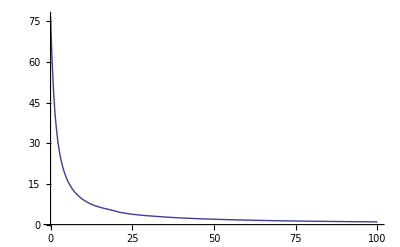

```mathematica
Plot[ DΛ[z]/DΛ[100] , { z , 0 , 100}, PlotRange->All]
```

### DE growth factor, w1 = -0.9

not-ΛCDM growth factor

computes Dadiaw[z_] and Dmw[z_] : ΛCDM growth factor

```mathematica
paramSubsw[1]={Subscript[Ω, m]->1-0.73, Subscript[Ω, Λ]->0.73,ℋ0->100,w ->  -0.9,Subscript[Ω, b]->0.044,Δζ2 -> 2.42 10^-9,h->.71, wb->(.044)/(1-.73), wc-> (1-.73-.044)/(1-.73)};
```

```mathematica
(hSolw=ℋ[a__]->ℋ0 √(Subscript[Ω, m]/a+Subscript[Ω, Λ] a^2 a^(-3(1+w)));
hpSolw=Map[D[#,a]&,hSolw];{hSolw,hpSolw});
```

```mathematica
C1[a_]:= 1 + (1+w) Subscript[Ω, Λ]/Subscript[Ω, m] a^(-3(1+w))/a^-3
```

```mathematica
hsubsw={ℋ[a_]:>ℋ0 √(Subscript[Ω, m]/a+a^2 a^(-3(1+w))Subscript[Ω, Λ]),ℋ'[a_]:>(ℋ0 (-Subscript[Ω, m]/a^2+a^(1-3 (1+w)) (2-3 (1+w)) Subscript[Ω, Λ]))/(2 √(Subscript[Ω, m]/a+a^(2-3 (1+w)) Subscript[Ω, Λ])),ℋ''[a_]:>(3 a^(-3 (1+w)) ℋ0 (a^(6 w) Subscript[Ω, m]^2+2 a^(3 w) (1+2 w+3 w^2) Subscript[Ω, m] Subscript[Ω, Λ]+(1+4 w+3 w^2) Subscript[Ω, Λ]^2))/(4 (a^(3 w) Subscript[Ω, m]+Subscript[Ω, Λ]) √((Subscript[Ω, m]+a^(-3 w) Subscript[Ω, Λ])/a))};
```

```mathematica
DgS[a_]:=(5/2 ℋ0^2 Subscript[Ω, m] ℋ[a]/a) Integrate[C1[ap](1/ℋ[ap])^3,{ap,0,a}]
grS[a_,ai_]:=(ℋ[a]/a^2) Integrate[(1/ℋ[ap])^3,{ap,ai,a}]
(DgpS[a_]=D[DgS[a],a]);
(DgppS[a_]=D[DgpS[a],a]);
```

```mathematica
ClearAll[DgNw,DgppNw,DgpNw];
DgpNw[a_?NumericQ]:=(DgpS[a]/.Integrate[i_,b_]:>integrate[i,b]/.hsubsw/.paramSubsw[1])/.integrate[aa_,b__]:>NIntegrate[aa,b]
DgppNw[a_?NumericQ]:=(DgppS[a]/.Integrate[i_,b_]:>integrate[i,b]/.hsubsw/.paramSubsw[1])/.integrate[aa_,b__]:>NIntegrate[aa,b]
DgNw[a_?NumericQ]:=(5/2 ℋ0^2 Subscript[Ω, m] ℋ[a]/a/.hsubsw/.paramSubsw[1]) NIntegrate[C1[ap](1/ℋ[ap])^3/.hsubsw/.paramSubsw[1],{ap,0,a}]
```

```mathematica
dgN1w=1 (*DgNw[1.]*);
Dgrtabw=Monitor[AbortableTable[{z,DgNw[1/(1+z)]/dgN1w(1+z)},{z,0,10,0.01}],z];
Dgrtabwext=Monitor[AbortableTable[{z,DgNw[1/(1+z)]/dgN1w(1+z)},{z,20,200,10}],z];
Dgrtabwext2=Monitor[AbortableTable[{z,DgNw[1/(1+z)]/dgN1w(1+z)},{z,{500,1000, 10000}}],z];
```

```mathematica
DgrtabInterpw=Interpolation[Join[Dgrtabw, Dgrtabwext, Dgrtabwext2], InterpolationOrder->4];
Clear[Dgrowthw];
Dadiaw[1][z_]=DgrtabInterpw[z]/(1+z);
```

```mathematica
dgpN1w=1(*DgpNw[1.]*);
Dpgrtabw=Monitor[AbortableTable[{z,DgpNw[1/(1+z)]/dgN1w},{z,0,10,0.01}],z];
Dpgrtabwext1=Monitor[AbortableTable[{z,DgpNw[1/(1+z)]/dgN1w},{z,20,200,10}],z];
Dpgrtabwext2=Monitor[AbortableTable[{z,DgpNw[1/(1+z)]/dgN1w},{z,{500,1000,10000}}],z];
Clear[DpgrowthNormw];
DpgrowthNormw[1]=Interpolation[Join[Dpgrtabw, Dpgrtabwext1, Dpgrtabwext2], InterpolationOrder->1];
```

```mathematica
D1subw={D1[zz_]:>Dadiaw[zz],D1p[zz_]:>DpgrowthNormw[zz]};
```

```mathematica
ftabw=Monitor[AbortableTable[{z,(1/(1+z))/(Dadiaw[1][z])DpgrowthNormw[1][z]},{z,0,10,0.01}],z];
ftabwext1=Monitor[AbortableTable[{z,(1/(1+z))/(Dadiaw[1][z])DpgrowthNormw[1][z]},{z,20,200,10}],z];
ftabwext2=Monitor[AbortableTable[{z,(1/(1+z))/(Dadiaw[1][z])DpgrowthNormw[1][z]},{z,{500,1000,10000}}],z];
Clear[fw]
fw[1]=Interpolation[Join[ftabw,ftabwext1,ftabwext2], InterpolationOrder->1];
```

```mathematica
(*Dmgtab = Monitor[ AbortableTable[{z, NIntegrate[ (5/2 - 3/2 Dadiaw[zz[ap]]/ap) (Subscript[Ω, m] ℋ0^2)/(ℋ[ap]^2 ap)/.hsubsw/.paramSubsw , { ap , 1/10000, 1/(1+z)}]} , {z,0 , 3 , .5}], z];*)
```

```mathematica
(*Dmgtabext2 = Monitor[ AbortableTable[{z, NIntegrate[ (5/2 - 3/2 Dadiaw[zz[ap]]/ap) (Subscript[Ω, m] ℋ0^2)/(ℋ[ap]^2 ap)/.hsubsw/.paramSubsw , { ap , 1/10000, 1/(1+z)}]} , {z,0.1, .4, .1}], z];*)
```

```mathematica
(*Dmgtabext = Monitor[ AbortableTable[{z, NIntegrate[ (5/2 - 3/2 Dadiaw[zz[ap]]/ap) (Subscript[Ω, m] ℋ0^2)/(ℋ[ap]^2 ap)/.hsubsw/.paramSubsw , { ap , 1/10000, 1/(1+z)}]} , {z,4 , 10 , 1}], z];*)
```

```mathematica
(*Dmw = Interpolation[Join[Dmgtab, Dmgtabext, Dmgtabext2], InterpolationOrder->3] ;*)
```

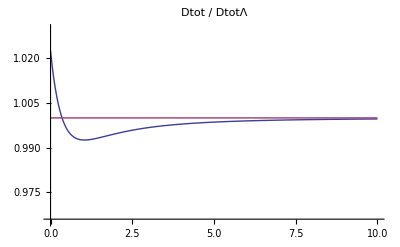

```mathematica
Plot[{( Dadiaw[1][z]/DΛ[z]) , 1}, { z , 0,10}, PlotRange->{.965 , 1.03}, PlotLabel->"Dtot / DtotΛ"]
```

```mathematica
Ωma[1][a_]:= Subscript[Ω, m] ℋ0^2/ℋ[a]^2 a0/a/.a0->1/.hsubsw/.paramSubsw[1];
Dadiawa[1][a_] = Dadiaw[1][zz[a]];

fwa[1][a_] = fw[1][zz[a]];
Dminus[1][a_] = ℋ0/a √(Subscript[Ω, m]/a+a^2 a^(-3(1+w))Subscript[Ω, Λ]) /. paramSubsw[1];
fminus[1][a_] = a/(Dminus[1][a])D[ Dminus[1][ap] , ap] /.ap->a;
```

### DE growth factor, w2 = -1.1

not-ΛCDM growth factor

computes Dadiaw[z_] and Dmw[z_] : ΛCDM growth factor

```mathematica
paramSubsw[2]={Subscript[Ω, m]->1-0.73, Subscript[Ω, Λ]->0.73,ℋ0->100,w ->  -1.1,Subscript[Ω, b]->0.044,Δζ2 -> 2.42 10^-9,h->.71, wb->(.044)/(1-.73), wc-> (1-.73-.044)/(1-.73)};
```

```mathematica
(hSolw=ℋ[a]->ℋ0 √(Subscript[Ω, m]/a+Subscript[Ω, Λ] a^2 a^(-3(1+w)));
hpSolw=Map[D[#,a]&,hSolw];{hSolw,hpSolw});
```

```mathematica
C1[a_]:= 1 + (1+w) Subscript[Ω, Λ]/Subscript[Ω, m] a^(-3(1+w))/a^-3
```

```mathematica
hsubsw={ℋ[a_]:>ℋ0 √(Subscript[Ω, m]/a+a^2 a^(-3(1+w))Subscript[Ω, Λ]),ℋ'[a_]:>(ℋ0 (-Subscript[Ω, m]/a^2+a^(1-3 (1+w)) (2-3 (1+w)) Subscript[Ω, Λ]))/(2 √(Subscript[Ω, m]/a+a^(2-3 (1+w)) Subscript[Ω, Λ])),ℋ''[a_]:>(3 a^(-3 (1+w)) ℋ0 (a^(6 w) Subscript[Ω, m]^2+2 a^(3 w) (1+2 w+3 w^2) Subscript[Ω, m] Subscript[Ω, Λ]+(1+4 w+3 w^2) Subscript[Ω, Λ]^2))/(4 (a^(3 w) Subscript[Ω, m]+Subscript[Ω, Λ]) √((Subscript[Ω, m]+a^(-3 w) Subscript[Ω, Λ])/a))};
```

```mathematica
DgS[a_]:=(5/2 ℋ0^2 Subscript[Ω, m] ℋ[a]/a) Integrate[C1[ap](1/ℋ[ap])^3,{ap,0,a}]
grS[a_,ai_]:=(ℋ[a]/a^2) Integrate[(1/ℋ[ap])^3,{ap,ai,a}]
(DgpS[a_]=D[DgS[a],a]);
(DgppS[a_]=D[DgpS[a],a]);
```

```mathematica
ClearAll[DgNw,DgppNw,DgpNw];
DgpNw[a_?NumericQ]:=(DgpS[a]/.Integrate[i_,b_]:>integrate[i,b]/.hsubsw/.paramSubsw[2])/.integrate[aa_,b__]:>NIntegrate[aa,b]
DgppNw[a_?NumericQ]:=(DgppS[a]/.Integrate[i_,b_]:>integrate[i,b]/.hsubsw/.paramSubsw[2])/.integrate[aa_,b__]:>NIntegrate[aa,b]
DgNw[a_?NumericQ]:=(5/2 ℋ0^2 Subscript[Ω, m] ℋ[a]/a/.hsubsw/.paramSubsw[2]) NIntegrate[C1[ap](1/ℋ[ap])^3/.hsubsw/.paramSubsw[2],{ap,0,a}]
```

```mathematica
dgN1w=1 (*DgNw[1.]*);
Dgrtabw=Monitor[AbortableTable[{z,DgNw[1/(1+z)]/dgN1w(1+z)},{z,0,10,0.01}],z];
Dgrtabwext=Monitor[AbortableTable[{z,DgNw[1/(1+z)]/dgN1w(1+z)},{z,20,200,10}],z];
Dgrtabwext2=Monitor[AbortableTable[{z,DgNw[1/(1+z)]/dgN1w(1+z)},{z,{500,1000, 10000}}],z];
```

```mathematica
DgrtabInterpw=Interpolation[Join[Dgrtabw, Dgrtabwext, Dgrtabwext2], InterpolationOrder->4];
Clear[Dgrowthw];
Dadiaw[2][z_]=DgrtabInterpw[z]/(1+z);
```

```mathematica
dgpN1w=1(*DgpNw[1.]*);
Dpgrtabw=Monitor[AbortableTable[{z,DgpNw[1/(1+z)]/dgN1w},{z,0,10,0.01}],z];
Dpgrtabwext1=Monitor[AbortableTable[{z,DgpNw[1/(1+z)]/dgN1w},{z,20,200,10}],z];
Dpgrtabwext2=Monitor[AbortableTable[{z,DgpNw[1/(1+z)]/dgN1w},{z,{500,1000,10000}}],z];
Clear[DpgrowthNormw];
DpgrowthNormw[2]=Interpolation[Join[Dpgrtabw, Dpgrtabwext1, Dpgrtabwext2], InterpolationOrder->1];
```

```mathematica
D1subw={D1[zz_]:>Dadiaw[zz],D1p[zz_]:>DpgrowthNormw[zz]};
```

```mathematica
ftabw=Monitor[AbortableTable[{z,(1/(1+z))/(Dadiaw[2][z])DpgrowthNormw[2][z]},{z,0,10,0.01}],z];
ftabwext1=Monitor[AbortableTable[{z,(1/(1+z))/(Dadiaw[2][z])DpgrowthNormw[2][z]},{z,20,200,10}],z];
ftabwext2=Monitor[AbortableTable[{z,(1/(1+z))/(Dadiaw[2][z])DpgrowthNormw[2][z]},{z,{500,1000,10000}}],z];
Clear[fw]
fw[2]=Interpolation[Join[ftabw,ftabwext1,ftabwext2], InterpolationOrder->1];
```

```mathematica
(*Dmgtab = Monitor[ AbortableTable[{z, NIntegrate[ (5/2 - 3/2 Dadiaw[zz[ap]]/ap) (Subscript[Ω, m] ℋ0^2)/(ℋ[ap]^2 ap)/.hsubsw/.paramSubsw , { ap , 1/10000, 1/(1+z)}]} , {z,0 , 3 , .5}], z];*)
```

```mathematica
(*Dmgtabext2 = Monitor[ AbortableTable[{z, NIntegrate[ (5/2 - 3/2 Dadiaw[zz[ap]]/ap) (Subscript[Ω, m] ℋ0^2)/(ℋ[ap]^2 ap)/.hsubsw/.paramSubsw , { ap , 1/10000, 1/(1+z)}]} , {z,0.1, .4, .1}], z];*)
```

```mathematica
(*Dmgtabext = Monitor[ AbortableTable[{z, NIntegrate[ (5/2 - 3/2 Dadiaw[zz[ap]]/ap) (Subscript[Ω, m] ℋ0^2)/(ℋ[ap]^2 ap)/.hsubsw/.paramSubsw , { ap , 1/10000, 1/(1+z)}]} , {z,4 , 10 , 1}], z];*)
```

```mathematica
(*Dmw = Interpolation[Join[Dmgtab, Dmgtabext, Dmgtabext2], InterpolationOrder->3] ;*)
```

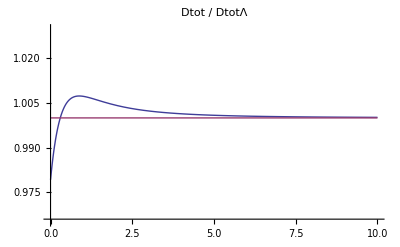

```mathematica
Plot[{( Dadiaw[2][z]/DΛ[z]) , 1}, { z , 0,10}, PlotRange->{.965 , 1.03}, PlotLabel->"Dtot / DtotΛ"]
```

```mathematica
Ωma[2][a_]:= Subscript[Ω, m] ℋ0^2/ℋ[a]^2 a0/a/.a0->1/.hsubsw/.paramSubsw[2];
Dadiawa[2][a_] = Dadiaw[2][zz[a]];

fwa[2][a_] = fw[2][zz[a]];
Dminus[2][a_] = ℋ0/a √(Subscript[Ω, m]/a+a^2 a^(-3(1+w))Subscript[Ω, Λ]) /. paramSubsw[2];
fminus[2][a_] = a/(Dminus[2][a])D[ Dminus[2][ap] , ap] /.ap->a;
```

### DE growth factor expansion in (1+w)

not-ΛCDM growth factor

computes Dadiaw[z_] and Dmw[z_] : ΛCDM growth factor

put all of the numerical functions ( D+, D- , H, f+, f-) in the form g0(a) + (1+w) g1(a)

```mathematica
paramSubsw={Subscript[Ω, m]->1-0.73, Subscript[Ω, Λ]->0.73,ℋ0->100,Subscript[Ω, b]->0.044, w->-.9};
```

```mathematica
(Subscript[Ω, Λ] a^(-3(1+w)))/(Subscript[Ω, m] a^-3)/.paramSubsw /. a->aa[5]
```

0.0214265

```mathematica
1/30 //N
```

0.0333333

```mathematica
(hSolw=ℋ[a__]->ℋ0 √(Subscript[Ω, m]/a+Subscript[Ω, Λ] a^2 a^(-3(1+w)));
hpSolw=Map[D[#,a]&,hSolw];{hSolw,hpSolw});
```

```mathematica
hsubsw={ℋ[a_]:>ℋ0 √(Subscript[Ω, m]/a+a^2 a^(-3(1+w))Subscript[Ω, Λ]),ℋ'[a_]:>(ℋ0 (-Subscript[Ω, m]/a^2+a^(1-3 (1+w)) (2-3 (1+w)) Subscript[Ω, Λ]))/(2 √(Subscript[Ω, m]/a+a^(2-3 (1+w)) Subscript[Ω, Λ])),ℋ''[a_]:>(3 a^(-3 (1+w)) ℋ0 (a^(6 w) Subscript[Ω, m]^2+2 a^(3 w) (1+2 w+3 w^2) Subscript[Ω, m] Subscript[Ω, Λ]+(1+4 w+3 w^2) Subscript[Ω, Λ]^2))/(4 (a^(3 w) Subscript[Ω, m]+Subscript[Ω, Λ]) √((Subscript[Ω, m]+a^(-3 w) Subscript[Ω, Λ])/a))};
```

```mathematica
C1[a_]:= 1 + (1+w) Subscript[Ω, Λ]/Subscript[Ω, m] a^(-3(1+w))/a^-3
```

```mathematica
C10[a_] = Coefficient[ Normal[Series[ C1[a], {w,-1,1}]] (1+w) , (1+w)];
C11[a_] = Coefficient[ Normal[Series[ C1[a], {w,-1,1}]]  , (1+w)];
```

```mathematica
DpIntegrand =Normal[Series[ ( 5/2 ℋ0^2 Subscript[Ω, m] ℋ[a]/a C1[ap](1/ℋ[ap])^3/.hSolw) /. w->-1 + ϵ , { ϵ, 0 , 1}]] /. ϵ->1+w;
```

```mathematica
DpIntegrand0 = Coefficient[ DpIntegrand(1+w), (1+w)];
```

```mathematica
DpIntegrand1 = Coefficient[ DpIntegrand , (1+w)];
```

```mathematica
Dp0Tab = Monitor[ Table[ {a1 , NIntegrate[ DpIntegrand0/. a->a1/.paramSubs , { ap,0,a1}]} , {a1,.1, 1 , .001}],a1];
```

```mathematica
Dp0Tabext1 = Monitor[ Table[ {a1 , NIntegrate[ DpIntegrand0/. a->a1/.paramSubs , { ap,0,a1}]} , {a1,1/200, 1/20 , .001}],a1];
```

```mathematica
Dp0Tabext2 = Monitor[ Table[ {a1 , NIntegrate[ DpIntegrand0/. a->a1/.paramSubs , { ap,0,a1}]} , {a1,{1/10000, 1/1000,1/500}}],a1];
```

```mathematica
Dp0 = Interpolation[Join[Dp0Tab,Dp0Tabext1,Dp0Tabext2]];
```

```mathematica
Dp1Tab = Monitor[ Table[ {a1 , NIntegrate[ DpIntegrand1/. a->a1/.paramSubs , { ap,0,a1}]} , {a1,.1, 1 , .001}],a1];
```

```mathematica
Dp1Tabext1 = Monitor[ Table[ {a1 , NIntegrate[ DpIntegrand1/. a->a1/.paramSubs , { ap,0,a1}]} , {a1,1/200, 1/20 , .001}],a1];
```

```mathematica
Dp1Tabext2 = Monitor[ Table[ {a1 , NIntegrate[ DpIntegrand1/. a->a1/.paramSubs , { ap,0,a1}]} , {a1,{1/10000, 1/1000,1/500}}],a1];
```

```mathematica
Dp1 = Interpolation[Join[Dp1Tab,Dp1Tabext1,Dp1Tabext2]];
```

```mathematica
DminusFull =Normal[ Series[  ℋ0/a √(Subscript[Ω, m]/a+a^2 a^(-3(1+w))Subscript[Ω, Λ])  , { w , -1 , 1}]];
```

```mathematica
Dminus0[a_] =Coefficient[ DminusFull(1+w) , (1+w)];
Dminus1[a_] =Coefficient[ DminusFull , (1+w)];
```

```mathematica
DDpl[a_] = a/ℋ[a](ℋ'[a]/a- ℋ[a]/a^2) Dpl[a] + (5/2 ℋ0^2 Subscript[Ω, m] ℋ[a]/a) CC[a](1/ℋ[a])^3/. hsubsw/.{CC[a]->C1[a]}/.{Dpl[a]->Dpl0 + ( 1+w) Dpl1 };
```

```mathematica
DDplExpand[a_] = Normal[Series[ DDpl[a] , { w , -1 , 1}]];
```

```mathematica
DplprN0[a_] = Normal[Series[ DDpl[a] , { w , -1 , 0}]] /.{Dpl0 -> Dp0[a] }/.paramSubs;
```

```mathematica
DplprN1[a_] = Coefficient[Normal[Series[ DDpl[a] , { w , -1 , 1}]],(1+w) ]/.{Dpl0 -> Dp0[a], Dpl1->Dp1[a] }/.paramSubs;
```

```mathematica
fplExpression[a_] =Normal[ Series[  a/(Dpl0 + (1+w) Dpl1)DDplExpand[a]  , { w  , -1 , 1}]];
```

```mathematica
fpl0[a_] = Coefficient[ fplExpression[a](1+w ) , (1+w)]/.paramSubs/.Dpl0->Dp0[a];
```

```mathematica
fpl1[a_] = Coefficient[ fplExpression[a], (1+w)]/.paramSubs/.{Dpl0->Dp0[a],Dpl1->Dp1[a]};
```

```mathematica
DDm[a_] = D[ Dminus0[a] + ( 1 +w) Dminus1[a] , a];
```

```mathematica
DDmN0[a_] = Coefficient[ (1+w) DDm[a] , (1+w)]/.paramSubs;
```

```mathematica
DDmN1[a_] = Coefficient[  DDm[a] , (1+w)]/.paramSubs;
```

```mathematica
fmExpression[a_] =Normal[ Series[  a/(Dm0 + (1+w) Dm1)DDm[a]  , { w  , -1 , 1}]];
```

```mathematica
fm0[a_] = Coefficient[ fmExpression[a] (1+w) , (1+w)]/.Dm0->Dminus0[a]/.paramSubs ;
```

```mathematica
fm1[a_] = Coefficient[ fmExpression[a]  , (1+w)]/.{Dm0->Dminus0[a],Dm1->Dminus1[a]}/.paramSubs;
```

### Linear Power spectra

#### z = 5 Power spectra - we choose this value because the linear evolution by D^2 is accurate to less than 1 %, and it is within the matter dominated era so we know how to set the initial conditions.

```mathematica
wtab ={-0.85 , -0.90, -0.95, -1.00,-1.10, -1.15};
```

```mathematica
Pmz5List[-1.15] = Import["./CAMB_outputs/DE_wn1p15_matterpower_cs0_z5.dat"];
Pmz5List[-1.10] = Import["./CAMB_outputs/DE_wn1p10_matterpower_cs0_z5.dat"];
Pmz5List[-1.00] = Import["./CAMB_outputs/DE_wn1p00_matterpower_cs0_z5.dat"];
Pmz5List[-0.95] = Import["./CAMB_outputs/DE_wn0p95_matterpower_cs0_z5.dat"];
Pmz5List[-0.90] = Import["./CAMB_outputs/DE_wn0p90_matterpower_cs0_z5.dat"];
Pmz5List[-0.85] = Import["./CAMB_outputs/DE_wn0p85_matterpower_cs0_z5.dat"];
```

```mathematica
Pmz0Listcs0[-0.90]=Import["./CAMB_outputs/DE_wn0p90_matterpower_cs0_z0.dat"];
Pmz0List[-1.00] = Import["./CAMB_outputs/DE_wn1p00_matterpower_cs0_z0.dat"];
```

```mathematica
Pmz0Interpcs0[-0.90]= Interpolation[Pmz0Listcs0[-0.90]];
```

```mathematica
Do[ Pmz5Interp[Round[w,10^-2]//N] = Interpolation[Pmz5List[Round[w,10^-2]//N]]; , {w, wtab}];
Pmz0[-1.00] =Interpolation[Pmz0List[-1.00] ];
```

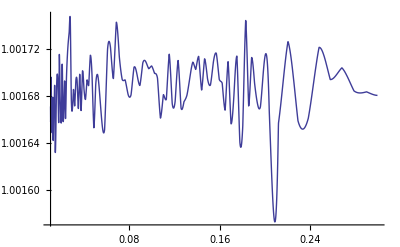

```mathematica
Plot[ {(DΛ[0]/DΛ[5])^2 Pmz5Interp[-1.00][k]/ Pmz0[-1.00][k]} , { k , .01 , .3}, PlotRange->All]
```

```mathematica
P11adiaSubs[1][k_] = (1 + Subscript[Ω, Λ]/Subscript[Ω, m](1+w)/(1-3w)ai^(-3w))^2 P11m /.P11m-> Pmz5Interp[-1.00][k] /.ai->ain/.paramSubsw[1];
P11adiaSubs[2][k_] = (1 + Subscript[Ω, Λ]/Subscript[Ω, m](1+w)/(1-3w)ai^(-3w))^2 P11m /.P11m-> Pmz5Interp[-1.00][k] /.ai->ain/.paramSubsw[2];
```

```mathematica
Pmz0wn1[k_]=Pmz0[-1.00][k];
```

```mathematica
ΔPmz5[k_] = 1/(1+ -0.9)( Pmz5Interp[-0.90][k] - Pmz5Interp[-1.00][k]);
```

```mathematica
(1+-.9)ΔPmz5[.2]/ Pmz5Interp[-0.90][.2]
```

-0.00396318

```mathematica
(1+-.9)Dp1[1]/Dp0[1]
```

0.021591

```mathematica
P11adiaExp =  (1 + Subscript[Ω, Λ]/Subscript[Ω, m](1+w)/(1-3w)ai^(-3w))^2 P11m/.P11m -> P11m0 + (1 +w) P11m1;
```

```mathematica
P11N0[k_] = Normal[Series[P11adiaExp, {w , -1 , 0}]]/. P11m0 -> Pmz5Interp[-1.00][k];
P11N1[k_] =Coefficient[  Normal[Series[ P11adiaExp, {w , -1 , 1}]] , 1+w] /. { P11m0 -> Pmz5Interp[-1.00][k] ,P11m1->  ΔPmz5[k]}/.paramSubs /.  ai->ain;
```

#### z = 0 Power spectrum for c_s^2 = 1

```mathematica
wtab ={-0.85 , -0.90, -0.95, -1.00,-1.10, -1.15};
```

```mathematica
Pmz0List[-1.15] = Import["./CAMB_outputs/DE_wn1p15_matterpower_cs1_z0.dat"];
Pmz0List[-1.10] = Import["./CAMB_outputs/DE_wn1p10_matterpower_cs1_z0.dat"];
Pmz0List[-1.00] = Import["./CAMB_outputs/DE_wn1p00_matterpower_cs1_z0.dat"];
Pmz0List[-0.95] = Import["./CAMB_outputs/DE_wn0p95_matterpower_cs1_z0.dat"];
Pmz0List[-0.90] = Import["./CAMB_outputs/DE_wn0p90_matterpower_cs1_z0.dat"];
Pmz0List[-0.85] = Import["./CAMB_outputs/DE_wn0p85_matterpower_cs1_z0.dat"];
```

```mathematica
Do[ Pmz0cs1[Round[w,10^-2]//N] = Interpolation[Pmz0List[Round[w,10^-2]//N]]; , {w, wtab}];
```

```mathematica
ΔPmz0cs1[k_] = 1/(1+ -0.9)( Pmz0cs1[-0.90][k] - Pmz0cs1[-1.00][k]);
```

```mathematica
P11z0cs1N0[k_] = Pmz0cs1[-1.00][k];
P11z0cs1N1[k_] = ΔPmz0cs1[k];
```

### ΛCDM One loop stuff

Definitions for generic momenta q_1,...,q_n:

```mathematica
ClearAll[qs,qSel,qSum];
qs[n_]:=Table[q[m],{m,1,n}];
qSel[arr_,n1_,n2_]:=Take[arr,{n1,n2}]
qSum[arr_,n1_,n2_]:=Sum[arr[[nn]],{nn,n1,n2}]
```

The kernels: KerN[n,...][[1]]=F_n(...), KerN[n,...][[2]]=G_n(...).

```mathematica
ClearAll[KerN];
KerN[n_,arr_]:=Module[{k,k1,k2},
k=(qSum[arr,1,n]);
k1[m_]:=(qSum[arr,1,m]);
k2[m_]:=(qSum[arr,m+1,n]);
{
Sum[(KerN[m,qSel[arr,1,m]][[2]])/((2n+3)(n-1))((1+2n)(k.k1[m])/(k1[m].k1[m])KerN[n-m,qSel[arr,m+1,n]][[1]]+((k.k)(k1[m].k2[m]))/((k1[m].k1[m])(k2[m].k2[m]))KerN[n-m,qSel[arr,m+1,n]][[2]]),{m,1,n-1}],
Sum[(KerN[m,qSel[arr,1,m]][[2]])/((2n+3)(n-1))(3(k.k1[m])/(k1[m].k1[m])KerN[n-m,qSel[arr,m+1,n]][[1]]+n((k.k)(k1[m].k2[m]))/((k1[m].k1[m])(k2[m].k2[m]))KerN[n-m,qSel[arr,m+1,n]][[2]]),{m,1,n-1}]
}
];
KerN[1,a_]={1,1};
```

```mathematica
KerNSym[n_,arr_]:=Total[((KerN[n,#1]&)/@Permutations[arr])/(n!)]
```

Vector substitutions for k, q, and p (more convenient for expanding integrands that using Sin and Cos)

```mathematica
vecSubs={k->k*{0,0,1},q->q*{Sqrt[1-x^2],0,x},p->p*{Sqrt[1-μ^2]cϕ,Sqrt[1-μ^2]Sqrt[1-cϕ^2],μ}}
```

{k→{0,0,k},q→{q √(1-x^2),0,q x},p→{cϕ p √(1-μ^2),√(1-cϕ^2) p √(1-μ^2),p μ}}

P_(1-loop)with IR-safe integrand

```mathematica
(*f3sp13pre=((KerNSym[3,{k,q,q1}][[1]])/.q1->-q+ϵ)//Assuming[(k|q|q1|ϵ)∈Vectors[dim],#//TensorExpand]&;*)
```

```mathematica
(*f3sp13list=Map[#/.{(ϵ.a__):>0,(a__.ϵ):>0,ϵ.ϵ->0}&,List@@f3sp13pre];*)
```

```mathematica
(*f3sp13=Select[f3sp13list,(#=!=0&&#=!=Indeterminate)&]//Total;*)
```

```mathematica
f3sp13=-(7 (k.q)^2)/(54 (q.q)^2)-(7 (k.q)^2)/(54 k.k q.q)+(5 k.k)/(126 (k.k-2 k.q+q.q))-(11 k.q)/(108 (k.k-2 k.q+q.q))+(7 (k.q)^2)/(108 k.k (k.k-2 k.q+q.q))-(k.k (k.q)^2)/(54 (q.q)^2 (k.k-2 k.q+q.q))+(4 (k.q)^3)/(189 (q.q)^2 (k.k-2 k.q+q.q))-(23 k.k k.q)/(756 q.q (k.k-2 k.q+q.q))+(25 (k.q)^2)/(252 q.q (k.k-2 k.q+q.q))-(2 (k.q)^3)/(27 k.k q.q (k.k-2 k.q+q.q))+(5 k.k)/(126 (k.k+2 k.q+q.q))+(11 k.q)/(108 (k.k+2 k.q+q.q))+(7 (k.q)^2)/(108 k.k (k.k+2 k.q+q.q))-(k.k (k.q)^2)/(54 (q.q)^2 (k.k+2 k.q+q.q))-(4 (k.q)^3)/(189 (q.q)^2 (k.k+2 k.q+q.q))+(23 k.k k.q)/(756 q.q (k.k+2 k.q+q.q))+(25 (k.q)^2)/(252 q.q (k.k+2 k.q+q.q))+(2 (k.q)^3)/(27 k.k q.q (k.k+2 k.q+q.q));
```

```mathematica
Clear[P13Igr,P22Igr,P1loopIgr];
P13Igr[kk_,qq_,xx_,kmin_,kmax_]=((6P11vec[k,kmin,kmax]*P11vec[q,kmin,kmax]*f3sp13)/.vecSubs//Simplify)/.{k->kk,q->qq,x->xx};
P22Igr[kk_,qq_,xx_,kmin_,kmax_]=((2P11vec[q,kmin,kmax]*P11vec[k-q,kmin,kmax](KerNSym[2,{q,k-q}][[1]])^2 Boole[Sqrt[(k-q).(k-q)]-Sqrt[q.q]>0]
+2P11vec[q,kmin,kmax]*P11vec[k+q,kmin,kmax](KerNSym[2,{-q,k+q}][[1]])^2 Boole[Sqrt[(k+q).(k+q)]-Sqrt[q.q]>0])/.vecSubs//Simplify)/.{k->kk,q->qq,x->xx};
P1loopIgr[kk_,qq_,xx_,kmin_,kmax_]=P13Igr[kk,qq,xx,kmin,kmax]+P22Igr[kk,qq,xx,kmin,kmax];
```

```mathematica
Clear[P1loop,P22,P13];
P1loop[kk_,kmin_,kmax_,cutscale_]:=NIntegrate[(2π*q^2)/(2π)^3 P1loopIgr[kk,q,x,kmin,kmax],{x,-1,1},{q,kmin/cutscale,kmax*cutscale},AccuracyGoal-> 6,MaxRecursion->12]
P22[kk_,kmin_,kmax_,cutscale_]:=NIntegrate[(2π*q^2)/(2π)^3 P22Igr[kk,q,x,kmin,kmax],{x,-1,1},{q,kmin/cutscale,kmax*cutscale},AccuracyGoal-> 6,MaxRecursion->25]
P13[kk_,kmin_,kmax_,cutscale_]:=NIntegrate[(2π*q^2)/(2π)^3 P13Igr[kk,q,x,kmin,kmax],{x,-1,1},{q,kmin/cutscale,kmax*cutscale},AccuracyGoal-> 6,MaxRecursion->25]
```

```mathematica
ClearAll[p22Std,twoP13Std,P1loopStandard];
p22Std[k_,P11_,kmin_,kmax_,cutscale_]:=1/98 k^3/(4 π^2)  NIntegrate[P11[k r] P11[k √(1+r^2-2 r x)]((3 r + 7 x - 10 r x^2)^2)/((1+r^2-2 r x)^2),{x,-1,1},{r,kmin/cutscale/k,kmax*cutscale/k},AccuracyGoal-> 6,MaxRecursion->25];
twoP13Std[k_,P11_,kmin_,kmax_,cutscale_]:=2 ×1/504 k^3/(4 π^2) P11[k]* NIntegrate[P11[k r](12/r^2-158+100 r^2-42 r^4+3/r^3(r^2-1)^3(7 r^2+2) Log[Abs[(1+r)]/Abs[(1-r)]]),{r,kmin/cutscale/k,kmax*cutscale/k},AccuracyGoal-> 6,MaxRecursion->25];
P1loopStandard[k_,P11_,kmin_,kmax_,cutscale_]:=p22Std[k,P11,kmin,kmax,cutscale]+twoP13Std[k,P11,kmin,kmax,cutscale]
```

Tests:

-143.955

Evaluation P_(1-loop-SPT-real) in ΛCDM

```mathematica
P22ΛCDMTab = Monitor[ Table[ { k , p22Std[k,Pmz0[-1.00],.0001,10,2]} , { k , looptab2}], k];
```

```mathematica
P13ΛCDMTab =Monitor[  Table[ { k , twoP13Std[k,Pmz0[-1.00],.0001,10,2]} , { k , looptab2}], k];
```

```mathematica
cs1 = .2 * 2 π;
```

```mathematica
P1loopΛCDMTab = Table[ { P22ΛCDMTab[[i]][[1]] , P22ΛCDMTab[[i]][[2]] + P13ΛCDMTab[[i]][[2]]} , { i , 1 , Length[P22ΛCDMTab]}];
```

```mathematica
P1loopΛCDM = Interpolation[P1loopΛCDMTab];
P13ΛCDM = Interpolation[P13ΛCDMTab];
P22ΛCDM = Interpolation[P22ΛCDMTab];
PTotΛ[k_,cs_] = Pmz0[-1.00][k] + P1loopΛCDM[k] - 2 k^2 cs Pmz0wn1[k];
```

### wCDM One loop stuff

Definitions for generic momenta q_1,...,q_n:

```mathematica
ClearAll[qs,qSel,qSum];
qs[n_]:=Table[q[m],{m,1,n}];
qSel[arr_,n1_,n2_]:=Take[arr,{n1,n2}]
qSum[arr_,n1_,n2_]:=Sum[arr[[nn]],{nn,n1,n2}]
```

The kernels: KerN[n,...][[1]]=F_n(...), KerN[n,...][[2]]=G_n(...).

```mathematica
ClearAll[KerN];
KerN[n_,arr_]:=Module[{k,k1,k2},
k=(qSum[arr,1,n]);
k1[m_]:=(qSum[arr,1,m]);
k2[m_]:=(qSum[arr,m+1,n]);
{
Sum[(KerN[m,qSel[arr,1,m]][[2]])/((2n+3)(n-1))((1+2n)(k.k1[m])/(k1[m].k1[m])KerN[n-m,qSel[arr,m+1,n]][[1]]+((k.k)(k1[m].k2[m]))/((k1[m].k1[m])(k2[m].k2[m]))KerN[n-m,qSel[arr,m+1,n]][[2]]),{m,1,n-1}],
Sum[(KerN[m,qSel[arr,1,m]][[2]])/((2n+3)(n-1))(3(k.k1[m])/(k1[m].k1[m])KerN[n-m,qSel[arr,m+1,n]][[1]]+n((k.k)(k1[m].k2[m]))/((k1[m].k1[m])(k2[m].k2[m]))KerN[n-m,qSel[arr,m+1,n]][[2]]),{m,1,n-1}]
}
];
KerN[1,a_]={1,1};
```

```mathematica
KerNSym[n_,arr_]:=Total[((KerN[n,#1]&)/@Permutations[arr])/(n!)]
```

Vector substitutions for k, q, and p (more convenient for expanding integrands that using Sin and Cos)

```mathematica
vecSubs={k->k*{0,0,1},q->q*{Sqrt[1-x^2],0,x},p->p*{Sqrt[1-μ^2]cϕ,Sqrt[1-μ^2]Sqrt[1-cϕ^2],μ}}
```

{k→{0,0,k},q→{q √(1-x^2),0,q x},p→{cϕ p √(1-μ^2),√(1-cϕ^2) p √(1-μ^2),p μ}}

P_(1-loop)with IR-safe integrand

```mathematica
(*f3sp13pre=((KerNSym[3,{k,q,q1}][[1]])/.q1->-q+ϵ)//Assuming[(k|q|q1|ϵ)∈Vectors[dim],#//TensorExpand]&;*)
```

```mathematica
(*f3sp13list=Map[#/.{(ϵ.a__):>0,(a__.ϵ):>0,ϵ.ϵ->0}&,List@@f3sp13pre];*)
```

```mathematica
(*f3sp13=Select[f3sp13list,(#=!=0&&#=!=Indeterminate)&]//Total;*)
```

```mathematica
f3sp13=-(7 (k.q)^2)/(54 (q.q)^2)-(7 (k.q)^2)/(54 k.k q.q)+(5 k.k)/(126 (k.k-2 k.q+q.q))-(11 k.q)/(108 (k.k-2 k.q+q.q))+(7 (k.q)^2)/(108 k.k (k.k-2 k.q+q.q))-(k.k (k.q)^2)/(54 (q.q)^2 (k.k-2 k.q+q.q))+(4 (k.q)^3)/(189 (q.q)^2 (k.k-2 k.q+q.q))-(23 k.k k.q)/(756 q.q (k.k-2 k.q+q.q))+(25 (k.q)^2)/(252 q.q (k.k-2 k.q+q.q))-(2 (k.q)^3)/(27 k.k q.q (k.k-2 k.q+q.q))+(5 k.k)/(126 (k.k+2 k.q+q.q))+(11 k.q)/(108 (k.k+2 k.q+q.q))+(7 (k.q)^2)/(108 k.k (k.k+2 k.q+q.q))-(k.k (k.q)^2)/(54 (q.q)^2 (k.k+2 k.q+q.q))-(4 (k.q)^3)/(189 (q.q)^2 (k.k+2 k.q+q.q))+(23 k.k k.q)/(756 q.q (k.k+2 k.q+q.q))+(25 (k.q)^2)/(252 q.q (k.k+2 k.q+q.q))+(2 (k.q)^3)/(27 k.k q.q (k.k+2 k.q+q.q));
```

```mathematica
Clear[P13Igr,P22Igr,P1loopIgr];
P13Igr[kk_,qq_,xx_,kmin_,kmax_]=((6P11vec[k,kmin,kmax]*P11vec[q,kmin,kmax]*f3sp13)/.vecSubs//Simplify)/.{k->kk,q->qq,x->xx};
P22Igr[kk_,qq_,xx_,kmin_,kmax_]=((2P11vec[q,kmin,kmax]*P11vec[k-q,kmin,kmax](KerNSym[2,{q,k-q}][[1]])^2 Boole[Sqrt[(k-q).(k-q)]-Sqrt[q.q]>0]
+2P11vec[q,kmin,kmax]*P11vec[k+q,kmin,kmax](KerNSym[2,{-q,k+q}][[1]])^2 Boole[Sqrt[(k+q).(k+q)]-Sqrt[q.q]>0])/.vecSubs//Simplify)/.{k->kk,q->qq,x->xx};
P1loopIgr[kk_,qq_,xx_,kmin_,kmax_]=P13Igr[kk,qq,xx,kmin,kmax]+P22Igr[kk,qq,xx,kmin,kmax];
```

```mathematica
Clear[P1loop,P22,P13];
P1loop[kk_,kmin_,kmax_,cutscale_]:=NIntegrate[(2π*q^2)/(2π)^3 P1loopIgr[kk,q,x,kmin,kmax],{x,-1,1},{q,kmin/cutscale,kmax*cutscale},AccuracyGoal-> 6,MaxRecursion->12]
P22[kk_,kmin_,kmax_,cutscale_]:=NIntegrate[(2π*q^2)/(2π)^3 P22Igr[kk,q,x,kmin,kmax],{x,-1,1},{q,kmin/cutscale,kmax*cutscale},AccuracyGoal-> 6,MaxRecursion->25]
P13[kk_,kmin_,kmax_,cutscale_]:=NIntegrate[(2π*q^2)/(2π)^3 P13Igr[kk,q,x,kmin,kmax],{x,-1,1},{q,kmin/cutscale,kmax*cutscale},AccuracyGoal-> 6,MaxRecursion->25]
```

```mathematica
ClearAll[p22Std,twoP13Std,P1loopStandard];
p22Std[k_,P11_,kmin_,kmax_,cutscale_]:=1/98 k^3/(4 π^2)  NIntegrate[P11[k r] P11[k √(1+r^2-2 r x)]((3 r + 7 x - 10 r x^2)^2)/((1+r^2-2 r x)^2),{x,-1,1},{r,kmin/cutscale/k,kmax*cutscale/k},AccuracyGoal-> 6,MaxRecursion->25];
twoP13Std[k_,P11_,kmin_,kmax_,cutscale_]:=2 ×1/504 k^3/(4 π^2) P11[k]* NIntegrate[P11[k r](12/r^2-158+100 r^2-42 r^4+3/r^3(r^2-1)^3(7 r^2+2) Log[Abs[(1+r)]/Abs[(1-r)]]),{r,kmin/cutscale/k,kmax*cutscale/k},AccuracyGoal-> 6,MaxRecursion->25];
P1loopStandard[k_,P11_,kmin_,kmax_,cutscale_]:=p22Std[k,P11,kmin,kmax,cutscale]+twoP13Std[k,P11,kmin,kmax,cutscale]
```

```mathematica
p22Stdcs1Integrand= 1/98 k^3/(4 π^2)  P11[k r] P11[k √(1+r^2-2 r x)]((3 r + 7 x - 10 r x^2)^2)/((1+r^2-2 r x)^2)  /. P11[x__] -> P110[x] + ( 1+w) P111[x];
twoP13Stdcs1Integrand = 2 ×1/504 k^3/(4 π^2) P11[k]*P11[k r](12/r^2-158+100 r^2-42 r^4+3/r^3(r^2-1)^3(7 r^2+2) Log[Abs[(1+r)]/Abs[(1-r)]])/. P11[x__] -> P110[x] + ( 1+w) P111[x];

p22Stdcs1IntegrandN0 = Coefficient[ (1+w) p22Stdcs1Integrand , (1+w) ]/.{ P110->P11z0cs1N0 , P111->P11z0cs1N1};
p22Stdcs1IntegrandN1 = Coefficient[  p22Stdcs1Integrand , (1+w) ]/.{ P110->P11z0cs1N0 , P111->P11z0cs1N1};

twoP13Stdcs1IntegrandN0 = Coefficient[ (1+w) twoP13Stdcs1Integrand , (1+w) ]/.{ P110->P11z0cs1N0 , P111->P11z0cs1N1};
twoP13Stdcs1IntegrandN1 = Coefficient[  twoP13Stdcs1Integrand , (1+w) ]/.{ P110->P11z0cs1N0 , P111->P11z0cs1N1};
```

```mathematica
P22Stdcs1N0[kext_ , kmin_, kmax_ , cutscale_]:=NIntegrate[ p22Stdcs1IntegrandN0  /. k->kext ,{x,-1,1},{r,kmin/cutscale/kext,kmax*cutscale/kext},AccuracyGoal-> 6,MaxRecursion->25];
P22Stdcs1N1[kext_ , kmin_, kmax_ , cutscale_]:=NIntegrate[ p22Stdcs1IntegrandN1 /. k->kext ,{x,-1,1},{r,kmin/cutscale/kext,kmax*cutscale/kext},AccuracyGoal-> 6,MaxRecursion->25]
twoP13Stdcs1N0[kext_ , kmin_, kmax_ , cutscale_]:=NIntegrate[ twoP13Stdcs1IntegrandN0  /. k->kext ,{r,kmin/cutscale/kext,kmax*cutscale/kext},AccuracyGoal-> 6,MaxRecursion->25];
twoP13Stdcs1N1[kext_ , kmin_, kmax_ , cutscale_]:=NIntegrate[ twoP13Stdcs1IntegrandN1  /. k->kext ,{r,kmin/cutscale/kext,kmax*cutscale/kext},AccuracyGoal-> 6,MaxRecursion->25];
```

Tests:

-143.955

Evaluation P_(1-loop-SPT-real) in wCDM

```mathematica
P22wCDMTab0 = Monitor[ Table[ { k , P22Stdcs1N0[k,.0001,10,2]} , { k , looptab2}], k];
```

```mathematica
P22wCDMTab1= Monitor[ Table[ { k , P22Stdcs1N1[k,.0001,10,2]} , { k , looptab2}], k];
```

```mathematica
P13wCDMTab0= Monitor[ Table[ { k , twoP13Stdcs1N0[k,.0001,10,2]} , { k , looptab2}], k];
```

```mathematica
P13wCDMTab1= Monitor[ Table[ { k , twoP13Stdcs1N1[k,.0001,10,2]} , { k , looptab2}], k];
```

```mathematica
P13wCDMN0 = Interpolation[P13wCDMTab0];
P13wCDMN1 = Interpolation[P13wCDMTab1];
P22wCDMN0 = Interpolation[P22wCDMTab0];
P22wCDMN1 = Interpolation[P22wCDMTab1];

P1loopwCDM[k_,w_] = P13wCDMN0[k] + P22wCDMN0[k] + (1+w)(  P13wCDMN1[k] + P22wCDMN1[k] ) ;
PlinwCDM[k_,w_] =  P11z0cs1N0[k] + (1+w)P11z0cs1N1[k] ;

PTotwCDM[k_,w_,cs_, xi_] =  (P11z0cs1N0[k] + (1+w)P11z0cs1N1[k]  + P13wCDMN0[k] + P22wCDMN0[k] + (1+w)(  P13wCDMN1[k] + P22wCDMN1[k] )  - 2 k^2 cs (1 + xi Subscript[Ω, Λ]/Subscript[Ω, m] (1 + w)) ( P11z0cs1N0[k] + (1+w)P11z0cs1N1[k]))/.paramSubs  ;
```

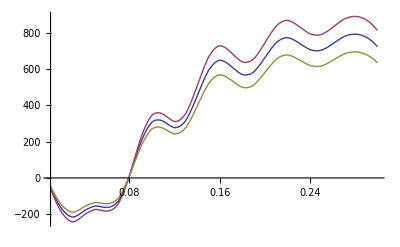

```mathematica
Plot[ {P1loopwCDM[k,-1], P1loopwCDM[k,-1.1], P1loopwCDM[k,-.9]} , { k , .01 , .3}]
```

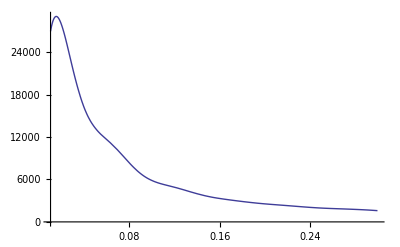

```mathematica
Plot[ PTotwCDM[k,-1,0, 0] , { k , .01 , .3}]
```

### check IR safety ΛCDM - remember that p13 + 2*p22 should cancel because of how you rewrite the IR safe integrand (basically p22 also diverges for q -> k, so you map that divergence down to q -> 0)

in the below notaion, P1loop = P22 + 2 P13, so then for the ir safety check, we do 2*p22 + 2*p13, note that i put a 1/2 in front of p13 because i’m going to integrate it in dx along with p22

```mathematica
scalingrep ={P11[a_] -> 1/knl^3(a/knl)^n};
```

```mathematica
twop22irtest = 2 1/98 k^3/(4 π^2)  P11[k r] P11[k √(1+r^2-2 r x)]((3 r + 7 x - 10 r x^2)^2)/((1+r^2-2 r x)^2) /. scalingrep;
twop13irtest =1/2 2 1/504 k^3/(4 π^2) P11[k]P11[k r](12/r^2-158+100 r^2-42 r^4+3/r^3(r^2-1)^3(7 r^2+2) Log[Abs[(1+r)]/Abs[(1-r)]])/.scalingrep;
```

```mathematica
Integrate[Series[ twop22irtest +  twop13irtest , { r , 0 , 1}, Assumptions ->{r>0}]//Normal , { x , -1 , 1}]
```

0

# computations using a: expansion in 1+w

#### Setup equations - this is the same, we will expand everything later

Let us write down the equations: these need to be adjusted to the correct equations. Also, the non - linear vertexes α and β need to be symmetrized. Integration over the k-varialbles is left implicit until the very last step (as well as substituting the label k with a 3-vector.)
 
all derivatives, or pr labels, are with respect to scale factor a

Note that the θ appearing below is really the rescaled Θ = - C/(ℋ f_+)θ

below α( k , k1, k2 ) = (2π)^3 δ^(3)( k - k_1 - k_2) α(k_1, k_2)

```mathematica
eqa={a D[δ[k,a], a]-fp[a] θ[k,a]== fp[a]/CC[a] α[k,k1,k2] δS[k1,a]θS[k2,a],a D[θ[k,a], a]-fp[a] θ[k,a]+ 3(Ωm CC[a])/(2 fp[a])(θ[k,a]-δ[k,a])==fp[a]/CC[a] β[k,k1,k2]θS[k1,a]θS[k2,a]};
```

```mathematica
αs[q1_,q2_] :=1 + (q1.q2)/2( 1/(q1.q1) + 1/(q2.q2));
α1[q1_,q2_] :=1 + q1.q2( 1/(q1.q1) );
βs[q1_,q2_] = (q1.q2 * (q1.q1 + q2.q2 + 2 q1.q2))/(2 q1.q1 * q2.q2);
```

δ2 Solution: let us put the integrations in k and η at the very end.

```mathematica
δ2sola[k_,a_]=Gδα[k,a,a1](α[k,k21,k11] fp[a1]δ1[k11,a1] θ1[k21,a1])/CC[a1]+Gδβ[k,a,a1](β[k,k11,k21]fp[a1]  θ1[k11,a1] θ1[k21,a1])/CC[a1];
θ2sola[k_,a_]=Gθα[k,a,a1](α[k,k21,k11] fp[a1]δ1[k11,a1] θ1[k21,a1])/CC[a1]+Gθβ[k,a,a1](β[k,k11,k21]fp[a1] θ1[k11,a1] θ1[k21,a1])/CC[a1];
```

δ3 Solution: : let us put the integration at the very end.

```mathematica
δ3sola[k_,a_]=Gδα[k,a,a2](α[k,k2,k1]fp[a2] (δ2[k1,a2] θ1[k2,a2]+δ1[k1,a2] θ2[k2,a2]))/CC[a2]+Gδβ[k,a,a2](β[k,k1,k2] fp[a2]2θ2[k1,a2] θ1[k2,a2])/CC[a2];
```

```mathematica
δ3solsuba[k_,a_]=δ3sola[k,a]/.{δ2[a___]-> δ2sola[a],θ2[a___]-> θ2sola[a]};
```

```mathematica
δ3solsubSimpa[k_,a_]=δ3solsuba[k,a]//FullSimplify;
```

This expression needs to be integrated in (∫_0)^a ⅆa2 (∫_0)^a2 ⅆa1 and also in the various momenta k's: basically, all repeated `indexes' must be integrated over.

Green’s Function

```mathematica
Gδαsola[k_,a_,a1_]=1/(a1 ( Dmpr[a1] Dpl[a1] - Dplpr[a1]Dm[a1]))(Dmpr[a1] Dpl[a] - Dplpr[a1] Dm[a])  ;
Gδβsola[k_,a_,a1_]=1/(a1 ( Dmpr[a1] Dpl[a1] - Dplpr[a1]Dm[a1]))((-fp[a1])/a1)(Dm[a1] Dpl[a] - Dpl[a1] Dm[a]);
Gθαsola[k_,a_,a1_]=1/(a1 ( Dmpr[a1] Dpl[a1] - Dplpr[a1]Dm[a1]))(Dmpr[a1] (a Dplpr[a])/fp[a] - Dplpr[a1] (a Dmpr[a])/fp[a]);
Gθβsola[k_,a_,a1_]=1/(a1 ( Dmpr[a1] Dpl[a1] - Dplpr[a1]Dm[a1]))((- fp[a1])/a1)(Dm[a1] (a Dplpr[a])/fp[a] - Dpl[a1](a Dmpr[a])/fp[a]);
```

Substitute Greens Functions

```mathematica
Greensubsa={Gδα[a___]-> Gδαsola[a],Gδβ[a___]-> Gδβsola[a],Gθα[a___]-> Gθαsola[a],Gθβ[a___]-> Gθβsola[a]};
```

```mathematica
δ3solGreena[k_,a_]=(δ3solsubSimpa[k,a]/.Greensubsa)//FullSimplify;
```

This expression needs to be integrated in (∫_0)^a0 ⅆa2 (∫_0)^a2 ⅆa1

It would be nice to be able to group the various integrals that factorize : time integral times a space integral. First let us  extract the time dependence

```mathematica
δsubsa={δ1[k_,a_]-> Dpl[a]/Dpl[aini] δ1k[k],θ1[k_,a_]-> (a Dplpr[a])/(fp[a]Dpl[aini])δ1k[k]};
```

```mathematica
FunctionExpandSubs = {Dpl[a_]->Dpl0[a] + (1+w) Dpl1[a], Dplpr[a_] -> Dplpr0[a] +(1+w) Dplpr1[a], fp[a_]->fp0[a] + (1+w) fp1[a], Dm[a_] -> Dm0[a] + ( 1 +w)Dm1[a], Dmpr[a_]->Dmpr0[a] + (1+w) Dmpr1[a], CC[a_] -> CC0[a]+(1+w)CC1[a]/.paramSubs};
```

```mathematica
TimeSubsTot ={  Dpl0[a_]-> Dp0[a] , Dpl1[a_]-> Dp1[a] , Dplpr0[a_]-> DplprN0[a], Dplpr1[a_]-> DplprN1[a] ,fp0[a_]-> fpl0[a], fp1[a_]-> fpl1[a], Dm0[a_]-> Dminus0[a],Dm1[a_]-> Dminus1[a],Dmpr0[a_]-> DDmN0[a] ,Dmpr1[a_]-> DDmN1[a],CC0[a_]-> C10[a],CC1[a_]-> C11[a]}/.paramSubs;
```

```mathematica
αβsubs= { αfn[x_,y_] -> α1[x,y] , βfn[x_,y_] -> βs[x,y]};
αβSymmsubs = { αfn[x_,y_] -> αs[x,y] , βfn[x_,y_] -> βs[x,y]};
vecSubs1={k->k*{0,0,1},kint->kint*{Sqrt[1-x^2],0,x}};
kintExpandSubs = {Dpl[a_]->Dpl0[a] + (1+w) Dpl1[a], P11[x__]-> P110[x] + (1+w)P111[x]};
kintSubs = {Dpl0[a_]-> Dp0[a] , Dpl1[a_]-> Dp1[a], P110[x__]-> P11N0[x] , P111[x__]->P11N1[x] };
```

#### P13 - symmetrization technique

Now, how do we separate the part to integrate in time from the ones to integrate in k.

```mathematica
δ3Expandeda=(((δ3solGreena[k,a]/.δsubsa)//FullSimplify)//Expand);
```

Let us define these k-dependent coefficients:

```mathematica
Clear[Coeff1,Coeff2,Coeff3,Coeff4,Coeff5,Coeff6]
```

```mathematica
Coeff1=α[k,k2,k1]α[k1,k21,k11] δ1k[k2] δ1k[k11]δ1k[k21];
Coeff2=α[k,k2,k1]β[k1,k11,k21] δ1k[k2] δ1k[k11]δ1k[k21];
Coeff3=α[k,k2,k1]α[k2,k21,k11]δ1k[k1]δ1k[k11] δ1k[k21];
Coeff4=α[k,k2,k1]β[k2,k11,k21]δ1k[k1]δ1k[k11] δ1k[k21];
Coeff5=β[k,k1,k2]α[k1,k21,k11]δ1k[k2]δ1k[k11]  δ1k[k21];
Coeff6=β[k,k1,k2]β[k1,k11,k21]δ1k[k2]δ1k[k11]  δ1k[k21];
```

These are the time-dependent factors in front:

```mathematica
int1a=(Coefficient[δ3Expandeda,Coeff1]//FullSimplify);
int2a=(Coefficient[δ3Expandeda,Coeff2]//FullSimplify);
int3a=(Coefficient[δ3Expandeda,Coeff3]//FullSimplify);
int4a=(Coefficient[δ3Expandeda,Coeff4]//FullSimplify);
int5a=(Coefficient[δ3Expandeda,Coeff5]//FullSimplify);
int6a=(Coefficient[δ3Expandeda,Coeff6]//FullSimplify);
```

Check that I included everything: ok.

```mathematica
δ3factorizeda=(int1a Coeff1+int2a Coeff2+int3a Coeff3+int4a Coeff4+int5a Coeff5+int6a Coeff6);
```

```mathematica
CheckTotala=δ3Expandeda-δ3factorizeda//FullSimplify
```

0

Notice that the normalization of D_-does not matter in the int1...int6 above
Below, break up the time integrals into (1+w)^0and (1+w) pieces

```mathematica
int1Na0 = NIntegrate[(Coefficient[Normal[Series[ int1a/.FunctionExpandSubs , {w , -1 , 1}]] (1+w) , (1+w)] /.TimeSubsTot/.aini->ain)/.a->a0 , {a2 , alow, a0} , { a1, alow , a2}];
int1Na1 =NIntegrate[(Coefficient[Normal[Series[ int1a/.FunctionExpandSubs , {w , -1 , 1}]] , (1+w)] /.TimeSubsTot/.aini->ain)/.a->a0 , {a2 , alow, a0} , { a1, alow , a2}];
```

```mathematica
int2Na0 = NIntegrate[(Coefficient[Normal[Series[ int2a/.FunctionExpandSubs , {w , -1 , 1}]] (1+w) , (1+w)] /.TimeSubsTot/.aini->ain)/.a->a0 , {a2 , alow, a0} , { a1, alow , a2}];
int2Na1 =NIntegrate[(Coefficient[Normal[Series[ int2a/.FunctionExpandSubs , {w , -1 , 1}]] , (1+w)] /.TimeSubsTot/.aini->ain)/.a->a0 , {a2 , alow, a0} , { a1, alow , a2}];
```

```mathematica
int3Na0 = NIntegrate[(Coefficient[Normal[Series[ int3a/.FunctionExpandSubs , {w , -1 , 1}]] (1+w) , (1+w)] /.TimeSubsTot/.aini->ain)/.a->a0 , {a2 , alow, a0} , { a1, alow , a2}];
int3Na1 =NIntegrate[(Coefficient[Normal[Series[ int3a/.FunctionExpandSubs , {w , -1 , 1}]] , (1+w)] /.TimeSubsTot/.aini->ain)/.a->a0 , {a2 , alow, a0} , { a1, alow , a2}];
```

```mathematica
int4Na0 = NIntegrate[(Coefficient[Normal[Series[ int4a/.FunctionExpandSubs , {w , -1 , 1}]] (1+w) , (1+w)] /.TimeSubsTot/.aini->ain)/.a->a0 , {a2 , alow, a0} , { a1, alow , a2}];
int4Na1 =NIntegrate[(Coefficient[Normal[Series[ int4a/.FunctionExpandSubs , {w , -1 , 1}]] , (1+w)] /.TimeSubsTot/.aini->ain)/.a->a0 , {a2 , alow, a0} , { a1, alow , a2}];
```

```mathematica
int5Na0 = NIntegrate[(Coefficient[Normal[Series[ int5a/.FunctionExpandSubs , {w , -1 , 1}]] (1+w) , (1+w)] /.TimeSubsTot/.aini->ain)/.a->a0 , {a2 , alow, a0} , { a1, alow , a2}];
int5Na1 =NIntegrate[(Coefficient[Normal[Series[ int5a/.FunctionExpandSubs , {w , -1 , 1}]] , (1+w)] /.TimeSubsTot/.aini->ain)/.a->a0 , {a2 , alow, a0} , { a1, alow , a2}];
```

```mathematica
int6Na0 = NIntegrate[(Coefficient[Normal[Series[ int6a/.FunctionExpandSubs , {w , -1 , 1}]] (1+w) , (1+w)] /.TimeSubsTot/.aini->ain)/.a->a0 , {a2 , alow, a0} , { a1, alow , a2}];
int6Na1 =NIntegrate[(Coefficient[Normal[Series[ int6a/.FunctionExpandSubs , {w , -1 , 1}]] , (1+w)] /.TimeSubsTot/.aini->ain)/.a->a0 , {a2 , alow, a0} , { a1, alow , a2}];
```

Let’s symmetrize and redefine all of the momenta so that all of the terms have a factor of  δ1k[q1] δ1k[q2] δ1k[q3]

```mathematica
αβδsubs = { α[a_,b_,c_] -> δD[a - b -c] αfn[ b,c] ,  β[a_,b_,c_] -> δD[a - b -c] βfn[ b,c]};
```

```mathematica
Coeff1p[q1_,q2_,q3_] =((Coeff1/. αβδsubs)/.{k11->q1 , k2 -> q2 , k21->q3, k1->q4}) /. {δD[-q1-q3+q4] ->1 , q4->q1+q3};
Coeff2p[q1_,q2_,q3_] =((Coeff2/. αβδsubs)/.{k11->q1, k2->q2 , k21->q3, k1->q4})  /. {δD[-q1-q3+q4] ->1 , q4->q1 + q3};
Coeff3p[q1_,q2_,q3_] =((Coeff3/. αβδsubs)/.{k1->q1, k11->q2 , k21->q3 , k2->q4})   /.{ δD[-q2-q3+q4] -> 1 , q4->q2+q3};
Coeff4p[q1_,q2_,q3_] =((Coeff4/. αβδsubs)/.{k1->q1 , k11->q2 , k21->q3 , k2->q4})   /.{δD[-q2-q3+q4]->1 , q4->q2+q3 };
Coeff5p[q1_,q2_,q3_] =((Coeff5/. αβδsubs)/.{k11->q1 , k2->q2 , k21->q3 , k1->q4})   /.{δD[-q1-q3+q4]->1 , q4->q1 + q3 };
Coeff6p[q1_,q2_,q3_] =((Coeff6/. αβδsubs)/.{k11->q1 , k2->q2 , k21->q3, k1->q4})   /.{δD[-q1-q3+q4]->1 , q4->q1 + q3 };
```

```mathematica
Coeff1Sym[q1_,q2_,q3_] = 1/6( Coeff1p[q1,q2,q3] + Coeff1p[q1,q3,q2] + Coeff1p[q2,q1,q3] + Coeff1p[q2,q3,q1] + Coeff1p[q3,q2,q1] + Coeff1p[q3,q1,q2])//Simplify;
Coeff2Sym[q1_,q2_,q3_] = 1/6( Coeff2p[q1,q2,q3] + Coeff2p[q1,q3,q2] + Coeff2p[q2,q1,q3] + Coeff2p[q2,q3,q1] + Coeff2p[q3,q2,q1] + Coeff2p[q3,q1,q2])//Simplify;
Coeff3Sym[q1_,q2_,q3_] = 1/6( Coeff3p[q1,q2,q3] + Coeff3p[q1,q3,q2] + Coeff3p[q2,q1,q3] + Coeff3p[q2,q3,q1] + Coeff3p[q3,q2,q1] + Coeff3p[q3,q1,q2])//Simplify;
Coeff4Sym[q1_,q2_,q3_] = 1/6( Coeff4p[q1,q2,q3] + Coeff4p[q1,q3,q2] + Coeff4p[q2,q1,q3] + Coeff4p[q2,q3,q1] + Coeff4p[q3,q2,q1] + Coeff4p[q3,q1,q2])//Simplify;
Coeff5Sym[q1_,q2_,q3_] = 1/6( Coeff5p[q1,q2,q3] + Coeff5p[q1,q3,q2] + Coeff5p[q2,q1,q3] + Coeff5p[q2,q3,q1] + Coeff5p[q3,q2,q1] + Coeff5p[q3,q1,q2])//Simplify;
Coeff6Sym[q1_,q2_,q3_] = 1/6( Coeff6p[q1,q2,q3] + Coeff6p[q1,q3,q2] + Coeff6p[q2,q1,q3] + Coeff6p[q2,q3,q1] + Coeff6p[q3,q2,q1] + Coeff6p[q3,q1,q2])//Simplify;
```

If we write δ^(3)( k , a ) = ∫_(q_1 q_2 q_3) (2π)^3 δ( k - q_1-q_2-q_3) F_3^s(q_1,q_2,q_3;a) δ(q_1,a_in) δ(q_2,a_in) δ(q_3,a_in) , then the contribution to the power spectrum is P_13= 2 *3(D_+(η0))/(D_+(ηin)) ∫_q  F_3^s(k , q , -q ; a ) P_11^in(k) P_11^in(q) (the 2 is from δ^(1)δ^(3) + δ^(3)δ^(1), and the 3 is from the number of contractions.

```mathematica
FCoeff1 = Coefficient[ Coeff1Sym[q1,q2,q3] , δ1k[q1] δ1k[q2] δ1k[q3] δD[k-q1-q2-q3]] /. {q1->k , q2->q , q3->-q}/.{αfn[q,-q] ->0  , αfn[-q,q]->0,βfn[q,-q] ->0  , βfn[-q,q]->0} ;
```

```mathematica
FCoeff2 = Coefficient[ Coeff2Sym[q1,q2,q3] , δ1k[q1] δ1k[q2] δ1k[q3] δD[k-q1-q2-q3]] /. {q1->k , q2->q , q3->-q}/.{αfn[q,-q] ->0  , αfn[-q,q]->0,βfn[q,-q] ->0  , βfn[-q,q]->0};
```

```mathematica
FCoeff3 = Coefficient[ Coeff3Sym[q1,q2,q3] , δ1k[q1] δ1k[q2] δ1k[q3] δD[k-q1-q2-q3]] /. {q1->k , q2->q , q3->-q}/.{αfn[q,-q] ->0  , αfn[-q,q]->0,βfn[q,-q] ->0  , βfn[-q,q]->0};
```

```mathematica
FCoeff4 = Coefficient[ Coeff4Sym[q1,q2,q3] , δ1k[q1] δ1k[q2] δ1k[q3] δD[k-q1-q2-q3]] /. {q1->k , q2->q , q3->-q}/.{αfn[q,-q] ->0  , αfn[-q,q]->0,βfn[q,-q] ->0  , βfn[-q,q]->0};
```

```mathematica
FCoeff5 = Coefficient[ Coeff5Sym[q1,q2,q3] , δ1k[q1] δ1k[q2] δ1k[q3] δD[k-q1-q2-q3]] /. {q1->k , q2->q , q3->-q}/.{αfn[q,-q] ->0  , αfn[-q,q]->0,βfn[q,-q] ->0  , βfn[-q,q]->0};
```

```mathematica
FCoeff6 = Coefficient[ Coeff6Sym[q1,q2,q3] , δ1k[q1] δ1k[q2] δ1k[q3] δD[k-q1-q2-q3]] /. {q1->k , q2->q , q3->-q}/.{αfn[q,-q] ->0  , αfn[-q,q]->0,βfn[q,-q] ->0  , βfn[-q,q]->0};
```

We are done. Each of the above integrals must be integrated by ∫ⅆ^3 kint P13Coeff1Final. 
 Then, each of them, must be multiplied by the separately computed  (∫_0)^a0 ⅆa2 (∫_0)^a2 ⅆa1 int1. Add them up, and we are done.

Define the integrands, extra growth factors come from contracting with δ^(1)(k,a_0) = δ^(1)(k,a_in) *D_+(a_0) / D_+(a_in)

```mathematica
P13IntegrandExpand1 = Normal[Series[ 2* 3 Dpl[1]/Dpl[ain](kint^2(2π))/(2π)^3(P11[(k.k)^(1/2)] P11[(kint.kint)^(1/2)]FCoeff1/.q->kint /.vecSubs1)/.kintExpandSubs , {w, -1,1}]];
P13Integrand10[k_] =( Coefficient[ P13IntegrandExpand1(1+w) , (1+w)]/.αβsubs/.kintSubs);
P13Integrand11[k_] = Coefficient[ P13IntegrandExpand1 , (1+w)]/.αβsubs/.kintSubs;
```

```mathematica
P13IntegralTab10 =Monitor[ Table[ { k , NIntegrate[ P13Integrand10[k], { x,-1,1} , {kint, kir , 10}]} , { k , looptab2}],k];
```

```mathematica
P13IntegralTab11 = Monitor[ Table[ { k , NIntegrate[ P13Integrand11[k], { x,-1,1} , {kint, kir , 10}]} , { k , looptab2}] , k ];
```

```mathematica
P13FinalTab10 = Table[ { P13IntegralTab10[[i]][[1]] , int1Na0  P13IntegralTab10[[i]][[2]]  } , { i , 1 , Length[P13IntegralTab10]}];
P13FinalTab11 = Table[ { P13IntegralTab11[[i]][[1]] , int1Na1  P13IntegralTab10[[i]][[2]]  + int1Na0 P13IntegralTab11[[i]][[2]]  } , { i , 1 , Length[P13IntegralTab10]}];
P13FinalInterp10 = Interpolation[P13FinalTab10];
P13FinalInterp11 = Interpolation[P13FinalTab11];
```

```mathematica
P13IntegrandExpand2 = Normal[Series[ 2* 3 Dpl[1]/Dpl[ain](kint^2(2π))/(2π)^3(P11[(k.k)^(1/2)] P11[(kint.kint)^(1/2)]FCoeff2/.q->kint /.vecSubs1)/.kintExpandSubs , {w, -1,1}]];
P13Integrand20[k_] =( Coefficient[ P13IntegrandExpand2(1+w) , (1+w)]/.αβsubs/.kintSubs);
P13Integrand21[k_] = Coefficient[ P13IntegrandExpand2 , (1+w)]/.αβsubs/.kintSubs;
```

```mathematica
P13IntegralTab20 =Monitor[ Table[ { k , NIntegrate[ P13Integrand20[k], { x,-1,1} , {kint, kir , 10}]} , { k , looptab2}],k];
```

```mathematica
P13IntegralTab21 = Monitor[ Table[ { k , NIntegrate[ P13Integrand21[k], { x,-1,1} , {kint, kir , 10}]} , { k , looptab2}] , k ];
```

```mathematica
P13FinalTab20 = Table[ { P13IntegralTab20[[i]][[1]] , int2Na0  P13IntegralTab20[[i]][[2]]  } , { i , 1 , Length[P13IntegralTab20]}];
P13FinalTab21 = Table[ { P13IntegralTab21[[i]][[1]] , int2Na1  P13IntegralTab20[[i]][[2]]  + int2Na0 P13IntegralTab21[[i]][[2]]  } , { i , 1 , Length[P13IntegralTab20]}];
P13FinalInterp20 = Interpolation[P13FinalTab20];
P13FinalInterp21 = Interpolation[P13FinalTab21];
```

```mathematica
P13IntegrandExpand3 = Normal[Series[ 2* 3 Dpl[1]/Dpl[ain](kint^2(2π))/(2π)^3(P11[(k.k)^(1/2)] P11[(kint.kint)^(1/2)]FCoeff3/.q->kint /.vecSubs1)/.kintExpandSubs , {w, -1,1}]];
P13Integrand30[k_] =( Coefficient[ P13IntegrandExpand3(1+w) , (1+w)]/.αβsubs/.kintSubs);
P13Integrand31[k_] = Coefficient[ P13IntegrandExpand3 , (1+w)]/.αβsubs/.kintSubs;
```

```mathematica
P13IntegralTab30 =Monitor[ Table[ { k , NIntegrate[ P13Integrand30[k], { x,-1,1} , {kint, kir , 10}]} , { k , looptab2}],k];
```

```mathematica
P13IntegralTab31 = Monitor[ Table[ { k , NIntegrate[ P13Integrand31[k], { x,-1,1} , {kint, kir , 10}]} , { k , looptab2}] , k ];
```

```mathematica
P13FinalTab30 = Table[ { P13IntegralTab30[[i]][[1]] , int3Na0  P13IntegralTab30[[i]][[2]]  } , { i , 1 , Length[P13IntegralTab30]}];
P13FinalTab31 = Table[ { P13IntegralTab31[[i]][[1]] , int3Na1  P13IntegralTab30[[i]][[2]]  + int3Na0 P13IntegralTab31[[i]][[2]]  } , { i , 1 , Length[P13IntegralTab30]}];
P13FinalInterp30 = Interpolation[P13FinalTab30];
P13FinalInterp31 = Interpolation[P13FinalTab31];
```

```mathematica
P13IntegrandExpand4 = Normal[Series[ 2* 3 Dpl[1]/Dpl[ain](kint^2(2π))/(2π)^3(P11[(k.k)^(1/2)] P11[(kint.kint)^(1/2)]FCoeff4/.q->kint /.vecSubs1)/.kintExpandSubs , {w, -1,1}]];
P13Integrand40[k_] =( Coefficient[ P13IntegrandExpand4(1+w) , (1+w)]/.αβsubs/.kintSubs);
P13Integrand41[k_] = Coefficient[ P13IntegrandExpand4 , (1+w)]/.αβsubs/.kintSubs;
P13IntegralTab40 =Monitor[ Table[ { k , NIntegrate[ P13Integrand40[k], { x,-1,1} , {kint, kir , 10}]} , { k , looptab2}],k];
P13IntegralTab41 = Monitor[ Table[ { k , NIntegrate[ P13Integrand41[k], { x,-1,1} , {kint, kir , 10}]} , { k , looptab2}] , k ];
```

```mathematica
P13FinalTab40 = Table[ { P13IntegralTab40[[i]][[1]] , int4Na0  P13IntegralTab40[[i]][[2]]  } , { i , 1 , Length[P13IntegralTab40]}];
P13FinalTab41 = Table[ { P13IntegralTab41[[i]][[1]] , int4Na1  P13IntegralTab40[[i]][[2]]  + int4Na0 P13IntegralTab41[[i]][[2]]  } , { i , 1 , Length[P13IntegralTab40]}];
P13FinalInterp40 = Interpolation[P13FinalTab40];
P13FinalInterp41 = Interpolation[P13FinalTab41];
```

```mathematica
P13IntegrandExpand5 = Normal[Series[ 2* 3 Dpl[1]/Dpl[ain](kint^2(2π))/(2π)^3(P11[(k.k)^(1/2)] P11[(kint.kint)^(1/2)]FCoeff5/.q->kint /.vecSubs1)/.kintExpandSubs , {w, -1,1}]];
P13Integrand50[k_] =( Coefficient[ P13IntegrandExpand5(1+w) , (1+w)]/.αβsubs/.kintSubs);
P13Integrand51[k_] = Coefficient[ P13IntegrandExpand5 , (1+w)]/.αβsubs/.kintSubs;
P13IntegralTab50 =Monitor[ Table[ { k , NIntegrate[ P13Integrand50[k], { x,-1,1} , {kint, kir , 10}]} , { k , looptab2}],k];
P13IntegralTab51 = Monitor[ Table[ { k , NIntegrate[ P13Integrand51[k], { x,-1,1} , {kint, kir , 10}]} , { k , looptab2}] , k ];
```

```mathematica
P13FinalTab50 = Table[ { P13IntegralTab50[[i]][[1]] , int5Na0  P13IntegralTab50[[i]][[2]]  } , { i , 1 , Length[P13IntegralTab50]}];
P13FinalTab51 = Table[ { P13IntegralTab51[[i]][[1]] , int5Na1  P13IntegralTab50[[i]][[2]]  + int5Na0 P13IntegralTab51[[i]][[2]]  } , { i , 1 , Length[P13IntegralTab50]}];
P13FinalInterp50 = Interpolation[P13FinalTab50];
P13FinalInterp51 = Interpolation[P13FinalTab51];
```

```mathematica
P13IntegrandExpand6 = Normal[Series[ 2* 3 Dpl[1]/Dpl[ain](kint^2(2π))/(2π)^3(P11[(k.k)^(1/2)] P11[(kint.kint)^(1/2)]FCoeff6/.q->kint /.vecSubs1)/.kintExpandSubs , {w, -1,1}]];
P13Integrand60[k_] =( Coefficient[ P13IntegrandExpand6(1+w) , (1+w)]/.αβsubs/.kintSubs);
P13Integrand61[k_] = Coefficient[ P13IntegrandExpand6 , (1+w)]/.αβsubs/.kintSubs;
P13IntegralTab60 =Monitor[ Table[ { k , NIntegrate[ P13Integrand60[k], { x,-1,1} , {kint, kir , 10}]} , { k , looptab2}],k];
P13IntegralTab61 = Monitor[ Table[ { k , NIntegrate[ P13Integrand61[k], { x,-1,1} , {kint, kir , 10}]} , { k , looptab2}] , k ];
```

```mathematica
P13FinalTab60 = Table[ { P13IntegralTab60[[i]][[1]] , int6Na0  P13IntegralTab60[[i]][[2]]  } , { i , 1 , Length[P13IntegralTab60]}];
P13FinalTab61 = Table[ { P13IntegralTab61[[i]][[1]] , int6Na1  P13IntegralTab60[[i]][[2]]  + int6Na0 P13IntegralTab61[[i]][[2]]  } , { i , 1 , Length[P13IntegralTab60]}];
P13FinalInterp60 = Interpolation[P13FinalTab60];
P13FinalInterp61 = Interpolation[P13FinalTab61];
```

```mathematica
P131loopFinal[k_,w_] = ( P13FinalInterp10[k] +P13FinalInterp20[k]+P13FinalInterp30[k]+P13FinalInterp40[k]+P13FinalInterp50[k] + P13FinalInterp60[k]) + (1+w) ( P13FinalInterp11[k] +P13FinalInterp21[k]+P13FinalInterp31[k]+P13FinalInterp41[k]+P13FinalInterp51[k] + P13FinalInterp61[k]);
```

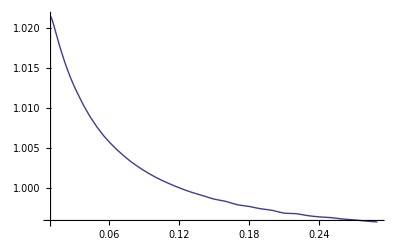

```mathematica
Plot[ {P131loopFinal[k,-0.9]/P13ΛCDM[k]}  , { k , .01 , .29}]
```

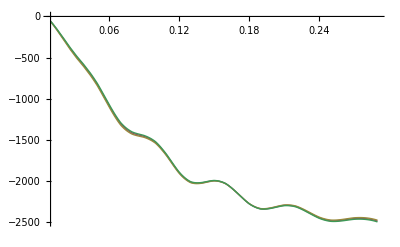

```mathematica
Plot[ {P13wSymma[k],P131loopFinal[k,-.9],P131loopFinal[k,-.8],P131loopFinal[k,-1]}  , { k , .01 , .29}]
```

```mathematica
.
```

#### P22

```mathematica
P22expandeda=(δ2sola[k,a](δ2sola[kpr,a]/.{k11-> k12,k21-> k22,a1-> a2}))/.δsubsa//Expand;
```

Let us define these k-dependent coefficients:

```mathematica
Clear[Coeff1b,Coeff2b,Coeff3b,Coeff4b,Coeff5b,Coeff6b]
```

```mathematica
Coeff1b=α[k,k21,k11] α[kpr,k22,k12] δ1k[k11] δ1k[k12] δ1k[k21] δ1k[k22];
Coeff2b=α[kpr,k22,k12] β[k,k11,k21] δ1k[k11] δ1k[k12] δ1k[k21] δ1k[k22];
Coeff3b=α[k,k21,k11] β[kpr,k12,k22] δ1k[k11] δ1k[k12] δ1k[k21] δ1k[k22];
Coeff4b=β[k,k11,k21] β[kpr,k12,k22] δ1k[k11] δ1k[k12] δ1k[k21] δ1k[k22];
```

These are the time-dependent factors in front, to be integrated in (∫_0)^a0 ⅆa2 (∫_0)^a0 ⅆa1

```mathematica
int1ba=Coefficient[P22expandeda,Coeff1b]/.Greensubsa//FullSimplify;
int2ba=Coefficient[P22expandeda,Coeff2b]/.Greensubsa//FullSimplify;
int3ba=Coefficient[P22expandeda,Coeff3b]/.Greensubsa//FullSimplify;
int4ba=Coefficient[P22expandeda,Coeff4b]/.Greensubsa//FullSimplify;
```

Check that I included everything: ok.

```mathematica
P22factorizeda=(int1ba Coeff1b+int2ba Coeff2b+int3ba Coeff3b+int4ba Coeff4b);
```

```mathematica
CheckTotala=(P22expandeda/.Greensubsa)-P22factorizeda//FullSimplify
```

0

```mathematica
int1Nba0 = NIntegrate[(Simplify[Coefficient[Normal[Series[ int1ba/.FunctionExpandSubs , {w , -1 , 1}]] (1+w) , (1+w)]] /.TimeSubsTot/.aini->ain)/.a->a0 , {a2 , alow, a0} , { a1, alow , a0}];
int1Nba1 =NIntegrate[(Simplify[Coefficient[Normal[Series[ int1ba/.FunctionExpandSubs , {w , -1 , 1}]] , (1+w)] ]/.TimeSubsTot/.aini->ain)/.a->a0 , {a2 , alow, a0} , { a1, alow , a0}];
```

```mathematica
int2Nba0 = NIntegrate[(Simplify[Coefficient[Normal[Series[ int2ba/.FunctionExpandSubs , {w , -1 , 1}]] (1+w) , (1+w)]] /.TimeSubsTot/.aini->ain)/.a->a0 , {a2 , alow, a0} , { a1, alow , a0}];
int2Nba1 =NIntegrate[(Simplify[Coefficient[Normal[Series[ int2ba/.FunctionExpandSubs , {w , -1 , 1}]] , (1+w)] ]/.TimeSubsTot/.aini->ain)/.a->a0 , {a2 , alow, a0} , { a1, alow , a0}];
```

```mathematica
int3Nba0 = NIntegrate[(Simplify[Coefficient[Normal[Series[ int3ba/.FunctionExpandSubs , {w , -1 , 1}]] (1+w) , (1+w)]] /.TimeSubsTot/.aini->ain)/.a->a0 , {a2 , alow, a0} , { a1, alow , a0}];
int3Nba1 =NIntegrate[(Simplify[Coefficient[Normal[Series[ int3ba/.FunctionExpandSubs , {w , -1 , 1}]] , (1+w)] ]/.TimeSubsTot/.aini->ain)/.a->a0 , {a2 , alow, a0} , { a1, alow , a0}];
```

```mathematica
int4Nba0 = NIntegrate[(Simplify[Coefficient[Normal[Series[ int4ba/.FunctionExpandSubs , {w , -1 , 1}]] (1+w) , (1+w)]] /.TimeSubsTot/.aini->ain)/.a->a0 , {a2 , alow, a0} , { a1, alow , a0}];
int4Nba1 =NIntegrate[(Simplify[Coefficient[Normal[Series[ int4ba/.FunctionExpandSubs , {w , -1 , 1}]] , (1+w)] ]/.TimeSubsTot/.aini->ain)/.a->a0 , {a2 , alow, a0} , { a1, alow , a0}];
```

Ok, now I can clearly do the time integrals. For the k - integrals, I first need to do the contractions, which amount to substituing things like δ1k[k11] δ1k[k2] -> δD[k11 + k2] P11[k2]. Here there is only one cotraction because the α and β are symmetric.

Notice that I first do the constraction and then I kill the δ - function.

```mathematica
P22Coeff1=2(((Coeff1b //.{δ1k[k11]δ1k[k12]-> P11[(k11.k11)^(1/2)] δD[k11+k12],δ1k[k21] δ1k[k22]-> P11[(k21.k21)^(1/2)]δD[k21+k22]}))/.{δD[k11+k12]-> 1,k12-> -k11}/.{δD[k21+k22]-> 1,k22-> -k21})//FullSimplify;
P22Coeff2=2(((Coeff2b //.{δ1k[k11]δ1k[k12]-> P11[(k11.k11)^(1/2)] δD[k11+k12],δ1k[k21] δ1k[k22]-> P11[(k21.k21)^(1/2)]δD[k21+k22]}))/.{δD[k11+k12]-> 1,k12-> -k11}/.{δD[k21+k22]-> 1,k22-> -k21})//FullSimplify;
P22Coeff3=2(((Coeff3b //.{δ1k[k11]δ1k[k12]-> P11[(k11.k11)^(1/2)] δD[k11+k12],δ1k[k21] δ1k[k22]-> P11[(k21.k21)^(1/2)]δD[k21+k22]}))/.{δD[k11+k12]-> 1,k12-> -k11}/.{δD[k21+k22]-> 1,k22-> -k21})//FullSimplify;
P22Coeff4=2(((Coeff4b //.{δ1k[k11]δ1k[k12]-> P11[(k11.k11)^(1/2)] δD[k11+k12],δ1k[k21] δ1k[k22]-> P11[(k21.k21)^(1/2)]δD[k21+k22]}))/.{δD[k11+k12]-> 1,k12-> -k11}/.{δD[k21+k22]-> 1,k22-> -k21})//FullSimplify;
```

Now I need to impose momentum conservation in the vertex. When I constract the δ functions, I need to be careful on the replacements of the k’s, as I do not want to replace in the wrong addendum (which might have a different δ function). The trick to do this safely is to chose to solve for the δ-functions in terms of the common variable of integration, so we call substitution only for the variables that are un-common in the sums.

```mathematica
P22Coeff1Simpl=( (P22Coeff1/.{α[a_,b_,c_]-> αfn[b,c]δD[b+c-a],β[a_,b_,c_]-> βfn[b,c]δD[b+c-a] })/.{δD[-k+k11+k21] -> 1})/.{k21->k-k11}/.k11->kint//FullSimplify;
P22Coeff2Simpl=( (P22Coeff2/.{α[a_,b_,c_]-> αfn[b,c]δD[b+c-a],β[a_,b_,c_]-> βfn[b,c]δD[b+c-a] })/.{δD[-k+k11+k21] -> 1})/.{k21->k-k11}/.k11->kint//FullSimplify;
P22Coeff3Simpl=( (P22Coeff3/.{α[a_,b_,c_]-> αfn[b,c]δD[b+c-a],β[a_,b_,c_]-> βfn[b,c]δD[b+c-a] })/.{δD[-k+k11+k21] -> 1})/.{k21->k-k11}/.k11->kint//FullSimplify;
P22Coeff4Simpl=( (P22Coeff4/.{α[a_,b_,c_]-> αfn[b,c]δD[b+c-a],β[a_,b_,c_]-> βfn[b,c]δD[b+c-a] })/.{δD[-k+k11+k21] -> 1})/.{k21->k-k11}/.k11->kint//FullSimplify;
```

We are done. Each of the above integrals must be integrated by ∫ⅆ^3 kint P22Coeff4Simpl. 
 Then, each of them, must be multiplied by the separately computed  (∫_0)^a0 ⅆa2 (∫_0)^a0 ⅆa1 int1b. Add them up, and we are done.

```mathematica
P22Integrand1Expand =Simplify[((kint^2(2π))/(2π)^3((Coefficient[ P22Coeff1Simpl/.αβSymmsubs, δD[-k+-kpr]]/.kpr->-k)/.vecSubs1)), {k>0, kint>0}]/.kintExpandSubs;
P22Integrand10[k_]=Coefficient[(1+w)P22Integrand1Expand , (1+w) ]/.kintSubs;
P22Integrand11[k_]=Coefficient[P22Integrand1Expand , (1+w) ]/.kintSubs;
```

```mathematica
P22IntegralTab10 =Monitor[ Table[ { k , NIntegrate[ P22Integrand10[k], { x,-1,1} , {kint, kir , 10}]} , { k , looptab2}],k];
```

```mathematica
P22IntegralTab11 = Monitor[ Table[ { k , NIntegrate[ P22Integrand11[k], { x,-1,1} , {kint, kir , 10}]} , { k , looptab2}] , k ];
```

```mathematica
P22FinalTab10 = Table[ { P22IntegralTab10[[i]][[1]] , int1Nba0  P22IntegralTab10[[i]][[2]]  } , { i , 1 , Length[P22IntegralTab10]}];
P22FinalTab11 = Table[ { P22IntegralTab10[[i]][[1]] , int1Nba1  P22IntegralTab10[[i]][[2]]  + int1Nba0 P22IntegralTab11[[i]][[2]]  } , { i , 1 , Length[P22IntegralTab10]}];
P22FinalInterp10 = Interpolation[P22FinalTab10];
P22FinalInterp11 = Interpolation[P22FinalTab11];
```

```mathematica
P22Integrand2Expand =Simplify[((kint^2(2π))/(2π)^3((Coefficient[ P22Coeff2Simpl/.αβSymmsubs, δD[-k+-kpr]]/.kpr->-k)/.vecSubs1)), {k>0, kint>0}]/.kintExpandSubs;
P22Integrand20[k_]=Coefficient[(1+w)P22Integrand2Expand , (1+w) ]/.kintSubs;
P22Integrand21[k_]=Coefficient[P22Integrand2Expand , (1+w) ]/.kintSubs;
```

```mathematica
P22IntegralTab20 =Monitor[ Table[ { k , NIntegrate[ P22Integrand20[k], { x,-1,1} , {kint, kir , 10}]} , { k , looptab2}],k];
```

```mathematica
P22IntegralTab21 = Monitor[ Table[ { k , NIntegrate[ P22Integrand21[k], { x,-1,1} , {kint, kir , 10}]} , { k , looptab2}] , k ];
```

```mathematica
P22FinalTab20 = Table[ { P22IntegralTab20[[i]][[1]] , int2Nba0  P22IntegralTab20[[i]][[2]]  } , { i , 1 , Length[P22IntegralTab20]}];
P22FinalTab21 = Table[ { P22IntegralTab20[[i]][[1]] , int2Nba1  P22IntegralTab20[[i]][[2]]  + int2Nba0 P22IntegralTab21[[i]][[2]]  } , { i , 1 , Length[P22IntegralTab20]}];
P22FinalInterp20 = Interpolation[P22FinalTab20];
P22FinalInterp21 = Interpolation[P22FinalTab21];
```

```mathematica
P22Integrand3Expand =Simplify[((kint^2(2π))/(2π)^3((Coefficient[ P22Coeff3Simpl/.αβSymmsubs, δD[-k+-kpr]]/.kpr->-k)/.vecSubs1)), {k>0, kint>0}]/.kintExpandSubs;
P22Integrand30[k_]=Coefficient[(1+w)P22Integrand3Expand , (1+w) ]/.kintSubs;
P22Integrand31[k_]=Coefficient[P22Integrand3Expand , (1+w) ]/.kintSubs;
```

```mathematica
P22IntegralTab30 =Monitor[ Table[ { k , NIntegrate[ P22Integrand30[k], { x,-1,1} , {kint, kir , 10}]} , { k , looptab2}],k];
```

```mathematica
P22IntegralTab31 = Monitor[ Table[ { k , NIntegrate[ P22Integrand31[k], { x,-1,1} , {kint, kir , 10}]} , { k , looptab2}] , k ];
```

```mathematica
P22FinalTab30 = Table[ { P22IntegralTab30[[i]][[1]] , int3Nba0  P22IntegralTab30[[i]][[2]]  } , { i , 1 , Length[P22IntegralTab30]}];
P22FinalTab31 = Table[ { P22IntegralTab30[[i]][[1]] , int3Nba1  P22IntegralTab30[[i]][[2]]  + int3Nba0 P22IntegralTab31[[i]][[2]]  } , { i , 1 , Length[P22IntegralTab30]}];
P22FinalInterp30 = Interpolation[P22FinalTab30];
P22FinalInterp31 = Interpolation[P22FinalTab31];
```

```mathematica
P22Integrand4Expand =Simplify[((kint^2(2π))/(2π)^3((Coefficient[ P22Coeff4Simpl/.αβSymmsubs, δD[-k+-kpr]]/.kpr->-k)/.vecSubs1)), {k>0, kint>0}]/.kintExpandSubs;
P22Integrand40[k_]=Coefficient[(1+w)P22Integrand4Expand , (1+w) ]/.kintSubs;
P22Integrand41[k_]=Coefficient[P22Integrand4Expand , (1+w) ]/.kintSubs;
```

```mathematica
P22IntegralTab40 =Monitor[ Table[ { k , NIntegrate[ P22Integrand40[k], { x,-1,1} , {kint, kir , 10}]} , { k , looptab2}],k];
```

```mathematica
P22IntegralTab41 = Monitor[ Table[ { k , NIntegrate[ P22Integrand41[k], { x,-1,1} , {kint, kir , 10}]} , { k , looptab2}] , k ];
```

```mathematica
P22FinalTab40 = Table[ { P22IntegralTab40[[i]][[1]] , int4Nba0  P22IntegralTab40[[i]][[2]]  } , { i , 1 , Length[P22IntegralTab40]}];
P22FinalTab41 = Table[ { P22IntegralTab40[[i]][[1]] , int4Nba1  P22IntegralTab40[[i]][[2]]  + int4Nba0 P22IntegralTab41[[i]][[2]]  } , { i , 1 , Length[P22IntegralTab40]}];
P22FinalInterp40 = Interpolation[P22FinalTab40];
P22FinalInterp41 = Interpolation[P22FinalTab41];
```

```mathematica
P22FinalInterp[k_,w_] = (P22FinalInterp10[k]+P22FinalInterp20[k]+P22FinalInterp30[k]+P22FinalInterp40[k]) + (1+w)(P22FinalInterp11[k] + P22FinalInterp21[k]+P22FinalInterp31[k]+P22FinalInterp41[k]);
```

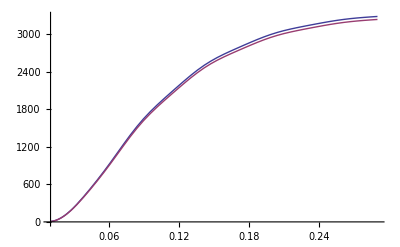

```mathematica
Plot[ {P22FinalInterp[k,-1],P22FinalInterp[k,-.9],P22wa[k]} , {k , .01  , .29}]
```

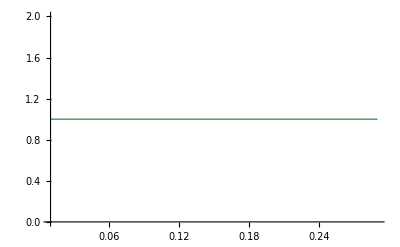

```mathematica
Plot[ {P22FinalInterp[k,-1.1]/P22wa[k],P22FinalInterp[k,-1]/P22wa[k],P22FinalInterp[k,-.9]/P22wa[k],P22wa[k]/P22wa[k]} , {k , .01  , .29}]
```

#### Ptotal

```mathematica
fromlin[k_,w_]=Coefficient[ ( Series[ (Dpl[1]/Dpl[ain])^2(P11N0[k] + (1+w)P11N1[k]) /.kintExpandSubs , {w , -1 , 1}]//Normal)/.kintSubs, 1+w];
```

```mathematica
Plin[k_ , w_] = ( Series[ (Dpl[1]/Dpl[ain])^2(P11N0[k] + (1+w)P11N1[k]) /.kintExpandSubs , {w , -1 , 1}]//Normal)/.kintSubs;
```

```mathematica
fromloop[k_,w_]= Coefficient[( Series[  P131loopFinal[k,w] + P22FinalInterp[k,w] /.kintExpandSubs , {w , -1 , 1}]//Normal)/.kintSubs , 1+w];
```

```mathematica
P1loopInterp[k_,w_] =  ( Series[ (Dpl[1]/Dpl[ain])^2(P11N0[k] + (1+w)P11N1[k]) + P131loopFinal[k,w] + P22FinalInterp[k,w] /.kintExpandSubs , {w , -1 , 1}]//Normal)/.kintSubs;
```

```mathematica
P1loopEFT[k_,w_,csdm_, xi_]= (P1loopInterp[k,w] - 2 k^2 csdm (1 + xi Subscript[Ω, Λ]/Subscript[Ω, m] (1 + w))  ( Series[ (Dpl[1]/Dpl[ain])^2(P11N0[k] + (1+w)P11N1[k])  /.kintExpandSubs , {w , -1 , 1}]//Normal)/.paramSubs)/.kintSubs;
```

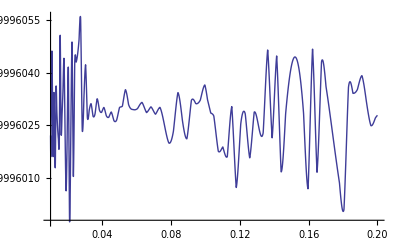

```mathematica
Plot[ {Plin[k , -0.9] /((Dpl[1]/Dpl[ain])^2(P11N0[k] + (1+w)P11N1[k]) /.kintExpandSubs)/.kintSubs /. w->-0.9} , { k , .01 , .2}]
```

```mathematica
Plot[ {P1loopInterp[k,-0.9] / PtotEFT[1][k, 0, 0]} , { k , .01 , .2}]
```

-Graphics-

```mathematica
Clear[Lin0,Lin1,oneloop0,oneloop1]
```

```mathematica
Lin0[k_] = ( Series[ (Dpl[1]/Dpl[ain])^2(P11N0[k] + (1+w)P11N1[k])  /.kintExpandSubs , {w , -1 , 1}]//Normal)/.kintSubs /.w->-1;
```

```mathematica
Lin1[k_,w_] =(1+w) Coefficient[( Series[ (Dpl[1]/Dpl[ain])^2(P11N0[k] + (1+w)P11N1[k])  /.kintExpandSubs , {w , -1 , 1}]//Normal)/.kintSubs , 1+w] ;
```

```mathematica
oneloop0[k_] = ( Series[  P131loopFinal[k,w] + P22FinalInterp[k,w] /.kintExpandSubs , {w , -1 , 1}]//Normal)/.kintSubs /.w->-1;
oneloop130[k_] = ( Series[  P131loopFinal[k,w]  /.kintExpandSubs , {w , -1 , 1}]//Normal)/.kintSubs /.w->-1;
oneloop220[k_] = ( Series[    P22FinalInterp[k,w] /.kintExpandSubs , {w , -1 , 1}]//Normal)/.kintSubs /.w->-1;
```

```mathematica
oneloop1[k_,w_] = Coefficient[( Series[  P131loopFinal[k,w] + P22FinalInterp[k,w] /.kintExpandSubs , {w , -1 , 1}]//Normal)/.kintSubs , 1+w](1+w) ;
oneloop131[k_,w_] = Coefficient[( Series[  P131loopFinal[k,w]  /.kintExpandSubs , {w , -1 , 1}]//Normal)/.kintSubs , 1+w](1+w) ;
oneloop221[k_,w_] = Coefficient[( Series[    P22FinalInterp[k,w] /.kintExpandSubs , {w , -1 , 1}]//Normal)/.kintSubs , 1+w](1+w) ;
```

```mathematica
Lin0wCDM[k_]=P11z0cs1N0[k];
oneloop0wCDM[k_]=P13wCDMN0[k] + P22wCDMN0[k];
Lin1wCDM[k_,w_]= (1+w)P11z0cs1N1[k];
oneloop1wCDM[k_,w_] = (1+w)(  P13wCDMN1[k] + P22wCDMN1[k] );
```

### Plots

InterpolatingFunction::dmval: Input value {-4.60511} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

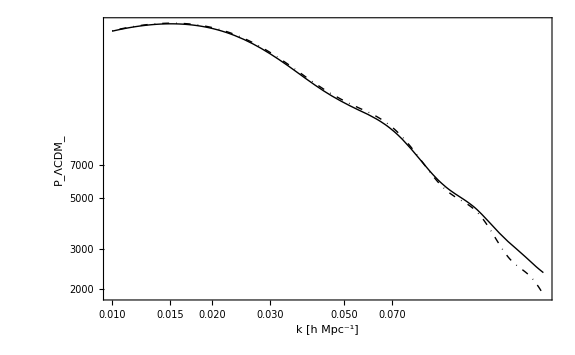

```mathematica
LogLogPlot[ { PTotΛ[k,cs1]  ,Lin0[k]} , { k , .01 , .2},PlotStyle->{{Black,Thick}, {Black , DotDashed}}    ,   Frame->True,FrameLabel->{"k [h Mpc^-1]", "P_ΛCDM_"},   BaseStyle->{FontSize->18}  ]
```

```mathematica
.2*2 π
```

1.25664

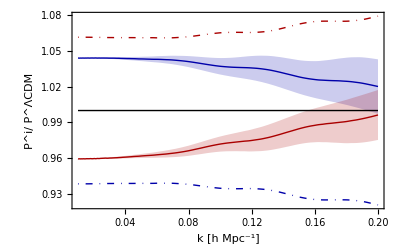

```mathematica
Plot[ {P1loopEFT[k,-.9,cs1, 0]/PTotΛ[k,cs1],P1loopEFT[k,-.9,cs1, 1]/PTotΛ[k,cs1], P1loopEFT[k,-.9,cs1, -1]/PTotΛ[k,cs1] ,P1loopEFT[k,-1.1,cs1, 0]/PTotΛ[k,cs1],P1loopEFT[k,-1.1,cs1, 1]/PTotΛ[k,cs1],P1loopEFT[k,-1.1,cs1, -1]/PTotΛ[k,cs1] , 1 , PTotwCDM[k,-.9,cs1, 0] /PTotΛ[k,cs1] , PTotwCDM[k,-1.1,cs1, 0] /PTotΛ[k,cs1] } , { k , .01 , .2},PlotStyle->{{Darker[Blue]} , {Opacity[0,Darker[Blue]]},{Opacity[0,Darker[Blue]]},{Darker[Red] },{Opacity[0,Darker[Red]],Dashed},{Opacity[0,Darker[Red]],Dashed},{Black,Thick} , {Darker[Blue],DotDashed, Thick},{Darker[Red],DotDashed, Thick}}, Filling->{  {1->{{2}, Opacity[.2,Darker[Blue]]}},{1->{{3}, Opacity[.2,Darker[Blue]]}} ,{4->{{5}, Opacity[.2,Darker[Red]]}},{4->{{6}, Opacity[.2,Darker[Red]]}}   }    ,   Frame->True,FrameLabel->{"k [h Mpc^-1]", "P^i/ P^ΛCDM"},   BaseStyle->{FontSize->18}  ]
```

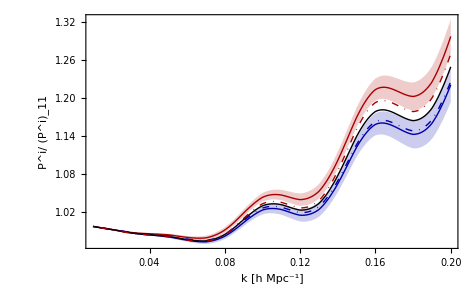

```mathematica
Plot[ {P1loopEFT[k,-.9,cs1, 0]/Plin[k,-.9],P1loopEFT[k,-.9,cs1, 1]/Plin[k,-.9], P1loopEFT[k,-.9,cs1, -1]/Plin[k,-.9] ,P1loopEFT[k,-1.1,cs1, 0]/Plin[k,-1.1],P1loopEFT[k,-1.1,cs1, 1]/Plin[k,-1.1],P1loopEFT[k,-1.1,cs1, -1]/Plin[k,-1.1] , PTotΛ[k,cs1]/Pmz0[-1.00][k]  , PTotwCDM[k,-.9,cs1, 0] /PlinwCDM[k,-.9] , PTotwCDM[k,-1.1,cs1, 0] /PlinwCDM[k,-1.1] } , { k , .01 , .2},PlotStyle->{{Darker[Blue]} , {Opacity[0,Darker[Blue]],Dashed},{Opacity[0,Darker[Blue]],Dashed},{Darker[Red]},{Opacity[0,Darker[Red]],Dashed},{Opacity[0,Darker[Red]],Dashed},{Black,Thick} , {Darker[Blue],DotDashed, Thick},{Darker[Red],DotDashed, Thick}}, Filling->{  {1->{{2}, Opacity[.2,Darker[Blue]]}},{1->{{3}, Opacity[.2,Darker[Blue]]}} ,{4->{{5}, Opacity[.2,Darker[Red]]}},{4->{{6}, Opacity[.2,Darker[Red]]}}   }    ,   Frame->True,FrameLabel->{"k [h Mpc^-1]", "P^i/ (P^i)_11"},   BaseStyle->{FontSize->18}    ]
```

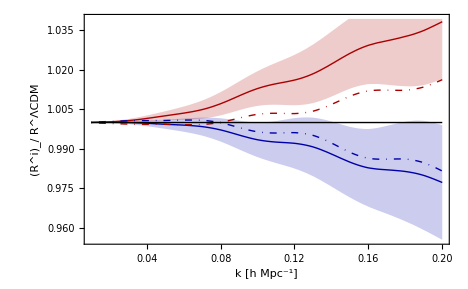

```mathematica
Plot[ {(P1loopEFT[k,-.9,cs1, 0]/Plin[k,-.9])/(PTotΛ[k,cs1]/Pmz0[-1.00][k]),(P1loopEFT[k,-.9,cs1, 1]/Plin[k,-.9])/(PTotΛ[k,cs1]/Pmz0[-1.00][k]), (P1loopEFT[k,-.9,cs1, -1]/Plin[k,-.9])/(PTotΛ[k,cs1]/Pmz0[-1.00][k]) ,(P1loopEFT[k,-1.1,cs1, 0]/Plin[k,-1.1])/(PTotΛ[k,cs1]/Pmz0[-1.00][k]),(P1loopEFT[k,-1.1,cs1, 1]/Plin[k,-1.1])/(PTotΛ[k,cs1]/Pmz0[-1.00][k]),(P1loopEFT[k,-1.1,cs1, -1]/Plin[k,-1.1] )/(PTotΛ[k,cs1]/Pmz0[-1.00][k]) , (PTotwCDM[k,-.9,cs1, 0] /PlinwCDM[k,-.9])/(PTotΛ[k,cs1]/Pmz0[-1.00][k]),(PTotwCDM[k,-1.1,cs1, 0] /PlinwCDM[k,-1.1])/(PTotΛ[k,cs1]/Pmz0[-1.00][k]) , 1 } , { k , .01 , .2},PlotStyle->{{Darker[Blue]} , {Opacity[0,Darker[Blue]],Dashed},{Opacity[0,Darker[Blue]],Dashed},{Darker[Red]},{Opacity[0,Darker[Red]],Dashed},{Opacity[0,Darker[Red]],Dashed}, {Darker[Blue],Thick,DotDashed},{Darker[Red],Thick,DotDashed}, {Black, Thick} }, Filling->{  {1->{{2}, Opacity[.2,Darker[Blue]]}},{1->{{3}, Opacity[.2,Darker[Blue]]}} ,{4->{{5}, Opacity[.2,Darker[Red]]}},{4->{{6}, Opacity[.2,Darker[Red]]}}   }    ,   Frame->True,FrameLabel->{"k [h Mpc^-1]", "(R^i)_/ R^ΛCDM"},   BaseStyle->{FontSize->18}    ]
```

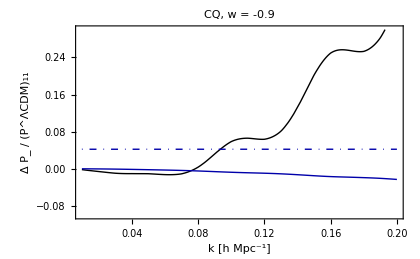

```mathematica
Plot[ {oneloop0[k]/Lin0[k] , Lin1[k,-0.9]/Lin0[k] ,  oneloop1[k,-0.9]/Lin0[k]} , { k , .01 , .2}, PlotStyle-> {   {Black,Thick}, {Darker[Blue], DotDashed } , {Darker[Blue]}   } , PlotRange->{-.1 , .3},   Frame->True,FrameLabel->{"k [h Mpc^-1]", "Δ P_ / (P^ΛCDM)_11"},   BaseStyle->{FontSize->18}, PlotLabel->"CQ, w = -0.9"]
```

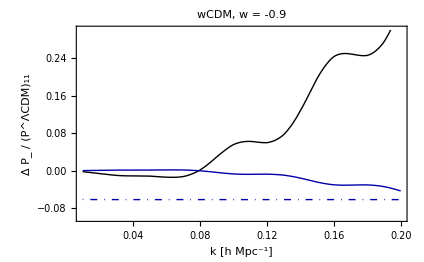

```mathematica
Plot[ { oneloop0wCDM[k]/Lin0[k] , Lin1wCDM[k,-0.9] /Lin0[k],  oneloop1wCDM[k,-0.9]/Lin0[k]} , { k , .01 , .2}, PlotStyle-> {   {Black,Thick}, {Darker[Blue], DotDashed } , {Darker[Blue]}   } , PlotRange->{-.1 , .3},   Frame->True,FrameLabel->{"k [h Mpc^-1]", "Δ P_ / (P^ΛCDM)_11"},   BaseStyle->{FontSize->18},PlotLabel->"wCDM, w = -0.9"]
```

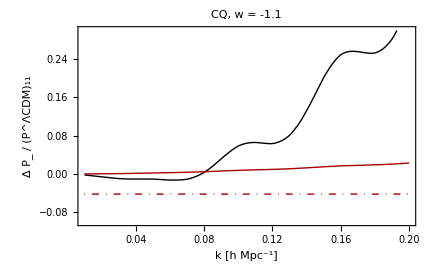

```mathematica
Plot[ {oneloop0[k]/Lin0[k] , Lin1[k,-1.1] /Lin0[k],  oneloop1[k,-1.1]/Lin0[k]} , { k , .01 , .2}, PlotStyle-> {   {Black,Thick}, {Darker[Red], DotDashed } , {Darker[Red]}   } , PlotRange->{-.1 , .3},   Frame->True,FrameLabel->{"k [h Mpc^-1]", "Δ P_ / (P^ΛCDM)_11"},   BaseStyle->{FontSize->18},PlotLabel->"CQ, w = -1.1"]
```

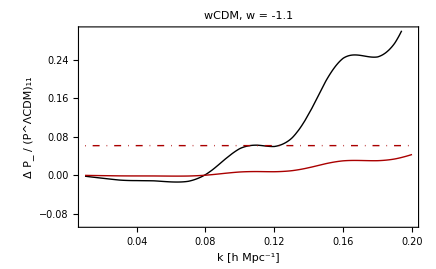

```mathematica
Plot[ { oneloop0wCDM[k]/Lin0[k] , Lin1wCDM[k,-1.1]/Lin0[k] ,  oneloop1wCDM[k,-1.1]/Lin0[k]} , { k , .01 , .2}, PlotStyle-> {   {Black,Thick}, {Darker[Red], DotDashed } , {Darker[Red]}   }, PlotRange->{-.1 , .3} ,   Frame->True,FrameLabel->{"k [h Mpc^-1]", "Δ P_ / (P^ΛCDM)_11"},   BaseStyle->{FontSize->18},PlotLabel->"wCDM, w = -1.1"]
```

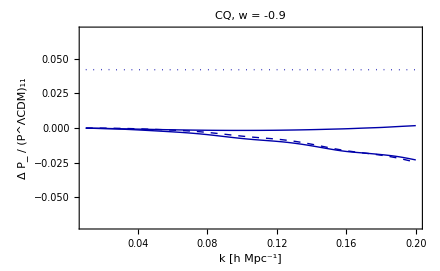

```mathematica
Plot[ {  oneloop1[k,-.9] /Lin0[k],oneloop131[k,-.9]/Lin0[k], oneloop221[k,-.9]/Lin0[k] ,Lin1[k,-.9]/Lin0[k]} , { k , .01 , .2}, PlotStyle-> {  {Darker[Blue], Thick}, {Darker[Blue] } , {Darker[Blue], Dashed}   , {Darker[Blue] , Dotted}}, PlotRange->{-0.07 , 0.07},   Frame->True,FrameLabel->{"k [h Mpc^-1]", "Δ P_ / (P^ΛCDM)_11"},   BaseStyle->{FontSize->18},PlotLabel->"CQ, w = -0.9" ]
```

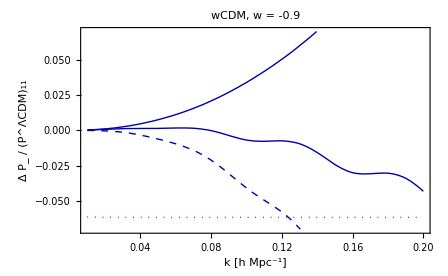

```mathematica
Plot[ {  oneloop1wCDM[k,-0.9] /Lin0[k],(1+-0.9)(  P13wCDMN1[k] )/Lin0[k], (1+-0.9)(  P22wCDMN1[k] )/Lin0[k] ,Lin1wCDM[k,-0.9]/Lin0[k]} , { k , .01 , .2}, PlotStyle-> {  {Darker[Blue], Thick}, {Darker[Blue] } , {Darker[Blue], Dashed}   , {Darker[Blue] , Dotted}} ,PlotRange->{-0.07 , 0.07},   Frame->True,FrameLabel->{"k [h Mpc^-1]", "Δ P_ / (P^ΛCDM)_11"},   BaseStyle->{FontSize->18},PlotLabel->"wCDM, w = -0.9"]
```

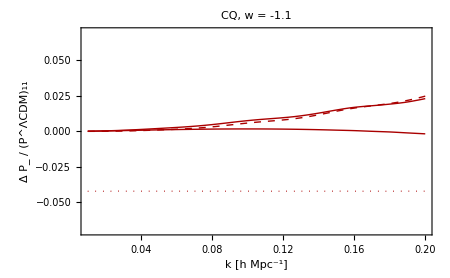

```mathematica
Plot[ {  oneloop1[k,-1.1]/Lin0[k] ,oneloop131[k,-1.1]/Lin0[k], oneloop221[k,-1.1]/Lin0[k], Lin1[k,-1.1] /Lin0[k]} , { k , .01 , .2}, PlotStyle-> {  {Darker[Red], Thick}, {Darker[Red] } , {Darker[Red], Dashed} ,  { Darker[Red] , Dotted}  } ,PlotRange->{-0.07 , 0.07},   Frame->True,FrameLabel->{"k [h Mpc^-1]", "Δ P_ / (P^ΛCDM)_11"},   BaseStyle->{FontSize->18},PlotLabel->"CQ, w = -1.1"]
```

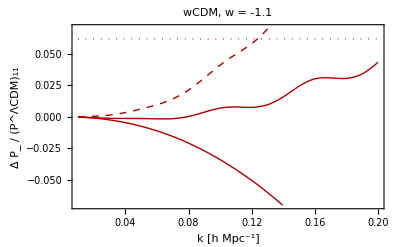

```mathematica
Plot[ {  oneloop1wCDM[k,-1.1] /Lin0[k],(1+-1.1)(  P13wCDMN1[k] )/Lin0[k], (1+-1.1)(  P22wCDMN1[k] )/Lin0[k] ,Lin1wCDM[k,-1.1]/Lin0[k]} , { k , .01 , .2}, PlotStyle-> {  {Darker[Red], Thick}, {Darker[Red] } , {Darker[Red], Dashed}   , {Darker[Red] , Dotted}},PlotRange->{-0.07 , 0.07},   Frame->True,FrameLabel->{"k [h Mpc^-1]", "Δ P_ / (P^ΛCDM)_11"},   BaseStyle->{FontSize->18},PlotLabel->"wCDM, w = -1.1" ]
```

```mathematica
cs1
```

1.25664

```mathematica
Manipulate[Plot[ {P1loopEFT[k,ww,cs, 0]/PTotwCDM[k,-0.9,cs1, 0] } , { k , .01 , .2},PlotStyle->{{Darker[Blue]} , {Opacity[0,Darker[Blue]]},{Opacity[0,Darker[Blue]]},{Darker[Red] },{Opacity[0,Darker[Red]],Dashed},{Opacity[0,Darker[Red]],Dashed},{Black,Thick} , {Darker[Blue],DotDashed, Thick},{Darker[Red],DotDashed, Thick}}   ,   Frame->True,FrameLabel->{"k [h Mpc^-1]", "(SuperscriptBox[P,  CQ][w ,  SuperscriptBox[SubscriptBox[OverscriptBox[c, _], A], 2]])/(SuperscriptBox[P, wCDM][-0.9, SuperscriptBox[SubscriptBox[OverscriptBox[c, _], m], 2]])"},   BaseStyle->{FontSize->18} , PlotRange->{.95,1.15} ] , { {ww,-.9} , -1.6 , -.7}, {{cs,cs1},1,3}]
```

```mathematica
1.81/cs1
```

1.44035

```mathematica
2.384/cs1
```

1.89713

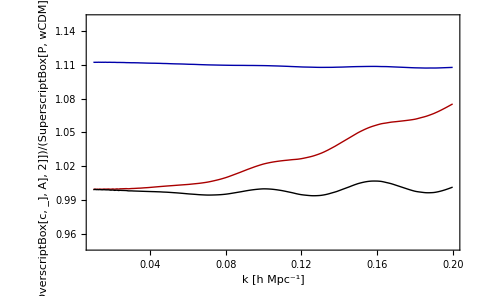

```mathematica
Plot[ {P1loopEFT[k,-.9,cs1, 0]/PTotwCDM[k,-0.9,cs1, 0], P1loopEFT[k,-1.15,cs1, 0]/PTotwCDM[k,-0.9,cs1, 0],P1loopEFT[k,-1.15,2.384, 0]/PTotwCDM[k,-0.9,cs1, 0] } , { k , .01 , .2},PlotStyle->{{Darker[Blue],Thick} ,{Darker[Red] ,Thick},{Black,Thick} , {Darker[Blue],DotDashed, Thick},{Darker[Red],DotDashed, Thick}}   ,   Frame->True,FrameLabel->{"k [h Mpc^-1]", "(SuperscriptBox[P,  CQ][w ,  SuperscriptBox[SubscriptBox[OverscriptBox[c, _], A], 2]])/(SuperscriptBox[P, wCDM][-0.9, SuperscriptBox[SubscriptBox[OverscriptBox[c, _], m], 2]])"},   BaseStyle->{FontSize->18} , PlotRange->{.95,1.15} ]
```

# computations using a, exact in 1+w, w1

#### Setup equations - this is the same, we will expand everything later

Let us write down the equations: these need to be adjusted to the correct equations. Also, the non - linear vertexes α and β need to be symmetrized. Integration over the k-varialbles is left implicit until the very last step (as well as substituting the label k with a 3-vector.)
 
all derivatives, or pr labels, are with respect to scale factor a

Note that the θ appearing below is really the rescaled Θ = - C/(ℋ f_+)θ

below α( k , k1, k2 ) = (2π)^3 δ^(3)( k - k_1 - k_2) α(k_1, k_2)

```mathematica
eqa={a D[δ[k,a], a]-fp[a] θ[k,a]== fp[a]/CC[a] α[k,k1,k2] δS[k1,a]θS[k2,a],a D[θ[k,a], a]-fp[a] θ[k,a]+ 3(Ωm CC[a])/(2 fp[a])(θ[k,a]-δ[k,a])==fp[a]/CC[a] β[k,k1,k2]θS[k1,a]θS[k2,a]};
```

```mathematica
αs[q1_,q2_] :=1 + (q1.q2)/2( 1/(q1.q1) + 1/(q2.q2));
α1[q1_,q2_] :=1 + q1.q2( 1/(q1.q1) );
βs[q1_,q2_] = (q1.q2 * (q1.q1 + q2.q2 + 2 q1.q2))/(2 q1.q1 * q2.q2);
```

δ2 Solution: let us put the integrations in k and η at the very end.

```mathematica
δ2sola[k_,a_]=Gδα[k,a,a1](α[k,k21,k11] fp[a1]δ1[k11,a1] θ1[k21,a1])/CC[a1]+Gδβ[k,a,a1](β[k,k11,k21]fp[a1]  θ1[k11,a1] θ1[k21,a1])/CC[a1];
θ2sola[k_,a_]=Gθα[k,a,a1](α[k,k21,k11] fp[a1]δ1[k11,a1] θ1[k21,a1])/CC[a1]+Gθβ[k,a,a1](β[k,k11,k21]fp[a1] θ1[k11,a1] θ1[k21,a1])/CC[a1];
```

δ3 Solution: : let us put the integration at the very end.

```mathematica
δ3sola[k_,a_]=Gδα[k,a,a2](α[k,k2,k1]fp[a2] (δ2[k1,a2] θ1[k2,a2]+δ1[k1,a2] θ2[k2,a2]))/CC[a2]+Gδβ[k,a,a2](β[k,k1,k2] fp[a2]2θ2[k1,a2] θ1[k2,a2])/CC[a2];
```

```mathematica
δ3solsuba[k_,a_]=δ3sola[k,a]/.{δ2[a___]-> δ2sola[a],θ2[a___]-> θ2sola[a]};
```

```mathematica
δ3solsubSimpa[k_,a_]=δ3solsuba[k,a]//FullSimplify;
```

This expression needs to be integrated in (∫_0)^a ⅆa2 (∫_0)^a2 ⅆa1 and also in the various momenta k's: basically, all repeated `indexes' must be integrated over.

Green’s Function

```mathematica
Gδαsola[k_,a_,a1_]=1/(a1 ( Dmpr[a1] Dpl[a1] - Dplpr[a1]Dm[a1]))(Dmpr[a1] Dpl[a] - Dplpr[a1] Dm[a])  ;
Gδβsola[k_,a_,a1_]=1/(a1 ( Dmpr[a1] Dpl[a1] - Dplpr[a1]Dm[a1]))((-fp[a1])/a1)(Dm[a1] Dpl[a] - Dpl[a1] Dm[a]);
Gθαsola[k_,a_,a1_]=1/(a1 ( Dmpr[a1] Dpl[a1] - Dplpr[a1]Dm[a1]))(Dmpr[a1] (a Dplpr[a])/fp[a] - Dplpr[a1] (a Dmpr[a])/fp[a]);
Gθβsola[k_,a_,a1_]=1/(a1 ( Dmpr[a1] Dpl[a1] - Dplpr[a1]Dm[a1]))((- fp[a1])/a1)(Dm[a1] (a Dplpr[a])/fp[a] - Dpl[a1](a Dmpr[a])/fp[a]);
```

Substitute Greens Functions

```mathematica
Greensubsa={Gδα[a___]-> Gδαsola[a],Gδβ[a___]-> Gδβsola[a],Gθα[a___]-> Gθαsola[a],Gθβ[a___]-> Gθβsola[a]};
```

```mathematica
δ3solGreena[k_,a_]=(δ3solsubSimpa[k,a]/.Greensubsa)//FullSimplify;
```

This expression needs to be integrated in (∫_0)^a0 ⅆa2 (∫_0)^a2 ⅆa1

It would be nice to be able to group the various integrals that factorize : time integral times a space integral. First let us  extract the time dependence

```mathematica
δsubsa={δ1[k_,a_]-> Dpl[a]/Dpl[aini] δ1k[k],θ1[k_,a_]-> (a Dplpr[a])/(fp[a]Dpl[aini])δ1k[k]};
```

```mathematica
FunctionExpandSubs = {Dpl[a_]->Dpl0[a] + (1+w) Dpl1[a], Dplpr[a_] -> Dplpr0[a] +(1+w) Dplpr1[a], fp[a_]->fp0[a] + (1+w) fp1[a], Dm[a_] -> Dm0[a] + ( 1 +w)Dm1[a], Dmpr[a_]->Dmpr0[a] + (1+w) Dmpr1[a], CC[a_] -> CC0[a]+(1+w)CC1[a]/.paramSubs};
```

```mathematica
TimeSubsTot ={  Dpl0[a_]-> Dp0[a] , Dpl1[a_]-> Dp1[a] , Dplpr0[a_]-> DplprN0[a], Dplpr1[a_]-> DplprN1[a] ,fp0[a_]-> fpl0[a], fp1[a_]-> fpl1[a], Dm0[a_]-> Dminus0[a],Dm1[a_]-> Dminus1[a],Dmpr0[a_]-> DDmN0[a] ,Dmpr1[a_]-> DDmN1[a],CC0[a_]-> C10[a],CC1[a_]-> C11[a]}/.paramSubs;
```

```mathematica
αβsubs= { αfn[x_,y_] -> α1[x,y] , βfn[x_,y_] -> βs[x,y]};
αβSymmsubs = { αfn[x_,y_] -> αs[x,y] , βfn[x_,y_] -> βs[x,y]};
vecSubs1={k->k*{0,0,1},kint->kint*{Sqrt[1-x^2],0,x}};
kintExpandSubs = {Dpl[a_]->Dpl0[a] + (1+w) Dpl1[a], P11[x__]-> P110[x] + (1+w)P111[x]};
kintSubs = {Dpl0[a_]-> Dp0[a] , Dpl1[a_]-> Dp1[a], P110[x__]-> P11N0[x] , P111[x__]->P11N1[x] };
```

#### P13 - symmetrization technique

Now, how do we separate the part to integrate in time from the ones to integrate in k. Let us see:

```mathematica
δ3Expandeda=(((δ3solGreena[k,a]/.δsubsa)//FullSimplify)//Expand);
```

Let us define these k-dependent coefficients:

```mathematica
Clear[Coeff1,Coeff2,Coeff3,Coeff4,Coeff5,Coeff6]
```

```mathematica
Coeff1=α[k,k2,k1]α[k1,k21,k11] δ1k[k2] δ1k[k11]δ1k[k21];
Coeff2=α[k,k2,k1]β[k1,k11,k21] δ1k[k2] δ1k[k11]δ1k[k21];
Coeff3=α[k,k2,k1]α[k2,k21,k11]δ1k[k1]δ1k[k11] δ1k[k21];
Coeff4=α[k,k2,k1]β[k2,k11,k21]δ1k[k1]δ1k[k11] δ1k[k21];
Coeff5=β[k,k1,k2]α[k1,k21,k11]δ1k[k2]δ1k[k11]  δ1k[k21];
Coeff6=β[k,k1,k2]β[k1,k11,k21]δ1k[k2]δ1k[k11]  δ1k[k21];
```

These are the time-dependent factors in front:

```mathematica
int1a=(Coefficient[δ3Expandeda,Coeff1]//FullSimplify);
int2a=(Coefficient[δ3Expandeda,Coeff2]//FullSimplify);
int3a=(Coefficient[δ3Expandeda,Coeff3]//FullSimplify);
int4a=(Coefficient[δ3Expandeda,Coeff4]//FullSimplify);
int5a=(Coefficient[δ3Expandeda,Coeff5]//FullSimplify);
int6a=(Coefficient[δ3Expandeda,Coeff6]//FullSimplify);
```

Check that I included everything: ok.

```mathematica
δ3factorizeda=(int1a Coeff1+int2a Coeff2+int3a Coeff3+int4a Coeff4+int5a Coeff5+int6a Coeff6);
```

```mathematica
CheckTotala=δ3Expandeda-δ3factorizeda//FullSimplify
```

0

Notice that the normalization of D_-does not matter in the int1...int6 above

```mathematica
TimeSubsa[1] = {Dpl[a_]->Dadiawa[1][a], Dplpr[a_] -> Dadiawa[1][a] fwa[1][a]/a, fp[a_]->fwa[1][a], Dm[a_] -> Dminus[1][a], Dmpr[a_]-> Dminus[1][a] * fminus[1][a] / a, CC[a_] -> C1[a]/.paramSubsw[1]};
```

```mathematica
int1Na[1] = NIntegrate[(int1a/.TimeSubsa[1]/.aini->ain)/.a->a0 , {a2 , alow, a0} , { a1, alow , a2}];
int2Na[1] = NIntegrate[(int2a/.TimeSubsa[1]/.aini->ain)/.a->a0 , {a2 , alow, a0} , { a1, alow , a2}];
int3Na[1] = NIntegrate[(int3a/.TimeSubsa[1]/.aini->ain)/.a->a0 , {a2 , alow, a0} , { a1, alow , a2}];
int4Na[1] = NIntegrate[(int4a/.TimeSubsa[1]/.aini->ain)/.a->a0 , {a2 , alow, a0} , { a1, alow , a2}];
int5Na[1] = NIntegrate[(int5a/.TimeSubsa[1]/.aini->ain)/.a->a0 , {a2 , alow, a0} , { a1, alow , a2}];
int6Na[1] = NIntegrate[(int6a/.TimeSubsa[1]/.aini->ain)/.a->a0 , {a2 , alow, a0} , { a1, alow , a2}];
```

Let’s symmetrize and redefine all of the momenta so that all of the terms have a factor of  δ1k[q1] δ1k[q2] δ1k[q3]

```mathematica
αβδsubs = { α[a_,b_,c_] -> δD[a - b -c] αfn[ b,c] ,  β[a_,b_,c_] -> δD[a - b -c] βfn[ b,c]};
```

```mathematica
Coeff1p[q1_,q2_,q3_] =((Coeff1/. αβδsubs)/.{k11->q1 , k2 -> q2 , k21->q3, k1->q4}) /. {δD[-q1-q3+q4] ->1 , q4->q1+q3};
Coeff2p[q1_,q2_,q3_] =((Coeff2/. αβδsubs)/.{k11->q1, k2->q2 , k21->q3, k1->q4})  /. {δD[-q1-q3+q4] ->1 , q4->q1 + q3};
Coeff3p[q1_,q2_,q3_] =((Coeff3/. αβδsubs)/.{k1->q1, k11->q2 , k21->q3 , k2->q4})   /.{ δD[-q2-q3+q4] -> 1 , q4->q2+q3};
Coeff4p[q1_,q2_,q3_] =((Coeff4/. αβδsubs)/.{k1->q1 , k11->q2 , k21->q3 , k2->q4})   /.{δD[-q2-q3+q4]->1 , q4->q2+q3 };
Coeff5p[q1_,q2_,q3_] =((Coeff5/. αβδsubs)/.{k11->q1 , k2->q2 , k21->q3 , k1->q4})   /.{δD[-q1-q3+q4]->1 , q4->q1 + q3 };
Coeff6p[q1_,q2_,q3_] =((Coeff6/. αβδsubs)/.{k11->q1 , k2->q2 , k21->q3, k1->q4})   /.{δD[-q1-q3+q4]->1 , q4->q1 + q3 };
```

```mathematica
Coeff1Sym[q1_,q2_,q3_] = 1/6( Coeff1p[q1,q2,q3] + Coeff1p[q1,q3,q2] + Coeff1p[q2,q1,q3] + Coeff1p[q2,q3,q1] + Coeff1p[q3,q2,q1] + Coeff1p[q3,q1,q2])//Simplify;
Coeff2Sym[q1_,q2_,q3_] = 1/6( Coeff2p[q1,q2,q3] + Coeff2p[q1,q3,q2] + Coeff2p[q2,q1,q3] + Coeff2p[q2,q3,q1] + Coeff2p[q3,q2,q1] + Coeff2p[q3,q1,q2])//Simplify;
Coeff3Sym[q1_,q2_,q3_] = 1/6( Coeff3p[q1,q2,q3] + Coeff3p[q1,q3,q2] + Coeff3p[q2,q1,q3] + Coeff3p[q2,q3,q1] + Coeff3p[q3,q2,q1] + Coeff3p[q3,q1,q2])//Simplify;
Coeff4Sym[q1_,q2_,q3_] = 1/6( Coeff4p[q1,q2,q3] + Coeff4p[q1,q3,q2] + Coeff4p[q2,q1,q3] + Coeff4p[q2,q3,q1] + Coeff4p[q3,q2,q1] + Coeff4p[q3,q1,q2])//Simplify;
Coeff5Sym[q1_,q2_,q3_] = 1/6( Coeff5p[q1,q2,q3] + Coeff5p[q1,q3,q2] + Coeff5p[q2,q1,q3] + Coeff5p[q2,q3,q1] + Coeff5p[q3,q2,q1] + Coeff5p[q3,q1,q2])//Simplify;
Coeff6Sym[q1_,q2_,q3_] = 1/6( Coeff6p[q1,q2,q3] + Coeff6p[q1,q3,q2] + Coeff6p[q2,q1,q3] + Coeff6p[q2,q3,q1] + Coeff6p[q3,q2,q1] + Coeff6p[q3,q1,q2])//Simplify;
```

If we write δ^(3)( k , a ) = ∫_(q_1 q_2 q_3) (2π)^3 δ( k - q_1-q_2-q_3) F_3^s(q_1,q_2,q_3;a) δ(q_1,a_in) δ(q_2,a_in) δ(q_3,a_in) , then the contribution to the power spectrum is P_13= 2 *3(D_+(η0))/(D_+(ηin)) ∫_q  F_3^s(k , q , -q ; a ) P_11^in(k) P_11^in(q) (the 2 is from δ^(1)δ^(3) + δ^(3)δ^(1), and the 3 is from the number of contractions.

```mathematica
FCoeff1 = Coefficient[ Coeff1Sym[q1,q2,q3] , δ1k[q1] δ1k[q2] δ1k[q3] δD[k-q1-q2-q3]] /. {q1->k , q2->q , q3->-q}/.{αfn[q,-q] ->0  , αfn[-q,q]->0,βfn[q,-q] ->0  , βfn[-q,q]->0} ;
```

```mathematica
FCoeff2 = Coefficient[ Coeff2Sym[q1,q2,q3] , δ1k[q1] δ1k[q2] δ1k[q3] δD[k-q1-q2-q3]] /. {q1->k , q2->q , q3->-q}/.{αfn[q,-q] ->0  , αfn[-q,q]->0,βfn[q,-q] ->0  , βfn[-q,q]->0};
```

```mathematica
FCoeff3 = Coefficient[ Coeff3Sym[q1,q2,q3] , δ1k[q1] δ1k[q2] δ1k[q3] δD[k-q1-q2-q3]] /. {q1->k , q2->q , q3->-q}/.{αfn[q,-q] ->0  , αfn[-q,q]->0,βfn[q,-q] ->0  , βfn[-q,q]->0};
```

```mathematica
FCoeff4 = Coefficient[ Coeff4Sym[q1,q2,q3] , δ1k[q1] δ1k[q2] δ1k[q3] δD[k-q1-q2-q3]] /. {q1->k , q2->q , q3->-q}/.{αfn[q,-q] ->0  , αfn[-q,q]->0,βfn[q,-q] ->0  , βfn[-q,q]->0};
```

```mathematica
FCoeff5 = Coefficient[ Coeff5Sym[q1,q2,q3] , δ1k[q1] δ1k[q2] δ1k[q3] δD[k-q1-q2-q3]] /. {q1->k , q2->q , q3->-q}/.{αfn[q,-q] ->0  , αfn[-q,q]->0,βfn[q,-q] ->0  , βfn[-q,q]->0};
```

```mathematica
FCoeff6 = Coefficient[ Coeff6Sym[q1,q2,q3] , δ1k[q1] δ1k[q2] δ1k[q3] δD[k-q1-q2-q3]] /. {q1->k , q2->q , q3->-q}/.{αfn[q,-q] ->0  , αfn[-q,q]->0,βfn[q,-q] ->0  , βfn[-q,q]->0};
```

We are done. Each of the above integrals must be integrated by ∫ⅆ^3 kint P13Coeff1Final. Then, each of them, must be multiplied by the separately computed  (∫_0)^a0 ⅆa2 (∫_0)^a2 ⅆa1 int1. Add them up, and we are done.

Define the integrands; the extra factor of ⅇ^(η0-ηin) comes from contracting with δ^(1)(k,a_0) = δ^(1)(k,a_in) *D_+(a_0) / D_+(a_in)

```mathematica
αβsubs= { αfn[x_,y_] -> α1[x,y] , βfn[x_,y_] -> βs[x,y]};
```

```mathematica
vecSubs1={k->k*{0,0,1},kint->kint*{Sqrt[1-x^2],0,x}};
```

```mathematica
P13Integrand1[1][k_]=2* 3(Dadiawa[1][1])/(Dadiawa[1][ain]) Simplify[((kint^2(2π))/(2π)^3(  (P11[(k.k)^(1/2)] P11[(kint.kint)^(1/2)]FCoeff1/.αβsubs/.q->kint)/.vecSubs1)/.P11->P11adiaSubs[1]), {k>0, kint>0}];
P13Integrand2[1][k_]=2* 3 (Dadiawa[1][1])/(Dadiawa[1][ain])Simplify[((kint^2(2π))/(2π)^3(  (P11[(k.k)^(1/2)] P11[(kint.kint)^(1/2)]FCoeff2/.αβsubs/.q->kint)/.vecSubs1)/.P11->P11adiaSubs[1]), {k>0, kint>0}];
P13Integrand3[1][k_]=2* 3 (Dadiawa[1][1])/(Dadiawa[1][ain])Simplify[((kint^2(2π))/(2π)^3(  (P11[(k.k)^(1/2)] P11[(kint.kint)^(1/2)]FCoeff3/.αβsubs/.q->kint)/.vecSubs1)/.P11->P11adiaSubs[1]), {k>0, kint>0}];
P13Integrand4[1][k_]=2* 3 (Dadiawa[1][1])/(Dadiawa[1][ain])Simplify[((kint^2(2π))/(2π)^3(  (P11[(k.k)^(1/2)] P11[(kint.kint)^(1/2)]FCoeff4/.αβsubs/.q->kint)/.vecSubs1)/.P11->P11adiaSubs[1]), {k>0, kint>0}];
P13Integrand5[1][k_]=2* 3 (Dadiawa[1][1])/(Dadiawa[1][ain])Simplify[((kint^2(2π))/(2π)^3(  (P11[(k.k)^(1/2)] P11[(kint.kint)^(1/2)]FCoeff5/.αβsubs/.q->kint)/.vecSubs1)/.P11->P11adiaSubs[1]), {k>0, kint>0}];
P13Integrand6[1][k_]=2* 3 (Dadiawa[1][1])/(Dadiawa[1][ain])Simplify[((kint^2(2π))/(2π)^3(  (P11[(k.k)^(1/2)] P11[(kint.kint)^(1/2)]FCoeff6/.αβsubs/.q->kint)/.vecSubs1)/.P11->P11adiaSubs[1]), {k>0, kint>0}];
```

```mathematica
P13LoopTab1[1] = Table[ { k , NIntegrate[ P13Integrand1[1][k] , { x,-1,1} , {kint, kir , 10}] } , { k , looptab2}];
P13LoopTab2[1] = Table[ { k , NIntegrate[ P13Integrand2[1][k] , { x,-1,1} , {kint, kir , 10}] } , { k , looptab2}];
P13LoopTab3[1] = Table[ { k , NIntegrate[ P13Integrand3[1][k] , { x,-1,1} , {kint, kir , 10}] } , { k , looptab2}];
P13LoopTab4[1] = Table[ { k , NIntegrate[ P13Integrand4[1][k] , { x,-1,1} , {kint, kir , 10}] } , { k , looptab2}];
P13LoopTab5[1] = Table[ { k , NIntegrate[ P13Integrand5[1][k] , { x,-1,1} , {kint, kir , 10}] } , { k , looptab2}];
P13LoopTab6[1] = Table[ { k , NIntegrate[ P13Integrand6[1][k] , { x,-1,1} , {kint, kir , 10}] } , { k , looptab2}];
```

```mathematica
P13LoopInterp1[1] = Interpolation[ P13LoopTab1[1]];
P13LoopInterp2[1] = Interpolation[ P13LoopTab2[1]];
P13LoopInterp3[1] = Interpolation[ P13LoopTab3[1]];
P13LoopInterp4[1] = Interpolation[ P13LoopTab4[1]];
P13LoopInterp5[1] = Interpolation[ P13LoopTab5[1]];
P13LoopInterp6[1] = Interpolation[ P13LoopTab6[1]];
```

```mathematica
P13wa[1][k_] = int1Na[1] P13LoopInterp1[1][k] + int2Na[1] P13LoopInterp2[1][k] + int3Na[1] P13LoopInterp3[1][k] + int4Na[1] P13LoopInterp4[1][k] + int5Na[1] P13LoopInterp5[1][k] + int6Na[1] P13LoopInterp6[1][k];
```

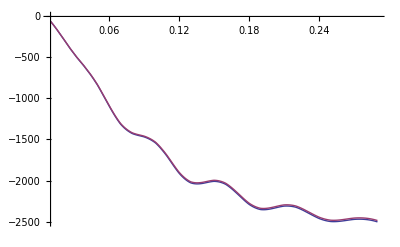

```mathematica
Plot[ {P13wa[1][k], P131loopFinal[k,-0.9]} , { k , .01 , .29}]
```

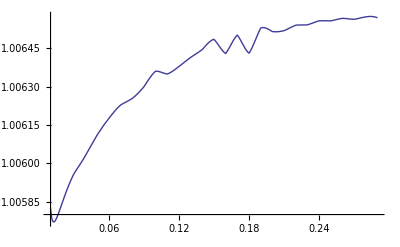

```mathematica
Plot[ {P13wa[1][k]/ P131loopFinal[k,-0.9]} , { k , .01 , .29}]
```

#### P22

```mathematica
P22expandeda=(δ2sola[k,a](δ2sola[kpr,a]/.{k11-> k12,k21-> k22,a1-> a2}))/.δsubsa//Expand;
```

Let us define these k-dependent coefficients:

```mathematica
Clear[Coeff1b,Coeff2b,Coeff3b,Coeff4b,Coeff5b,Coeff6b]
```

```mathematica
Coeff1b=α[k,k21,k11] α[kpr,k22,k12] δ1k[k11] δ1k[k12] δ1k[k21] δ1k[k22];
Coeff2b=α[kpr,k22,k12] β[k,k11,k21] δ1k[k11] δ1k[k12] δ1k[k21] δ1k[k22];
Coeff3b=α[k,k21,k11] β[kpr,k12,k22] δ1k[k11] δ1k[k12] δ1k[k21] δ1k[k22];
Coeff4b=β[k,k11,k21] β[kpr,k12,k22] δ1k[k11] δ1k[k12] δ1k[k21] δ1k[k22];
```

These are the time-dependent factors in front, to be integrated in (∫_0)^a0 ⅆa2 (∫_0)^a0 ⅆa1

```mathematica
int1ba=Coefficient[P22expandeda,Coeff1b]/.Greensubsa//FullSimplify;
int2ba=Coefficient[P22expandeda,Coeff2b]/.Greensubsa//FullSimplify;
int3ba=Coefficient[P22expandeda,Coeff3b]/.Greensubsa//FullSimplify;
int4ba=Coefficient[P22expandeda,Coeff4b]/.Greensubsa//FullSimplify;
```

Check that I included everything: ok.

```mathematica
P22factorizeda=(int1ba Coeff1b+int2ba Coeff2b+int3ba Coeff3b+int4ba Coeff4b);
```

```mathematica
CheckTotala=(P22expandeda/.Greensubsa)-P22factorizeda//FullSimplify
```

0

```mathematica
int1Nba[1] = NIntegrate[(int1ba/.TimeSubsa[1]/.aini->ain)/.a->a0 , {a2 , alow, a0} , { a1, alow , a0}];
int2Nba[1] = NIntegrate[(int2ba/.TimeSubsa[1]/.aini->ain)/.a->a0 , {a2 , alow, a0} , { a1, alow , a0}];
int3Nba[1] = NIntegrate[(int3ba/.TimeSubsa[1]/.aini->ain)/.a->a0 , {a2 , alow, a0} , { a1, alow , a0}];
int4Nba[1] = NIntegrate[(int4ba/.TimeSubsa[1]/.aini->ain)/.a->a0 , {a2 , alow, a0} , { a1, alow , a0}];
```

Ok, now I can clearly do the time integrals. For the k - integrals, I first need to do the contractions, which amount to substituing things like δ1k[k11] δ1k[k2] -> δD[k11 + k2] P11[k2]. Here there is only one cotraction because the α and β are symmetric.

Notice that I first do the constraction and then I kill the δ - function.

```mathematica
P22Coeff1=2(((Coeff1b //.{δ1k[k11]δ1k[k12]-> P11[(k11.k11)^(1/2)] δD[k11+k12],δ1k[k21] δ1k[k22]-> P11[(k21.k21)^(1/2)]δD[k21+k22]}))/.{δD[k11+k12]-> 1,k12-> -k11}/.{δD[k21+k22]-> 1,k22-> -k21})//FullSimplify;
P22Coeff2=2(((Coeff2b //.{δ1k[k11]δ1k[k12]-> P11[(k11.k11)^(1/2)] δD[k11+k12],δ1k[k21] δ1k[k22]-> P11[(k21.k21)^(1/2)]δD[k21+k22]}))/.{δD[k11+k12]-> 1,k12-> -k11}/.{δD[k21+k22]-> 1,k22-> -k21})//FullSimplify;
P22Coeff3=2(((Coeff3b //.{δ1k[k11]δ1k[k12]-> P11[(k11.k11)^(1/2)] δD[k11+k12],δ1k[k21] δ1k[k22]-> P11[(k21.k21)^(1/2)]δD[k21+k22]}))/.{δD[k11+k12]-> 1,k12-> -k11}/.{δD[k21+k22]-> 1,k22-> -k21})//FullSimplify;
P22Coeff4=2(((Coeff4b //.{δ1k[k11]δ1k[k12]-> P11[(k11.k11)^(1/2)] δD[k11+k12],δ1k[k21] δ1k[k22]-> P11[(k21.k21)^(1/2)]δD[k21+k22]}))/.{δD[k11+k12]-> 1,k12-> -k11}/.{δD[k21+k22]-> 1,k22-> -k21})//FullSimplify;
```

Now I need to impose momentum conservation in the vertex. When I constract the δ functions, I need to be careful on the replacements of the k’s, as I do not want to replace in the wrong addendum (which might have a different δ function). The trick to do this safely is to chose to solve for the δ-functions in terms of the common variable of integration, so we call substitution only for the variables that are un-common in the sums.

```mathematica
P22Coeff1Simpl=( (P22Coeff1/.{α[a_,b_,c_]-> αfn[b,c]δD[b+c-a],β[a_,b_,c_]-> βfn[b,c]δD[b+c-a] })/.{δD[-k+k11+k21] -> 1})/.{k21->k-k11}/.k11->kint//FullSimplify;
P22Coeff2Simpl=( (P22Coeff2/.{α[a_,b_,c_]-> αfn[b,c]δD[b+c-a],β[a_,b_,c_]-> βfn[b,c]δD[b+c-a] })/.{δD[-k+k11+k21] -> 1})/.{k21->k-k11}/.k11->kint//FullSimplify;
P22Coeff3Simpl=( (P22Coeff3/.{α[a_,b_,c_]-> αfn[b,c]δD[b+c-a],β[a_,b_,c_]-> βfn[b,c]δD[b+c-a] })/.{δD[-k+k11+k21] -> 1})/.{k21->k-k11}/.k11->kint//FullSimplify;
P22Coeff4Simpl=( (P22Coeff4/.{α[a_,b_,c_]-> αfn[b,c]δD[b+c-a],β[a_,b_,c_]-> βfn[b,c]δD[b+c-a] })/.{δD[-k+k11+k21] -> 1})/.{k21->k-k11}/.k11->kint//FullSimplify;
```

We are done. Each of the above integrals must be integrated by ∫ⅆ^3 kint P22Coeff4Simpl. 
 Then, each of them, must be multiplied by the separately computed  (∫_0)^a0 ⅆa2 (∫_0)^a0 ⅆa1 int1b. Add them up, and we are done.

```mathematica
αβSymmsubs = { αfn[x_,y_] -> αs[x,y] , βfn[x_,y_] -> βs[x,y]};
```

```mathematica
P22Integrand1Final[1][k_]=Simplify[((kint^2(2π))/(2π)^3((Coefficient[ P22Coeff1Simpl/.αβSymmsubs, δD[-k+-kpr]]/.kpr->-k)/.vecSubs1)/.P11->P11adiaSubs[1]), {k>0, kint>0}];
P22Integrand2Final[1][k_]=Simplify[((kint^2(2π))/(2π)^3((Coefficient[ P22Coeff2Simpl/.αβSymmsubs, δD[-k+-kpr]]/.kpr->-k)/.vecSubs1)/.P11->P11adiaSubs[1]), {k>0, kint>0}];
P22Integrand3Final[1][k_]=Simplify[((kint^2(2π))/(2π)^3((Coefficient[ P22Coeff3Simpl/.αβSymmsubs, δD[-k+-kpr]]/.kpr->-k)/.vecSubs1)/.P11->P11adiaSubs[1]), {k>0, kint>0}];
P22Integrand4Final[1][k_]=Simplify[((kint^2(2π))/(2π)^3((Coefficient[ P22Coeff4Simpl/.αβSymmsubs, δD[-k+-kpr]]/.kpr->-k)/.vecSubs1)/.P11->P11adiaSubs[1]), {k>0, kint>0}];
```

```mathematica
P22FinalTaba1[1] = Monitor[ Table[ {k ,  NIntegrate[ P22Integrand1Final[1][k] , { x,-1,1} , {kint, kir , 10}] ,   NIntegrate[ P22Integrand2Final[1][k] , { x,-1,1} , {kint, kir , 10}],   NIntegrate[ P22Integrand3Final[1][k] , { x,-1,1} , {kint, kir , 10}],  NIntegrate[ P22Integrand4Final[1][k] , { x,-1,1} , {kint, kir , 10}] } , { k , looptab2}] , k ];
```

```mathematica
P22FinalTaba[1] = Table[ { P22FinalTaba1[1][[i]][[1]] , int1Nba[1] P22FinalTaba1[1][[i]][[2]] + int2Nba[1] P22FinalTaba1[1][[i]][[3]] + int3Nba[1] P22FinalTaba1[1][[i]][[4]] + int4Nba[1] P22FinalTaba1[1][[i]][[5]] } ,  { i, 1, Length[P22FinalTaba1[1]]}] ;
```

```mathematica
P22wa[1]= Interpolation[P22FinalTaba[1]];
```

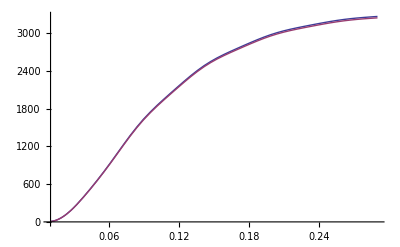

```mathematica
Plot[{ P22wa[1][k],P22FinalInterp[k,-.9]} , { k , .01 , .29}]
```

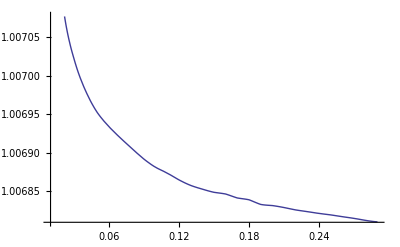

```mathematica
Plot[{ P22wa[1][k]/P22FinalInterp[k,-.9]} , { k , .01 , .29}]
```

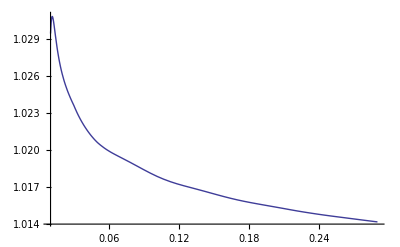

```mathematica
Plot[ P22wa[k]/P22ΛCDM[k] , { k , .01 , .29}]
```

### Ptotal

```mathematica
PtotEFT[1][k_, csdm_, xi_] = ((Dadiawa[1][1])/(Dadiawa[1][ain]))^2 P11adiaSubs[1][k] + P13wa[1][k] + P22wa[1][k] - 2 k^2 csdm (1 + xi Subscript[Ω, Λ]/Subscript[Ω, m] (1 + w))  ((Dadiawa[1][1])/(Dadiawa[1][ain]))^2 P11adiaSubs[1][k]  /. paramSubsw[1];
```

```mathematica
P1loopEFTexactw[1][k_] =  P13wa[1][k] + P22wa[1][k] ;
```

```mathematica
P11[1][k_] = ((Dadiawa[1][1])/(Dadiawa[1][ain]))^2 P11adiaSubs[1][k];
```

# computations using a, exact in 1+w, w2

#### Setup equations - this is the same, we will expand everything later

Let us write down the equations: these need to be adjusted to the correct equations. Also, the non - linear vertexes α and β need to be symmetrized. Integration over the k-varialbles is left implicit until the very last step (as well as substituting the label k with a 3-vector.)
 
all derivatives, or pr labels, are with respect to scale factor a

Note that the θ appearing below is really the rescaled Θ = - C/(ℋ f_+)θ

below α( k , k1, k2 ) = (2π)^3 δ^(3)( k - k_1 - k_2) α(k_1, k_2)

```mathematica
eqa={a D[δ[k,a], a]-fp[a] θ[k,a]== fp[a]/CC[a] α[k,k1,k2] δS[k1,a]θS[k2,a],a D[θ[k,a], a]-fp[a] θ[k,a]+ 3(Ωm CC[a])/(2 fp[a])(θ[k,a]-δ[k,a])==fp[a]/CC[a] β[k,k1,k2]θS[k1,a]θS[k2,a]};
```

```mathematica
αs[q1_,q2_] :=1 + (q1.q2)/2( 1/(q1.q1) + 1/(q2.q2));
α1[q1_,q2_] :=1 + q1.q2( 1/(q1.q1) );
βs[q1_,q2_] = (q1.q2 * (q1.q1 + q2.q2 + 2 q1.q2))/(2 q1.q1 * q2.q2);
```

δ2 Solution: let us put the integrations in k and η at the very end.

```mathematica
δ2sola[k_,a_]=Gδα[k,a,a1](α[k,k21,k11] fp[a1]δ1[k11,a1] θ1[k21,a1])/CC[a1]+Gδβ[k,a,a1](β[k,k11,k21]fp[a1]  θ1[k11,a1] θ1[k21,a1])/CC[a1];
θ2sola[k_,a_]=Gθα[k,a,a1](α[k,k21,k11] fp[a1]δ1[k11,a1] θ1[k21,a1])/CC[a1]+Gθβ[k,a,a1](β[k,k11,k21]fp[a1] θ1[k11,a1] θ1[k21,a1])/CC[a1];
```

δ3 Solution: : let us put the integration at the very end.

```mathematica
δ3sola[k_,a_]=Gδα[k,a,a2](α[k,k2,k1]fp[a2] (δ2[k1,a2] θ1[k2,a2]+δ1[k1,a2] θ2[k2,a2]))/CC[a2]+Gδβ[k,a,a2](β[k,k1,k2] fp[a2]2θ2[k1,a2] θ1[k2,a2])/CC[a2];
```

```mathematica
δ3solsuba[k_,a_]=δ3sola[k,a]/.{δ2[a___]-> δ2sola[a],θ2[a___]-> θ2sola[a]};
```

```mathematica
δ3solsubSimpa[k_,a_]=δ3solsuba[k,a]//FullSimplify;
```

This expression needs to be integrated in (∫_0)^a ⅆa2 (∫_0)^a2 ⅆa1 and also in the various momenta k's: basically, all repeated `indexes' must be integrated over.

Green’s Function

```mathematica
Gδαsola[k_,a_,a1_]=1/(a1 ( Dmpr[a1] Dpl[a1] - Dplpr[a1]Dm[a1]))(Dmpr[a1] Dpl[a] - Dplpr[a1] Dm[a])  ;
Gδβsola[k_,a_,a1_]=1/(a1 ( Dmpr[a1] Dpl[a1] - Dplpr[a1]Dm[a1]))((-fp[a1])/a1)(Dm[a1] Dpl[a] - Dpl[a1] Dm[a]);
Gθαsola[k_,a_,a1_]=1/(a1 ( Dmpr[a1] Dpl[a1] - Dplpr[a1]Dm[a1]))(Dmpr[a1] (a Dplpr[a])/fp[a] - Dplpr[a1] (a Dmpr[a])/fp[a]);
Gθβsola[k_,a_,a1_]=1/(a1 ( Dmpr[a1] Dpl[a1] - Dplpr[a1]Dm[a1]))((- fp[a1])/a1)(Dm[a1] (a Dplpr[a])/fp[a] - Dpl[a1](a Dmpr[a])/fp[a]);
```

Substitute Greens Functions

```mathematica
Greensubsa={Gδα[a___]-> Gδαsola[a],Gδβ[a___]-> Gδβsola[a],Gθα[a___]-> Gθαsola[a],Gθβ[a___]-> Gθβsola[a]};
```

```mathematica
δ3solGreena[k_,a_]=(δ3solsubSimpa[k,a]/.Greensubsa)//FullSimplify;
```

This expression needs to be integrated in (∫_0)^a0 ⅆa2 (∫_0)^a2 ⅆa1

It would be nice to be able to group the various integrals that factorize : time integral times a space integral. First let us  extract the time dependence

```mathematica
δsubsa={δ1[k_,a_]-> Dpl[a]/Dpl[aini] δ1k[k],θ1[k_,a_]-> (a Dplpr[a])/(fp[a]Dpl[aini])δ1k[k]};
```

```mathematica
FunctionExpandSubs = {Dpl[a_]->Dpl0[a] + (1+w) Dpl1[a], Dplpr[a_] -> Dplpr0[a] +(1+w) Dplpr1[a], fp[a_]->fp0[a] + (1+w) fp1[a], Dm[a_] -> Dm0[a] + ( 1 +w)Dm1[a], Dmpr[a_]->Dmpr0[a] + (1+w) Dmpr1[a], CC[a_] -> CC0[a]+(1+w)CC1[a]/.paramSubs};
```

```mathematica
TimeSubsTot ={  Dpl0[a_]-> Dp0[a] , Dpl1[a_]-> Dp1[a] , Dplpr0[a_]-> DplprN0[a], Dplpr1[a_]-> DplprN1[a] ,fp0[a_]-> fpl0[a], fp1[a_]-> fpl1[a], Dm0[a_]-> Dminus0[a],Dm1[a_]-> Dminus1[a],Dmpr0[a_]-> DDmN0[a] ,Dmpr1[a_]-> DDmN1[a],CC0[a_]-> C10[a],CC1[a_]-> C11[a]}/.paramSubs;
```

```mathematica
αβsubs= { αfn[x_,y_] -> α1[x,y] , βfn[x_,y_] -> βs[x,y]};
αβSymmsubs = { αfn[x_,y_] -> αs[x,y] , βfn[x_,y_] -> βs[x,y]};
vecSubs1={k->k*{0,0,1},kint->kint*{Sqrt[1-x^2],0,x}};
kintExpandSubs = {Dpl[a_]->Dpl0[a] + (1+w) Dpl1[a], P11[x__]-> P110[x] + (1+w)P111[x]};
kintSubs = {Dpl0[a_]-> Dp0[a] , Dpl1[a_]-> Dp1[a], P110[x__]-> P11N0[x] , P111[x__]->P11N1[x] };
```

#### P13 - symmetrization technique

Now, how do we separate the part to integrate in time from the ones to integrate in k. Let us see:

```mathematica
δ3Expandeda=(((δ3solGreena[k,a]/.δsubsa)//FullSimplify)//Expand);
```

Let us define these k-dependent coefficients:

```mathematica
Clear[Coeff1,Coeff2,Coeff3,Coeff4,Coeff5,Coeff6]
```

```mathematica
Coeff1=α[k,k2,k1]α[k1,k21,k11] δ1k[k2] δ1k[k11]δ1k[k21];
Coeff2=α[k,k2,k1]β[k1,k11,k21] δ1k[k2] δ1k[k11]δ1k[k21];
Coeff3=α[k,k2,k1]α[k2,k21,k11]δ1k[k1]δ1k[k11] δ1k[k21];
Coeff4=α[k,k2,k1]β[k2,k11,k21]δ1k[k1]δ1k[k11] δ1k[k21];
Coeff5=β[k,k1,k2]α[k1,k21,k11]δ1k[k2]δ1k[k11]  δ1k[k21];
Coeff6=β[k,k1,k2]β[k1,k11,k21]δ1k[k2]δ1k[k11]  δ1k[k21];
```

These are the time-dependent factors in front:

```mathematica
int1a=(Coefficient[δ3Expandeda,Coeff1]//FullSimplify);
int2a=(Coefficient[δ3Expandeda,Coeff2]//FullSimplify);
int3a=(Coefficient[δ3Expandeda,Coeff3]//FullSimplify);
int4a=(Coefficient[δ3Expandeda,Coeff4]//FullSimplify);
int5a=(Coefficient[δ3Expandeda,Coeff5]//FullSimplify);
int6a=(Coefficient[δ3Expandeda,Coeff6]//FullSimplify);
```

Check that I included everything: ok.

```mathematica
δ3factorizeda=(int1a Coeff1+int2a Coeff2+int3a Coeff3+int4a Coeff4+int5a Coeff5+int6a Coeff6);
```

```mathematica
CheckTotala=δ3Expandeda-δ3factorizeda//FullSimplify
```

0

Notice that the normalization of D_-does not matter in the int1...int6 above

```mathematica
TimeSubsa[2] = {Dpl[a_]->Dadiawa[2][a], Dplpr[a_] -> Dadiawa[2][a] fwa[2][a]/a, fp[a_]->fwa[2][a], Dm[a_] -> Dminus[2][a], Dmpr[a_]-> Dminus[2][a] * fminus[2][a] / a, CC[a_] -> C1[a]/.paramSubsw[2]};
```

```mathematica
int1Na[2] = NIntegrate[(int1a/.TimeSubsa[2]/.aini->ain)/.a->a0 , {a2 , alow, a0} , { a1, alow , a2}];
int2Na[2] = NIntegrate[(int2a/.TimeSubsa[2]/.aini->ain)/.a->a0 , {a2 , alow, a0} , { a1, alow , a2}];
int3Na[2] = NIntegrate[(int3a/.TimeSubsa[2]/.aini->ain)/.a->a0 , {a2 , alow, a0} , { a1, alow , a2}];
int4Na[2] = NIntegrate[(int4a/.TimeSubsa[2]/.aini->ain)/.a->a0 , {a2 , alow, a0} , { a1, alow , a2}];
int5Na[2] = NIntegrate[(int5a/.TimeSubsa[2]/.aini->ain)/.a->a0 , {a2 , alow, a0} , { a1, alow , a2}];
int6Na[2] = NIntegrate[(int6a/.TimeSubsa[2]/.aini->ain)/.a->a0 , {a2 , alow, a0} , { a1, alow , a2}];
```

Let’s symmetrize and redefine all of the momenta so that all of the terms have a factor of  δ1k[q1] δ1k[q2] δ1k[q3]

```mathematica
αβδsubs = { α[a_,b_,c_] -> δD[a - b -c] αfn[ b,c] ,  β[a_,b_,c_] -> δD[a - b -c] βfn[ b,c]};
```

```mathematica
Coeff1p[q1_,q2_,q3_] =((Coeff1/. αβδsubs)/.{k11->q1 , k2 -> q2 , k21->q3, k1->q4}) /. {δD[-q1-q3+q4] ->1 , q4->q1+q3};
Coeff2p[q1_,q2_,q3_] =((Coeff2/. αβδsubs)/.{k11->q1, k2->q2 , k21->q3, k1->q4})  /. {δD[-q1-q3+q4] ->1 , q4->q1 + q3};
Coeff3p[q1_,q2_,q3_] =((Coeff3/. αβδsubs)/.{k1->q1, k11->q2 , k21->q3 , k2->q4})   /.{ δD[-q2-q3+q4] -> 1 , q4->q2+q3};
Coeff4p[q1_,q2_,q3_] =((Coeff4/. αβδsubs)/.{k1->q1 , k11->q2 , k21->q3 , k2->q4})   /.{δD[-q2-q3+q4]->1 , q4->q2+q3 };
Coeff5p[q1_,q2_,q3_] =((Coeff5/. αβδsubs)/.{k11->q1 , k2->q2 , k21->q3 , k1->q4})   /.{δD[-q1-q3+q4]->1 , q4->q1 + q3 };
Coeff6p[q1_,q2_,q3_] =((Coeff6/. αβδsubs)/.{k11->q1 , k2->q2 , k21->q3, k1->q4})   /.{δD[-q1-q3+q4]->1 , q4->q1 + q3 };
```

```mathematica
Coeff1Sym[q1_,q2_,q3_] = 1/6( Coeff1p[q1,q2,q3] + Coeff1p[q1,q3,q2] + Coeff1p[q2,q1,q3] + Coeff1p[q2,q3,q1] + Coeff1p[q3,q2,q1] + Coeff1p[q3,q1,q2])//Simplify;
Coeff2Sym[q1_,q2_,q3_] = 1/6( Coeff2p[q1,q2,q3] + Coeff2p[q1,q3,q2] + Coeff2p[q2,q1,q3] + Coeff2p[q2,q3,q1] + Coeff2p[q3,q2,q1] + Coeff2p[q3,q1,q2])//Simplify;
Coeff3Sym[q1_,q2_,q3_] = 1/6( Coeff3p[q1,q2,q3] + Coeff3p[q1,q3,q2] + Coeff3p[q2,q1,q3] + Coeff3p[q2,q3,q1] + Coeff3p[q3,q2,q1] + Coeff3p[q3,q1,q2])//Simplify;
Coeff4Sym[q1_,q2_,q3_] = 1/6( Coeff4p[q1,q2,q3] + Coeff4p[q1,q3,q2] + Coeff4p[q2,q1,q3] + Coeff4p[q2,q3,q1] + Coeff4p[q3,q2,q1] + Coeff4p[q3,q1,q2])//Simplify;
Coeff5Sym[q1_,q2_,q3_] = 1/6( Coeff5p[q1,q2,q3] + Coeff5p[q1,q3,q2] + Coeff5p[q2,q1,q3] + Coeff5p[q2,q3,q1] + Coeff5p[q3,q2,q1] + Coeff5p[q3,q1,q2])//Simplify;
Coeff6Sym[q1_,q2_,q3_] = 1/6( Coeff6p[q1,q2,q3] + Coeff6p[q1,q3,q2] + Coeff6p[q2,q1,q3] + Coeff6p[q2,q3,q1] + Coeff6p[q3,q2,q1] + Coeff6p[q3,q1,q2])//Simplify;
```

If we write δ^(3)( k , a ) = ∫_(q_1 q_2 q_3) (2π)^3 δ( k - q_1-q_2-q_3) F_3^s(q_1,q_2,q_3;a) δ(q_1,a_in) δ(q_2,a_in) δ(q_3,a_in) , then the contribution to the power spectrum is P_13= 2 *3(D_+(η0))/(D_+(ηin)) ∫_q  F_3^s(k , q , -q ; a ) P_11^in(k) P_11^in(q) (the 2 is from δ^(1)δ^(3) + δ^(3)δ^(1), and the 3 is from the number of contractions.

```mathematica
FCoeff1 = Coefficient[ Coeff1Sym[q1,q2,q3] , δ1k[q1] δ1k[q2] δ1k[q3] δD[k-q1-q2-q3]] /. {q1->k , q2->q , q3->-q}/.{αfn[q,-q] ->0  , αfn[-q,q]->0,βfn[q,-q] ->0  , βfn[-q,q]->0} ;
```

```mathematica
FCoeff2 = Coefficient[ Coeff2Sym[q1,q2,q3] , δ1k[q1] δ1k[q2] δ1k[q3] δD[k-q1-q2-q3]] /. {q1->k , q2->q , q3->-q}/.{αfn[q,-q] ->0  , αfn[-q,q]->0,βfn[q,-q] ->0  , βfn[-q,q]->0};
```

```mathematica
FCoeff3 = Coefficient[ Coeff3Sym[q1,q2,q3] , δ1k[q1] δ1k[q2] δ1k[q3] δD[k-q1-q2-q3]] /. {q1->k , q2->q , q3->-q}/.{αfn[q,-q] ->0  , αfn[-q,q]->0,βfn[q,-q] ->0  , βfn[-q,q]->0};
```

```mathematica
FCoeff4 = Coefficient[ Coeff4Sym[q1,q2,q3] , δ1k[q1] δ1k[q2] δ1k[q3] δD[k-q1-q2-q3]] /. {q1->k , q2->q , q3->-q}/.{αfn[q,-q] ->0  , αfn[-q,q]->0,βfn[q,-q] ->0  , βfn[-q,q]->0};
```

```mathematica
FCoeff5 = Coefficient[ Coeff5Sym[q1,q2,q3] , δ1k[q1] δ1k[q2] δ1k[q3] δD[k-q1-q2-q3]] /. {q1->k , q2->q , q3->-q}/.{αfn[q,-q] ->0  , αfn[-q,q]->0,βfn[q,-q] ->0  , βfn[-q,q]->0};
```

```mathematica
FCoeff6 = Coefficient[ Coeff6Sym[q1,q2,q3] , δ1k[q1] δ1k[q2] δ1k[q3] δD[k-q1-q2-q3]] /. {q1->k , q2->q , q3->-q}/.{αfn[q,-q] ->0  , αfn[-q,q]->0,βfn[q,-q] ->0  , βfn[-q,q]->0};
```

We are done. Each of the above integrals must be integrated by ∫ⅆ^3 kint P13Coeff1Final. Then, each of them, must be multiplied by the separately computed  (∫_0)^a0 ⅆa2 (∫_0)^a2 ⅆa1 int1. Add them up, and we are done.

Define the integrands; the extra factor of ⅇ^(η0-ηin) comes from contracting with δ^(1)(k,a_0) = δ^(1)(k,a_in) *D_+(a_0) / D_+(a_in)

```mathematica
αβsubs= { αfn[x_,y_] -> α1[x,y] , βfn[x_,y_] -> βs[x,y]};
```

```mathematica
vecSubs1={k->k*{0,0,1},kint->kint*{Sqrt[1-x^2],0,x}};
```

```mathematica
P13Integrand1[2][k_]=2* 3(Dadiawa[2][1])/(Dadiawa[2][ain]) Simplify[((kint^2(2π))/(2π)^3(  (P11[(k.k)^(1/2)] P11[(kint.kint)^(1/2)]FCoeff1/.αβsubs/.q->kint)/.vecSubs1)/.P11->P11adiaSubs[2]), {k>0, kint>0}];
P13Integrand2[2][k_]=2* 3 (Dadiawa[2][1])/(Dadiawa[2][ain])Simplify[((kint^2(2π))/(2π)^3(  (P11[(k.k)^(1/2)] P11[(kint.kint)^(1/2)]FCoeff2/.αβsubs/.q->kint)/.vecSubs1)/.P11->P11adiaSubs[2]), {k>0, kint>0}];
P13Integrand3[2][k_]=2* 3 (Dadiawa[2][1])/(Dadiawa[2][ain])Simplify[((kint^2(2π))/(2π)^3(  (P11[(k.k)^(1/2)] P11[(kint.kint)^(1/2)]FCoeff3/.αβsubs/.q->kint)/.vecSubs1)/.P11->P11adiaSubs[2]), {k>0, kint>0}];
P13Integrand4[2][k_]=2* 3 (Dadiawa[2][1])/(Dadiawa[2][ain])Simplify[((kint^2(2π))/(2π)^3(  (P11[(k.k)^(1/2)] P11[(kint.kint)^(1/2)]FCoeff4/.αβsubs/.q->kint)/.vecSubs1)/.P11->P11adiaSubs[2]), {k>0, kint>0}];
P13Integrand5[2][k_]=2* 3 (Dadiawa[2][1])/(Dadiawa[2][ain])Simplify[((kint^2(2π))/(2π)^3(  (P11[(k.k)^(1/2)] P11[(kint.kint)^(1/2)]FCoeff5/.αβsubs/.q->kint)/.vecSubs1)/.P11->P11adiaSubs[2]), {k>0, kint>0}];
P13Integrand6[2][k_]=2* 3 (Dadiawa[2][1])/(Dadiawa[2][ain])Simplify[((kint^2(2π))/(2π)^3(  (P11[(k.k)^(1/2)] P11[(kint.kint)^(1/2)]FCoeff6/.αβsubs/.q->kint)/.vecSubs1)/.P11->P11adiaSubs[2]), {k>0, kint>0}];
```

```mathematica
P13LoopTab1[2] = Table[ { k , NIntegrate[ P13Integrand1[2][k] , { x,-1,1} , {kint, kir , 10}] } , { k , looptab2}];
P13LoopTab2[2] = Table[ { k , NIntegrate[ P13Integrand2[2][k] , { x,-1,1} , {kint, kir , 10}] } , { k , looptab2}];
P13LoopTab3[2] = Table[ { k , NIntegrate[ P13Integrand3[2][k] , { x,-1,1} , {kint, kir , 10}] } , { k , looptab2}];
P13LoopTab4[2] = Table[ { k , NIntegrate[ P13Integrand4[2][k] , { x,-1,1} , {kint, kir , 10}] } , { k , looptab2}];
P13LoopTab5[2] = Table[ { k , NIntegrate[ P13Integrand5[2][k] , { x,-1,1} , {kint, kir , 10}] } , { k , looptab2}];
P13LoopTab6[2] = Table[ { k , NIntegrate[ P13Integrand6[2][k] , { x,-1,1} , {kint, kir , 10}] } , { k , looptab2}];
```

```mathematica
P13LoopInterp1[2] = Interpolation[ P13LoopTab1[2]];
P13LoopInterp2[2] = Interpolation[ P13LoopTab2[2]];
P13LoopInterp3[2] = Interpolation[ P13LoopTab3[2]];
P13LoopInterp4[2] = Interpolation[ P13LoopTab4[2]];
P13LoopInterp5[2] = Interpolation[ P13LoopTab5[2]];
P13LoopInterp6[2] = Interpolation[ P13LoopTab6[2]];
```

```mathematica
P13wa[2][k_] = int1Na[2] P13LoopInterp1[2][k] + int2Na[2] P13LoopInterp2[2][k] + int3Na[2] P13LoopInterp3[2][k] + int4Na[2] P13LoopInterp4[2][k] + int5Na[2] P13LoopInterp5[2][k] + int6Na[2] P13LoopInterp6[2][k];
```

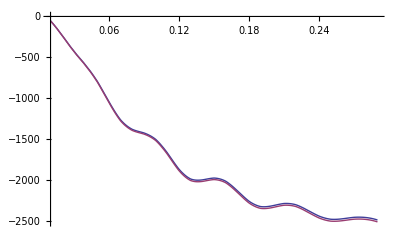

```mathematica
Plot[ {P13wa[2][k], P131loopFinal[k,-1.1]} , { k , .01 , .29}]
```

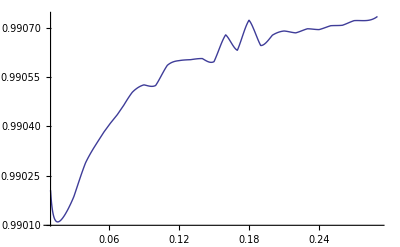

```mathematica
Plot[ {P13wa[2][k]/ P131loopFinal[k,-1.1]} , { k , .01 , .29}]
```

#### P22

```mathematica
P22expandeda=(δ2sola[k,a](δ2sola[kpr,a]/.{k11-> k12,k21-> k22,a1-> a2}))/.δsubsa//Expand;
```

Let us define these k-dependent coefficients:

```mathematica
Clear[Coeff1b,Coeff2b,Coeff3b,Coeff4b,Coeff5b,Coeff6b]
```

```mathematica
Coeff1b=α[k,k21,k11] α[kpr,k22,k12] δ1k[k11] δ1k[k12] δ1k[k21] δ1k[k22];
Coeff2b=α[kpr,k22,k12] β[k,k11,k21] δ1k[k11] δ1k[k12] δ1k[k21] δ1k[k22];
Coeff3b=α[k,k21,k11] β[kpr,k12,k22] δ1k[k11] δ1k[k12] δ1k[k21] δ1k[k22];
Coeff4b=β[k,k11,k21] β[kpr,k12,k22] δ1k[k11] δ1k[k12] δ1k[k21] δ1k[k22];
```

These are the time-dependent factors in front, to be integrated in (∫_0)^a0 ⅆa2 (∫_0)^a0 ⅆa1

```mathematica
int1ba=Coefficient[P22expandeda,Coeff1b]/.Greensubsa//FullSimplify;
int2ba=Coefficient[P22expandeda,Coeff2b]/.Greensubsa//FullSimplify;
int3ba=Coefficient[P22expandeda,Coeff3b]/.Greensubsa//FullSimplify;
int4ba=Coefficient[P22expandeda,Coeff4b]/.Greensubsa//FullSimplify;
```

Check that I included everything: ok.

```mathematica
P22factorizeda=(int1ba Coeff1b+int2ba Coeff2b+int3ba Coeff3b+int4ba Coeff4b);
```

```mathematica
CheckTotala=(P22expandeda/.Greensubsa)-P22factorizeda//FullSimplify
```

0

```mathematica
int1Nba[2] = NIntegrate[(int1ba/.TimeSubsa[2]/.aini->ain)/.a->a0 , {a2 , alow, a0} , { a1, alow , a0}];
int2Nba[2] = NIntegrate[(int2ba/.TimeSubsa[2]/.aini->ain)/.a->a0 , {a2 , alow, a0} , { a1, alow , a0}];
int3Nba[2] = NIntegrate[(int3ba/.TimeSubsa[2]/.aini->ain)/.a->a0 , {a2 , alow, a0} , { a1, alow , a0}];
int4Nba[2] = NIntegrate[(int4ba/.TimeSubsa[2]/.aini->ain)/.a->a0 , {a2 , alow, a0} , { a1, alow , a0}];
```

Ok, now I can clearly do the time integrals. For the k - integrals, I first need to do the contractions, which amount to substituing things like δ1k[k11] δ1k[k2] -> δD[k11 + k2] P11[k2]. Here there is only one cotraction because the α and β are symmetric.

Notice that I first do the constraction and then I kill the δ - function.

```mathematica
P22Coeff1=2(((Coeff1b //.{δ1k[k11]δ1k[k12]-> P11[(k11.k11)^(1/2)] δD[k11+k12],δ1k[k21] δ1k[k22]-> P11[(k21.k21)^(1/2)]δD[k21+k22]}))/.{δD[k11+k12]-> 1,k12-> -k11}/.{δD[k21+k22]-> 1,k22-> -k21})//FullSimplify;
P22Coeff2=2(((Coeff2b //.{δ1k[k11]δ1k[k12]-> P11[(k11.k11)^(1/2)] δD[k11+k12],δ1k[k21] δ1k[k22]-> P11[(k21.k21)^(1/2)]δD[k21+k22]}))/.{δD[k11+k12]-> 1,k12-> -k11}/.{δD[k21+k22]-> 1,k22-> -k21})//FullSimplify;
P22Coeff3=2(((Coeff3b //.{δ1k[k11]δ1k[k12]-> P11[(k11.k11)^(1/2)] δD[k11+k12],δ1k[k21] δ1k[k22]-> P11[(k21.k21)^(1/2)]δD[k21+k22]}))/.{δD[k11+k12]-> 1,k12-> -k11}/.{δD[k21+k22]-> 1,k22-> -k21})//FullSimplify;
P22Coeff4=2(((Coeff4b //.{δ1k[k11]δ1k[k12]-> P11[(k11.k11)^(1/2)] δD[k11+k12],δ1k[k21] δ1k[k22]-> P11[(k21.k21)^(1/2)]δD[k21+k22]}))/.{δD[k11+k12]-> 1,k12-> -k11}/.{δD[k21+k22]-> 1,k22-> -k21})//FullSimplify;
```

Now I need to impose momentum conservation in the vertex. When I constract the δ functions, I need to be careful on the replacements of the k’s, as I do not want to replace in the wrong addendum (which might have a different δ function). The trick to do this safely is to chose to solve for the δ-functions in terms of the common variable of integration, so we call substitution only for the variables that are un-common in the sums.

```mathematica
P22Coeff1Simpl=( (P22Coeff1/.{α[a_,b_,c_]-> αfn[b,c]δD[b+c-a],β[a_,b_,c_]-> βfn[b,c]δD[b+c-a] })/.{δD[-k+k11+k21] -> 1})/.{k21->k-k11}/.k11->kint//FullSimplify;
P22Coeff2Simpl=( (P22Coeff2/.{α[a_,b_,c_]-> αfn[b,c]δD[b+c-a],β[a_,b_,c_]-> βfn[b,c]δD[b+c-a] })/.{δD[-k+k11+k21] -> 1})/.{k21->k-k11}/.k11->kint//FullSimplify;
P22Coeff3Simpl=( (P22Coeff3/.{α[a_,b_,c_]-> αfn[b,c]δD[b+c-a],β[a_,b_,c_]-> βfn[b,c]δD[b+c-a] })/.{δD[-k+k11+k21] -> 1})/.{k21->k-k11}/.k11->kint//FullSimplify;
P22Coeff4Simpl=( (P22Coeff4/.{α[a_,b_,c_]-> αfn[b,c]δD[b+c-a],β[a_,b_,c_]-> βfn[b,c]δD[b+c-a] })/.{δD[-k+k11+k21] -> 1})/.{k21->k-k11}/.k11->kint//FullSimplify;
```

We are done. Each of the above integrals must be integrated by ∫ⅆ^3 kint P22Coeff4Simpl. 
 Then, each of them, must be multiplied by the separately computed  (∫_0)^a0 ⅆa2 (∫_0)^a0 ⅆa1 int1b. Add them up, and we are done.

```mathematica
αβSymmsubs = { αfn[x_,y_] -> αs[x,y] , βfn[x_,y_] -> βs[x,y]};
```

```mathematica
P22Integrand1Final[2][k_]=Simplify[((kint^2(2π))/(2π)^3((Coefficient[ P22Coeff1Simpl/.αβSymmsubs, δD[-k+-kpr]]/.kpr->-k)/.vecSubs1)/.P11->P11adiaSubs[2]), {k>0, kint>0}];
P22Integrand2Final[2][k_]=Simplify[((kint^2(2π))/(2π)^3((Coefficient[ P22Coeff2Simpl/.αβSymmsubs, δD[-k+-kpr]]/.kpr->-k)/.vecSubs1)/.P11->P11adiaSubs[2]), {k>0, kint>0}];
P22Integrand3Final[2][k_]=Simplify[((kint^2(2π))/(2π)^3((Coefficient[ P22Coeff3Simpl/.αβSymmsubs, δD[-k+-kpr]]/.kpr->-k)/.vecSubs1)/.P11->P11adiaSubs[2]), {k>0, kint>0}];
P22Integrand4Final[2][k_]=Simplify[((kint^2(2π))/(2π)^3((Coefficient[ P22Coeff4Simpl/.αβSymmsubs, δD[-k+-kpr]]/.kpr->-k)/.vecSubs1)/.P11->P11adiaSubs[2]), {k>0, kint>0}];
```

```mathematica
P22FinalTaba1[2] = Monitor[ Table[ {k ,  NIntegrate[ P22Integrand1Final[2][k] , { x,-1,1} , {kint, kir , 10}] ,   NIntegrate[ P22Integrand2Final[2][k] , { x,-1,1} , {kint, kir , 10}],   NIntegrate[ P22Integrand3Final[2][k] , { x,-1,1} , {kint, kir , 10}],  NIntegrate[ P22Integrand4Final[2][k] , { x,-1,1} , {kint, kir , 10}] } , { k , looptab2}] , k ];
```

```mathematica
P22FinalTaba[2] = Table[ { P22FinalTaba1[2][[i]][[1]] , int1Nba[2] P22FinalTaba1[2][[i]][[2]] + int2Nba[2] P22FinalTaba1[2][[i]][[3]] + int3Nba[2] P22FinalTaba1[2][[i]][[4]] + int4Nba[2] P22FinalTaba1[2][[i]][[5]] } ,  { i, 1, Length[P22FinalTaba1[1]]}] ;
```

```mathematica
P22wa[2]= Interpolation[P22FinalTaba[2]];
```

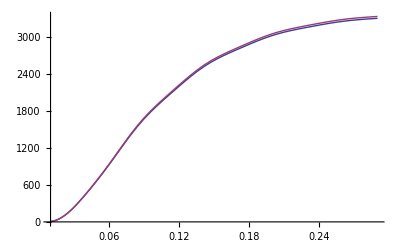

```mathematica
Plot[{ P22wa[2][k],P22FinalInterp[k,-1.1]} , { k , .01 , .29}]
```

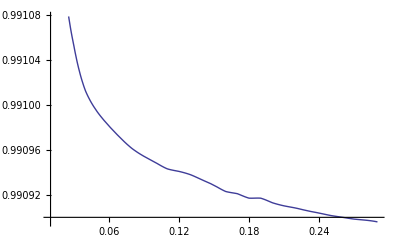

```mathematica
Plot[{ P22wa[2][k]/P22FinalInterp[k,-1.1]} , { k , .01 , .29}]
```

### Ptotal

```mathematica
PtotEFT[2][k_, csdm_, xi_] = ((Dadiawa[2][1])/(Dadiawa[2][ain]))^2 P11adiaSubs[2][k] + P13wa[2][k] + P22wa[2][k] - 2 k^2 csdm (1 + xi Subscript[Ω, Λ]/Subscript[Ω, m] (1 + w))  ((Dadiawa[2][1])/(Dadiawa[2][ain]))^2 P11adiaSubs[2][k]  /. paramSubsw[2];
```

```mathematica
P1loopEFTexactw[2][k_] =  P13wa[2][k] + P22wa[2][k] ;
```

```mathematica
P11[2][k_] = ((Dadiawa[2][1])/(Dadiawa[2][ain]))^2 P11adiaSubs[2][k];
```

# all plots

### approx 1 + w

```mathematica
LogLogPlot[ { PTotΛ[k,cs1]  ,Lin0[k]} , { k , .01 , .2},PlotStyle->{{Black,Thick}, {Black , DotDashed}}    ,   Frame->True,FrameLabel->{"k [h Mpc^-1]", "P_ΛCDM_"},   BaseStyle->{FontSize->18}  ]
```

InterpolatingFunction::dmval: Input value {-4.60511} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

-Graphics-

```mathematica
.2*2 π
```

1.25664

```mathematica
Plot[ {P1loopEFT[k,-.9,cs1, 0]/PTotΛ[k,cs1],P1loopEFT[k,-.9,cs1, 1]/PTotΛ[k,cs1], P1loopEFT[k,-.9,cs1, -1]/PTotΛ[k,cs1] ,P1loopEFT[k,-1.1,cs1, 0]/PTotΛ[k,cs1],P1loopEFT[k,-1.1,cs1, 1]/PTotΛ[k,cs1],P1loopEFT[k,-1.1,cs1, -1]/PTotΛ[k,cs1] , 1 , PTotwCDM[k,-.9,cs1, 0] /PTotΛ[k,cs1] , PTotwCDM[k,-1.1,cs1, 0] /PTotΛ[k,cs1] } , { k , .01 , .2},PlotStyle->{{Darker[Blue]} , {Opacity[0,Darker[Blue]]},{Opacity[0,Darker[Blue]]},{Darker[Red] },{Opacity[0,Darker[Red]],Dashed},{Opacity[0,Darker[Red]],Dashed},{Black,Thick} , {Darker[Blue],DotDashed, Thick},{Darker[Red],DotDashed, Thick}}, Filling->{  {1->{{2}, Opacity[.2,Darker[Blue]]}},{1->{{3}, Opacity[.2,Darker[Blue]]}} ,{4->{{5}, Opacity[.2,Darker[Red]]}},{4->{{6}, Opacity[.2,Darker[Red]]}}   }    ,   Frame->True,FrameLabel->{"k [h Mpc^-1]", "P^i/ P^ΛCDM"},   BaseStyle->{FontSize->18}  ]
```

-Graphics-

```mathematica
Plot[ {P1loopEFT[k,-.9,cs1, 0]/Plin[k,-.9],P1loopEFT[k,-.9,cs1, 1]/Plin[k,-.9], P1loopEFT[k,-.9,cs1, -1]/Plin[k,-.9] ,P1loopEFT[k,-1.1,cs1, 0]/Plin[k,-1.1],P1loopEFT[k,-1.1,cs1, 1]/Plin[k,-1.1],P1loopEFT[k,-1.1,cs1, -1]/Plin[k,-1.1] , PTotΛ[k,cs1]/Pmz0[-1.00][k]  , PTotwCDM[k,-.9,cs1, 0] /PlinwCDM[k,-.9] , PTotwCDM[k,-1.1,cs1, 0] /PlinwCDM[k,-1.1] } , { k , .01 , .2},PlotStyle->{{Darker[Blue]} , {Opacity[0,Darker[Blue]],Dashed},{Opacity[0,Darker[Blue]],Dashed},{Darker[Red]},{Opacity[0,Darker[Red]],Dashed},{Opacity[0,Darker[Red]],Dashed},{Black,Thick} , {Darker[Blue],DotDashed, Thick},{Darker[Red],DotDashed, Thick}}, Filling->{  {1->{{2}, Opacity[.2,Darker[Blue]]}},{1->{{3}, Opacity[.2,Darker[Blue]]}} ,{4->{{5}, Opacity[.2,Darker[Red]]}},{4->{{6}, Opacity[.2,Darker[Red]]}}   }    ,   Frame->True,FrameLabel->{"k [h Mpc^-1]", "P^i/ (P^i)_11"},   BaseStyle->{FontSize->18}    ]
```

-Graphics-

```mathematica
Plot[ {(P1loopEFT[k,-.9,cs1, 0]/Plin[k,-.9])/(PTotΛ[k,cs1]/Pmz0[-1.00][k]),(P1loopEFT[k,-.9,cs1, 1]/Plin[k,-.9])/(PTotΛ[k,cs1]/Pmz0[-1.00][k]), (P1loopEFT[k,-.9,cs1, -1]/Plin[k,-.9])/(PTotΛ[k,cs1]/Pmz0[-1.00][k]) ,(P1loopEFT[k,-1.1,cs1, 0]/Plin[k,-1.1])/(PTotΛ[k,cs1]/Pmz0[-1.00][k]),(P1loopEFT[k,-1.1,cs1, 1]/Plin[k,-1.1])/(PTotΛ[k,cs1]/Pmz0[-1.00][k]),(P1loopEFT[k,-1.1,cs1, -1]/Plin[k,-1.1] )/(PTotΛ[k,cs1]/Pmz0[-1.00][k]) , (PTotwCDM[k,-.9,cs1, 0] /PlinwCDM[k,-.9])/(PTotΛ[k,cs1]/Pmz0[-1.00][k]),(PTotwCDM[k,-1.1,cs1, 0] /PlinwCDM[k,-1.1])/(PTotΛ[k,cs1]/Pmz0[-1.00][k]) , 1 } , { k , .01 , .2},PlotStyle->{{Darker[Blue]} , {Opacity[0,Darker[Blue]],Dashed},{Opacity[0,Darker[Blue]],Dashed},{Darker[Red]},{Opacity[0,Darker[Red]],Dashed},{Opacity[0,Darker[Red]],Dashed}, {Darker[Blue],Thick,DotDashed},{Darker[Red],Thick,DotDashed}, {Black, Thick} }, Filling->{  {1->{{2}, Opacity[.2,Darker[Blue]]}},{1->{{3}, Opacity[.2,Darker[Blue]]}} ,{4->{{5}, Opacity[.2,Darker[Red]]}},{4->{{6}, Opacity[.2,Darker[Red]]}}   }    ,   Frame->True,FrameLabel->{"k [h Mpc^-1]", "(R^i)_/ R^ΛCDM"},   BaseStyle->{FontSize->18}    ]
```

-Graphics-

```mathematica
Plot[ {oneloop0[k]/Lin0[k] , Lin1[k,-0.9]/Lin0[k] ,  oneloop1[k,-0.9]/Lin0[k]} , { k , .01 , .2}, PlotStyle-> {   {Black,Thick}, {Darker[Blue], DotDashed } , {Darker[Blue]}   } , PlotRange->{-.1 , .3},   Frame->True,FrameLabel->{"k [h Mpc^-1]", "Δ P_ / (P^ΛCDM)_11"},   BaseStyle->{FontSize->18}, PlotLabel->"CQ, w = -0.9"]
```

-Graphics-

```mathematica
Plot[ { oneloop0wCDM[k]/Lin0[k] , Lin1wCDM[k,-0.9] /Lin0[k],  oneloop1wCDM[k,-0.9]/Lin0[k]} , { k , .01 , .2}, PlotStyle-> {   {Black,Thick}, {Darker[Blue], DotDashed } , {Darker[Blue]}   } , PlotRange->{-.1 , .3},   Frame->True,FrameLabel->{"k [h Mpc^-1]", "Δ P_ / (P^ΛCDM)_11"},   BaseStyle->{FontSize->18},PlotLabel->"wCDM, w = -0.9"]
```

-Graphics-

```mathematica
Plot[ {oneloop0[k]/Lin0[k] , Lin1[k,-1.1] /Lin0[k],  oneloop1[k,-1.1]/Lin0[k]} , { k , .01 , .2}, PlotStyle-> {   {Black,Thick}, {Darker[Red], DotDashed } , {Darker[Red]}   } , PlotRange->{-.1 , .3},   Frame->True,FrameLabel->{"k [h Mpc^-1]", "Δ P_ / (P^ΛCDM)_11"},   BaseStyle->{FontSize->18},PlotLabel->"CQ, w = -1.1"]
```

-Graphics-

```mathematica
Plot[ { oneloop0wCDM[k]/Lin0[k] , Lin1wCDM[k,-1.1]/Lin0[k] ,  oneloop1wCDM[k,-1.1]/Lin0[k]} , { k , .01 , .2}, PlotStyle-> {   {Black,Thick}, {Darker[Red], DotDashed } , {Darker[Red]}   }, PlotRange->{-.1 , .3} ,   Frame->True,FrameLabel->{"k [h Mpc^-1]", "Δ P_ / (P^ΛCDM)_11"},   BaseStyle->{FontSize->18},PlotLabel->"wCDM, w = -1.1"]
```

-Graphics-

```mathematica
Plot[ {  oneloop1[k,-.9] /Lin0[k],oneloop131[k,-.9]/Lin0[k], oneloop221[k,-.9]/Lin0[k] ,Lin1[k,-.9]/Lin0[k]} , { k , .01 , .2}, PlotStyle-> {  {Darker[Blue], Thick}, {Darker[Blue] } , {Darker[Blue], Dashed}   , {Darker[Blue] , Dotted}}, PlotRange->{-0.07 , 0.07},   Frame->True,FrameLabel->{"k [h Mpc^-1]", "Δ P_ / (P^ΛCDM)_11"},   BaseStyle->{FontSize->18},PlotLabel->"CQ, w = -0.9" ]
```

-Graphics-

```mathematica
Plot[ {  oneloop1wCDM[k,-0.9] /Lin0[k],(1+-0.9)(  P13wCDMN1[k] )/Lin0[k], (1+-0.9)(  P22wCDMN1[k] )/Lin0[k] ,Lin1wCDM[k,-0.9]/Lin0[k]} , { k , .01 , .2}, PlotStyle-> {  {Darker[Blue], Thick}, {Darker[Blue] } , {Darker[Blue], Dashed}   , {Darker[Blue] , Dotted}} ,PlotRange->{-0.07 , 0.07},   Frame->True,FrameLabel->{"k [h Mpc^-1]", "Δ P_ / (P^ΛCDM)_11"},   BaseStyle->{FontSize->18},PlotLabel->"wCDM, w = -0.9"]
```

-Graphics-

```mathematica
Plot[ {  oneloop1[k,-1.1]/Lin0[k] ,oneloop131[k,-1.1]/Lin0[k], oneloop221[k,-1.1]/Lin0[k], Lin1[k,-1.1] /Lin0[k]} , { k , .01 , .2}, PlotStyle-> {  {Darker[Red], Thick}, {Darker[Red] } , {Darker[Red], Dashed} ,  { Darker[Red] , Dotted}  } ,PlotRange->{-0.07 , 0.07},   Frame->True,FrameLabel->{"k [h Mpc^-1]", "Δ P_ / (P^ΛCDM)_11"},   BaseStyle->{FontSize->18},PlotLabel->"CQ, w = -1.1"]
```

-Graphics-

```mathematica
Plot[ {  oneloop1wCDM[k,-1.1] /Lin0[k],(1+-1.1)(  P13wCDMN1[k] )/Lin0[k], (1+-1.1)(  P22wCDMN1[k] )/Lin0[k] ,Lin1wCDM[k,-1.1]/Lin0[k]} , { k , .01 , .2}, PlotStyle-> {  {Darker[Red], Thick}, {Darker[Red] } , {Darker[Red], Dashed}   , {Darker[Red] , Dotted}},PlotRange->{-0.07 , 0.07},   Frame->True,FrameLabel->{"k [h Mpc^-1]", "Δ P_ / (P^ΛCDM)_11"},   BaseStyle->{FontSize->18},PlotLabel->"wCDM, w = -1.1" ]
```

-Graphics-

### exact 1 + w

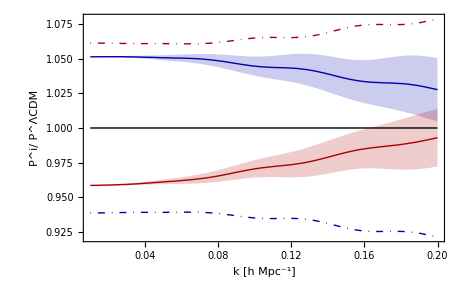

```mathematica
Plot[ {PtotEFT[1][k, cs1, 0]/PTotΛ[k,cs1],PtotEFT[1][k, cs1, 1]/PTotΛ[k,cs1], PtotEFT[1][k, cs1, -1]/PTotΛ[k,cs1] ,PtotEFT[2][k, cs1, 0]/PTotΛ[k,cs1],PtotEFT[2][k, cs1, 1]/PTotΛ[k,cs1],PtotEFT[2][k, cs1, -1]/PTotΛ[k,cs1] , 1 , PTotwCDM[k,-.9,cs1, 0] /PTotΛ[k,cs1] , PTotwCDM[k,-1.1,cs1, 0] /PTotΛ[k,cs1] } , { k , .01 , .2},PlotStyle->{{Darker[Blue]} , {Opacity[0,Darker[Blue]]},{Opacity[0,Darker[Blue]]},{Darker[Red] },{Opacity[0,Darker[Red]],Dashed},{Opacity[0,Darker[Red]],Dashed},{Black,Thick} , {Darker[Blue],DotDashed, Thick},{Darker[Red],DotDashed, Thick}}, Filling->{  {1->{{2}, Opacity[.2,Darker[Blue]]}},{1->{{3}, Opacity[.2,Darker[Blue]]}} ,{4->{{5}, Opacity[.2,Darker[Red]]}},{4->{{6}, Opacity[.2,Darker[Red]]}}   }    ,   Frame->True,FrameLabel->{"k [h Mpc^-1]", "P^i/ P^ΛCDM"},   BaseStyle->{FontSize->18}  ]
```

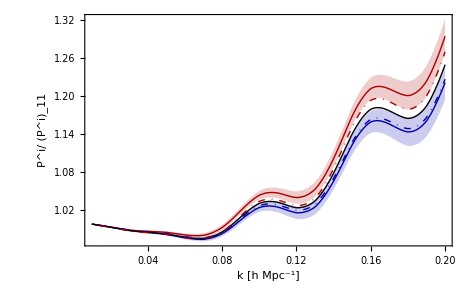

```mathematica
Plot[ {PtotEFT[1][k, cs1, 0]/P11[1][k],PtotEFT[1][k, cs1, 1]/P11[1][k], PtotEFT[1][k, cs1, -1]/P11[1][k] ,PtotEFT[2][k, cs1, 0]/P11[2][k],PtotEFT[2][k, cs1, 1]/P11[2][k],PtotEFT[2][k, cs1, -1]/P11[2][k] , PTotΛ[k,cs1]/Pmz0[-1.00][k]  , PTotwCDM[k,-.9,cs1, 0] /PlinwCDM[k,-.9] , PTotwCDM[k,-1.1,cs1, 0] /PlinwCDM[k,-1.1] } , { k , .01 , .2},PlotStyle->{{Darker[Blue]} , {Opacity[0,Darker[Blue]],Dashed},{Opacity[0,Darker[Blue]],Dashed},{Darker[Red]},{Opacity[0,Darker[Red]],Dashed},{Opacity[0,Darker[Red]],Dashed},{Black,Thick} , {Darker[Blue],DotDashed, Thick},{Darker[Red],DotDashed, Thick}}, Filling->{  {1->{{2}, Opacity[.2,Darker[Blue]]}},{1->{{3}, Opacity[.2,Darker[Blue]]}} ,{4->{{5}, Opacity[.2,Darker[Red]]}},{4->{{6}, Opacity[.2,Darker[Red]]}}   }    ,   Frame->True,FrameLabel->{"k [h Mpc^-1]", "P^i/ (P^i)_11"},   BaseStyle->{FontSize->18}    ]
```

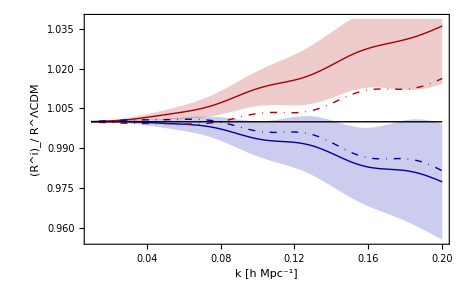

```mathematica
Plot[ {(PtotEFT[1][k, cs1, 0]/P11[1][k])/(PTotΛ[k,cs1]/Pmz0[-1.00][k]),(PtotEFT[1][k, cs1, 1]/P11[1][k])/(PTotΛ[k,cs1]/Pmz0[-1.00][k]), (PtotEFT[1][k, cs1, -1]/P11[1][k])/(PTotΛ[k,cs1]/Pmz0[-1.00][k]) ,(PtotEFT[2][k, cs1, 0]/P11[2][k])/(PTotΛ[k,cs1]/Pmz0[-1.00][k]),(PtotEFT[2][k, cs1, 1]/P11[2][k])/(PTotΛ[k,cs1]/Pmz0[-1.00][k]),(PtotEFT[2][k, cs1, -1]/P11[2][k] )/(PTotΛ[k,cs1]/Pmz0[-1.00][k]) , (PTotwCDM[k,-.9,cs1, 0] /PlinwCDM[k,-.9])/(PTotΛ[k,cs1]/Pmz0[-1.00][k]),(PTotwCDM[k,-1.1,cs1, 0] /PlinwCDM[k,-1.1])/(PTotΛ[k,cs1]/Pmz0[-1.00][k]) , 1 } , { k , .01 , .2},PlotStyle->{{Darker[Blue]} , {Opacity[0,Darker[Blue]],Dashed},{Opacity[0,Darker[Blue]],Dashed},{Darker[Red]},{Opacity[0,Darker[Red]],Dashed},{Opacity[0,Darker[Red]],Dashed}, {Darker[Blue],Thick,DotDashed},{Darker[Red],Thick,DotDashed}, {Black, Thick} }, Filling->{  {1->{{2}, Opacity[.2,Darker[Blue]]}},{1->{{3}, Opacity[.2,Darker[Blue]]}} ,{4->{{5}, Opacity[.2,Darker[Red]]}},{4->{{6}, Opacity[.2,Darker[Red]]}}   }    ,   Frame->True,FrameLabel->{"k [h Mpc^-1]", "(R^i)_/ R^ΛCDM"},   BaseStyle->{FontSize->18}    ]
```

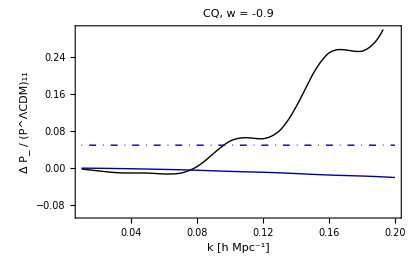

```mathematica
Plot[ {oneloop0[k]/Lin0[k] , ( P11[1][k]-Lin0[k])/Lin0[k] ,  (P1loopEFTexactw[1][k]-oneloop0[k]) /Lin0[k]} , { k , .01 , .2}, PlotStyle-> {   {Black,Thick}, {Darker[Blue], DotDashed } , {Darker[Blue]}   } , PlotRange->{-.1 , .3},   Frame->True,FrameLabel->{"k [h Mpc^-1]", "Δ P_ / (P^ΛCDM)_11"},   BaseStyle->{FontSize->18}, PlotLabel->"CQ, w = -0.9"]
```

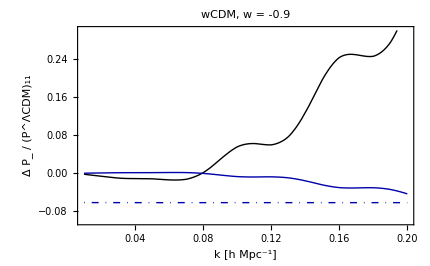

```mathematica
Plot[ { oneloop0wCDM[k]/Lin0[k] , Lin1wCDM[k,-0.9] /Lin0[k],  oneloop1wCDM[k,-0.9]/Lin0[k]} , { k , .01 , .2}, PlotStyle-> {   {Black,Thick}, {Darker[Blue], DotDashed } , {Darker[Blue]}   } , PlotRange->{-.1 , .3},   Frame->True,FrameLabel->{"k [h Mpc^-1]", "Δ P_ / (P^ΛCDM)_11"},   BaseStyle->{FontSize->18},PlotLabel->"wCDM, w = -0.9"]
```

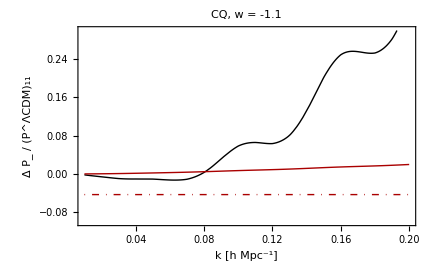

```mathematica
Plot[ {oneloop0[k]/Lin0[k] , ( P11[2][k]-Lin0[k]) /Lin0[k],  (P1loopEFTexactw[2][k]-oneloop0[k])/Lin0[k]} , { k , .01 , .2}, PlotStyle-> {   {Black,Thick}, {Darker[Red], DotDashed } , {Darker[Red]}   } , PlotRange->{-.1 , .3},   Frame->True,FrameLabel->{"k [h Mpc^-1]", "Δ P_ / (P^ΛCDM)_11"},   BaseStyle->{FontSize->18},PlotLabel->"CQ, w = -1.1"]
```

```mathematica
Plot[ { oneloop0wCDM[k]/Lin0[k] , Lin1wCDM[k,-1.1]/Lin0[k] ,  oneloop1wCDM[k,-1.1]/Lin0[k]} , { k , .01 , .2}, PlotStyle-> {   {Black,Thick}, {Darker[Red], DotDashed } , {Darker[Red]}   }, PlotRange->{-.1 , .3} ,   Frame->True,FrameLabel->{"k [h Mpc^-1]", "Δ P_ / (P^ΛCDM)_11"},   BaseStyle->{FontSize->18},PlotLabel->"wCDM, w = -1.1"]
```

-Graphics-

# computations using a, w=-1 test, remember to change growth factor

#### Setup equations

Let us write down the equations: these need to be adjusted to the correct equations. Also, the non - linear vertexes α and β need to be symmetrized. Integration over the k-varialbles is left implicit until the very last step (as well as substituting the label k with a 3-vector.)
 
all derivatives, or pr labels, are with respect to scale factor a

Note that the θ appearing below is really the rescaled Θ = - C/(ℋ f_+)θ

below α( k , k1, k2 ) = (2π)^3 δ^(3)( k - k_1 - k_2) α(k_1, k_2)

```mathematica
eqa={a D[δ[k,a], a]-fp[a] θ[k,a]== fp[a]/CC[a] α[k,k1,k2] δS[k1,a]θS[k2,a],a D[θ[k,a], a]-fp[a] θ[k,a]+ 3(Ωm CC[a])/(2 fp[a])(θ[k,a]-δ[k,a])==fp[a]/CC[a] β[k,k1,k2]θS[k1,a]θS[k2,a]};
```

```mathematica
αs[q1_,q2_] :=1 + (q1.q2)/2( 1/(q1.q1) + 1/(q2.q2));
α1[q1_,q2_] :=1 + q1.q2( 1/(q1.q1) );
βs[q1_,q2_] = (q1.q2 * (q1.q1 + q2.q2 + 2 q1.q2))/(2 q1.q1 * q2.q2);
```

δ2 Solution: let us put the integrations in k and η at the very end.

```mathematica
δ2sola[k_,a_]=Gδα[k,a,a1](α[k,k21,k11] fp[a1]δ1[k11,a1] θ1[k21,a1])/CC[a1]+Gδβ[k,a,a1](β[k,k11,k21]fp[a1]  θ1[k11,a1] θ1[k21,a1])/CC[a1];
θ2sola[k_,a_]=Gθα[k,a,a1](α[k,k21,k11] fp[a1]δ1[k11,a1] θ1[k21,a1])/CC[a1]+Gθβ[k,a,a1](β[k,k11,k21]fp[a1] θ1[k11,a1] θ1[k21,a1])/CC[a1];
```

δ3 Solution: : let us put the integration at the very end.

```mathematica
δ3sola[k_,a_]=Gδα[k,a,a2](α[k,k2,k1]fp[a2] (δ2[k1,a2] θ1[k2,a2]+δ1[k1,a2] θ2[k2,a2]))/CC[a2]+Gδβ[k,a,a2](β[k,k1,k2] fp[a2]2θ2[k1,a2] θ1[k2,a2])/CC[a2];
```

```mathematica
δ3solsuba[k_,a_]=δ3sola[k,a]/.{δ2[a___]-> δ2sola[a],θ2[a___]-> θ2sola[a]};
```

```mathematica
δ3solsubSimpa[k_,a_]=δ3solsuba[k,a]//FullSimplify;
```

This expression needs to be integrated in (∫_0)^a ⅆa2 (∫_0)^a2 ⅆa1 and also in the various momenta k's: basically, all repeated `indexes' must be integrated over.

Green’s Function

```mathematica
Gδαsola[k_,a_,a1_]=1/(a1 ( Dmpr[a1] Dpl[a1] - Dplpr[a1]Dm[a1]))(Dmpr[a1] Dpl[a] - Dplpr[a1] Dm[a])  ;
Gδβsola[k_,a_,a1_]=1/(a1 ( Dmpr[a1] Dpl[a1] - Dplpr[a1]Dm[a1]))((-fp[a1])/a1)(Dm[a1] Dpl[a] - Dpl[a1] Dm[a]);
Gθαsola[k_,a_,a1_]=1/(a1 ( Dmpr[a1] Dpl[a1] - Dplpr[a1]Dm[a1]))(Dmpr[a1] (a Dplpr[a])/fp[a] - Dplpr[a1] (a Dmpr[a])/fp[a]);
Gθβsola[k_,a_,a1_]=1/(a1 ( Dmpr[a1] Dpl[a1] - Dplpr[a1]Dm[a1]))((- fp[a1])/a1)(Dm[a1] (a Dplpr[a])/fp[a] - Dpl[a1](a Dmpr[a])/fp[a]);
```

Substitute Greens Functions

```mathematica
Greensubsa={Gδα[a___]-> Gδαsola[a],Gδβ[a___]-> Gδβsola[a],Gθα[a___]-> Gθαsola[a],Gθβ[a___]-> Gθβsola[a]};
```

```mathematica
δ3solGreena[k_,a_]=(δ3solsubSimpa[k,a]/.Greensubsa)//FullSimplify;
```

This expression needs to be integrated in (∫_0)^a0 ⅆa2 (∫_0)^a2 ⅆa1

It would be nice to be able to group the various integrals that factorize : time integral times a space integral. First let us  extract the time dependence

```mathematica
δsubsa={δ1[k_,a_]-> Dpl[a]/Dpl[aini] δ1k[k],θ1[k_,a_]-> (a Dplpr[a])/(fp[a]Dpl[aini])δ1k[k]};
```

#### P13 - symmetrization technique

Now, how do we separate the part to integrate in time from the ones to integrate in k. Let us see:

```mathematica
δ3Expandeda=(((δ3solGreena[k,a]/.δsubsa)//FullSimplify)//Expand);
```

Let us define these k-dependent coefficients:

```mathematica
Clear[Coeff1,Coeff2,Coeff3,Coeff4,Coeff5,Coeff6]
```

```mathematica
Coeff1=α[k,k2,k1]α[k1,k21,k11] δ1k[k2] δ1k[k11]δ1k[k21];
Coeff2=α[k,k2,k1]β[k1,k11,k21] δ1k[k2] δ1k[k11]δ1k[k21];
Coeff3=α[k,k2,k1]α[k2,k21,k11]δ1k[k1]δ1k[k11] δ1k[k21];
Coeff4=α[k,k2,k1]β[k2,k11,k21]δ1k[k1]δ1k[k11] δ1k[k21];
Coeff5=β[k,k1,k2]α[k1,k21,k11]δ1k[k2]δ1k[k11]  δ1k[k21];
Coeff6=β[k,k1,k2]β[k1,k11,k21]δ1k[k2]δ1k[k11]  δ1k[k21];
```

These are the time-dependent factors in front:

```mathematica
int1a=(Coefficient[δ3Expandeda,Coeff1]//FullSimplify);
int2a=(Coefficient[δ3Expandeda,Coeff2]//FullSimplify);
int3a=(Coefficient[δ3Expandeda,Coeff3]//FullSimplify);
int4a=(Coefficient[δ3Expandeda,Coeff4]//FullSimplify);
int5a=(Coefficient[δ3Expandeda,Coeff5]//FullSimplify);
int6a=(Coefficient[δ3Expandeda,Coeff6]//FullSimplify);
```

Check that I included everything: ok.

```mathematica
δ3factorizeda=(int1a Coeff1+int2a Coeff2+int3a Coeff3+int4a Coeff4+int5a Coeff5+int6a Coeff6);
```

```mathematica
CheckTotala=δ3Expandeda-δ3factorizeda//FullSimplify
```

0

Notice that the normalization of D_-does not matter in the int1...int6 above

```mathematica
TimeSubsa = {Dpl[a_]->Dadiawa[a], Dplpr[a_] -> Dadiawa[a] fwa[a]/a, fp[a_]->fwa[a], Dm[a_] -> Dminus[a], Dmpr[a_]-> Dminus[a] * fminus[a] / a, CC[a_] -> C1[a]/.paramSubsw};
```

```mathematica
int1Na = NIntegrate[(int1a/.TimeSubsa/.aini->ain)/.a->a0 , {a2 , alow, a0} , { a1, alow , a2}];
int2Na = NIntegrate[(int2a/.TimeSubsa/.aini->ain)/.a->a0 , {a2 , alow, a0} , { a1, alow , a2}];
int3Na = NIntegrate[(int3a/.TimeSubsa/.aini->ain)/.a->a0 , {a2 , alow, a0} , { a1, alow , a2}];
int4Na = NIntegrate[(int4a/.TimeSubsa/.aini->ain)/.a->a0 , {a2 , alow, a0} , { a1, alow , a2}];
int5Na = NIntegrate[(int5a/.TimeSubsa/.aini->ain)/.a->a0 , {a2 , alow, a0} , { a1, alow , a2}];
int6Na = NIntegrate[(int6a/.TimeSubsa/.aini->ain)/.a->a0 , {a2 , alow, a0} , { a1, alow , a2}];
```

Let’s symmetrize and redefine all of the momenta so that all of the terms have a factor of  δ1k[q1] δ1k[q2] δ1k[q3]

```mathematica
αβδsubs = { α[a_,b_,c_] -> δD[a - b -c] αfn[ b,c] ,  β[a_,b_,c_] -> δD[a - b -c] βfn[ b,c]};
```

```mathematica
Coeff1p[q1_,q2_,q3_] =((Coeff1/. αβδsubs)/.{k11->q1 , k2 -> q2 , k21->q3, k1->q4}) /. {δD[-q1-q3+q4] ->1 , q4->q1+q3};
Coeff2p[q1_,q2_,q3_] =((Coeff2/. αβδsubs)/.{k11->q1, k2->q2 , k21->q3, k1->q4})  /. {δD[-q1-q3+q4] ->1 , q4->q1 + q3};
Coeff3p[q1_,q2_,q3_] =((Coeff3/. αβδsubs)/.{k1->q1, k11->q2 , k21->q3 , k2->q4})   /.{ δD[-q2-q3+q4] -> 1 , q4->q2+q3};
Coeff4p[q1_,q2_,q3_] =((Coeff4/. αβδsubs)/.{k1->q1 , k11->q2 , k21->q3 , k2->q4})   /.{δD[-q2-q3+q4]->1 , q4->q2+q3 };
Coeff5p[q1_,q2_,q3_] =((Coeff5/. αβδsubs)/.{k11->q1 , k2->q2 , k21->q3 , k1->q4})   /.{δD[-q1-q3+q4]->1 , q4->q1 + q3 };
Coeff6p[q1_,q2_,q3_] =((Coeff6/. αβδsubs)/.{k11->q1 , k2->q2 , k21->q3, k1->q4})   /.{δD[-q1-q3+q4]->1 , q4->q1 + q3 };
```

```mathematica
Coeff1Sym[q1_,q2_,q3_] = 1/6( Coeff1p[q1,q2,q3] + Coeff1p[q1,q3,q2] + Coeff1p[q2,q1,q3] + Coeff1p[q2,q3,q1] + Coeff1p[q3,q2,q1] + Coeff1p[q3,q1,q2])//Simplify;
Coeff2Sym[q1_,q2_,q3_] = 1/6( Coeff2p[q1,q2,q3] + Coeff2p[q1,q3,q2] + Coeff2p[q2,q1,q3] + Coeff2p[q2,q3,q1] + Coeff2p[q3,q2,q1] + Coeff2p[q3,q1,q2])//Simplify;
Coeff3Sym[q1_,q2_,q3_] = 1/6( Coeff3p[q1,q2,q3] + Coeff3p[q1,q3,q2] + Coeff3p[q2,q1,q3] + Coeff3p[q2,q3,q1] + Coeff3p[q3,q2,q1] + Coeff3p[q3,q1,q2])//Simplify;
Coeff4Sym[q1_,q2_,q3_] = 1/6( Coeff4p[q1,q2,q3] + Coeff4p[q1,q3,q2] + Coeff4p[q2,q1,q3] + Coeff4p[q2,q3,q1] + Coeff4p[q3,q2,q1] + Coeff4p[q3,q1,q2])//Simplify;
Coeff5Sym[q1_,q2_,q3_] = 1/6( Coeff5p[q1,q2,q3] + Coeff5p[q1,q3,q2] + Coeff5p[q2,q1,q3] + Coeff5p[q2,q3,q1] + Coeff5p[q3,q2,q1] + Coeff5p[q3,q1,q2])//Simplify;
Coeff6Sym[q1_,q2_,q3_] = 1/6( Coeff6p[q1,q2,q3] + Coeff6p[q1,q3,q2] + Coeff6p[q2,q1,q3] + Coeff6p[q2,q3,q1] + Coeff6p[q3,q2,q1] + Coeff6p[q3,q1,q2])//Simplify;
```

If we write δ^(3)( k , a ) = ∫_(q_1 q_2 q_3) (2π)^3 δ( k - q_1-q_2-q_3) F_3^s(q_1,q_2,q_3;a) δ(q_1,a_in) δ(q_2,a_in) δ(q_3,a_in) , then the contribution to the power spectrum is P_13= 2 *3(D_+(η0))/(D_+(ηin)) ∫_q  F_3^s(k , q , -q ; a ) P_11^in(k) P_11^in(q) (the 2 is from δ^(1)δ^(3) + δ^(3)δ^(1), and the 3 is from the number of contractions.

```mathematica
FCoeff1 = Coefficient[ Coeff1Sym[q1,q2,q3] , δ1k[q1] δ1k[q2] δ1k[q3] δD[k-q1-q2-q3]] /. {q1->k , q2->q , q3->-q}/.{αfn[q,-q] ->0  , αfn[-q,q]->0,βfn[q,-q] ->0  , βfn[-q,q]->0} ;
```

```mathematica
FCoeff2 = Coefficient[ Coeff2Sym[q1,q2,q3] , δ1k[q1] δ1k[q2] δ1k[q3] δD[k-q1-q2-q3]] /. {q1->k , q2->q , q3->-q}/.{αfn[q,-q] ->0  , αfn[-q,q]->0,βfn[q,-q] ->0  , βfn[-q,q]->0};
```

```mathematica
FCoeff3 = Coefficient[ Coeff3Sym[q1,q2,q3] , δ1k[q1] δ1k[q2] δ1k[q3] δD[k-q1-q2-q3]] /. {q1->k , q2->q , q3->-q}/.{αfn[q,-q] ->0  , αfn[-q,q]->0,βfn[q,-q] ->0  , βfn[-q,q]->0};
```

```mathematica
FCoeff4 = Coefficient[ Coeff4Sym[q1,q2,q3] , δ1k[q1] δ1k[q2] δ1k[q3] δD[k-q1-q2-q3]] /. {q1->k , q2->q , q3->-q}/.{αfn[q,-q] ->0  , αfn[-q,q]->0,βfn[q,-q] ->0  , βfn[-q,q]->0};
```

```mathematica
FCoeff5 = Coefficient[ Coeff5Sym[q1,q2,q3] , δ1k[q1] δ1k[q2] δ1k[q3] δD[k-q1-q2-q3]] /. {q1->k , q2->q , q3->-q}/.{αfn[q,-q] ->0  , αfn[-q,q]->0,βfn[q,-q] ->0  , βfn[-q,q]->0};
```

```mathematica
FCoeff6 = Coefficient[ Coeff6Sym[q1,q2,q3] , δ1k[q1] δ1k[q2] δ1k[q3] δD[k-q1-q2-q3]] /. {q1->k , q2->q , q3->-q}/.{αfn[q,-q] ->0  , αfn[-q,q]->0,βfn[q,-q] ->0  , βfn[-q,q]->0};
```

We are done. Each of the above integrals must be integrated by ∫ⅆ^3 kint P13Coeff1Final. Then, each of them, must be multiplied by the separately computed  (∫_0)^a0 ⅆa2 (∫_0)^a2 ⅆa1 int1. Add them up, and we are done.

Define the integrands; the extra factor of ⅇ^(η0-ηin) comes from contracting with δ^(1)(k,a_0) = δ^(1)(k,a_in) *D_+(a_0) / D_+(a_in)

```mathematica
αβsubs= { αfn[x_,y_] -> α1[x,y] , βfn[x_,y_] -> βs[x,y]};
```

```mathematica
vecSubs1={k->k*{0,0,1},kint->kint*{Sqrt[1-x^2],0,x}};
```

```mathematica
P13Integrand1[.1]
```

-0.231539 (0.01+kint^2) x^2 Pmz5Interp[-1][0.1] Pmz5Interp[-1][kint]

```mathematica
P13Integrand1[k_]=2* 3 Dadiawa[1]/Dadiawa[ain] Simplify[((kint^2(2π))/(2π)^3(  (P11[(k.k)^(1/2)] P11[(kint.kint)^(1/2)]FCoeff1/.αβsubs/.q->kint)/.vecSubs1)/.P11->P11adiaSubs), {k>0, kint>0}];
P13Integrand2[k_]=2* 3 Dadiawa[1]/Dadiawa[ain] Simplify[((kint^2(2π))/(2π)^3(  (P11[(k.k)^(1/2)] P11[(kint.kint)^(1/2)]FCoeff2/.αβsubs/.q->kint)/.vecSubs1)/.P11->P11adiaSubs), {k>0, kint>0}];
P13Integrand3[k_]=2* 3 Dadiawa[1]/Dadiawa[ain] Simplify[((kint^2(2π))/(2π)^3(  (P11[(k.k)^(1/2)] P11[(kint.kint)^(1/2)]FCoeff3/.αβsubs/.q->kint)/.vecSubs1)/.P11->P11adiaSubs), {k>0, kint>0}];
P13Integrand4[k_]=2* 3 Dadiawa[1]/Dadiawa[ain] Simplify[((kint^2(2π))/(2π)^3(  (P11[(k.k)^(1/2)] P11[(kint.kint)^(1/2)]FCoeff4/.αβsubs/.q->kint)/.vecSubs1)/.P11->P11adiaSubs), {k>0, kint>0}];
P13Integrand5[k_]=2* 3 Dadiawa[1]/Dadiawa[ain] Simplify[((kint^2(2π))/(2π)^3(  (P11[(k.k)^(1/2)] P11[(kint.kint)^(1/2)]FCoeff5/.αβsubs/.q->kint)/.vecSubs1)/.P11->P11adiaSubs), {k>0, kint>0}];
P13Integrand6[k_]=2* 3 Dadiawa[1]/Dadiawa[ain] Simplify[((kint^2(2π))/(2π)^3(  (P11[(k.k)^(1/2)] P11[(kint.kint)^(1/2)]FCoeff6/.αβsubs/.q->kint)/.vecSubs1)/.P11->P11adiaSubs), {k>0, kint>0}];
```

```mathematica
P13FinalTabSymmaw1 = Monitor[ Table[ {k , (int1Na  NIntegrate[ P13Integrand1[k] , { x,-1,1} , {kint, kir , 10}] + int2Na  NIntegrate[ P13Integrand2[k] , { x,-1,1} , {kint, kir , 10}]+ int3Na  NIntegrate[ P13Integrand3[k] , { x,-1,1} , {kint, kir , 10}]+int4Na  NIntegrate[ P13Integrand4[k] , { x,-1,1} , {kint, kir , 10}]+int5Na  NIntegrate[ P13Integrand5[k] , { x,-1,1} , {kint, kir , 10}]+int6Na  NIntegrate[ P13Integrand6[k] , { x,-1,1} , {kint, kir , 10}]) } , { k , looptab2}] , k ]
```

{{0.01,-56.8112},{0.02,-242.176},{0.03,-441.241},{0.04,-611.718},{0.05,-812.848},{0.06,-1065.25},{0.07,-1289.77},{0.08,-1404.96},{0.09,-1447.11},{0.1,-1524.09},{0.11,-1689.62},{0.12,-1889.89},{0.13,-2009.34},{0.14,-2018.57},{0.15,-1994.71},{0.16,-2032.06},{0.17,-2148.58},{0.18,-2276.55},{0.19,-2341.34},{0.2,-2330.29},{0.21,-2301.44},{0.22,-2315.46},{0.23,-2381.05},{0.24,-2453.91},{0.25,-2491.67},{0.26,-2485.5},{0.27,-2466.83},{0.28,-2468.71},{0.29,-2498.48}}

```mathematica
P13wSymmaw1 = Interpolation[P13FinalTabSymmaw1];
```

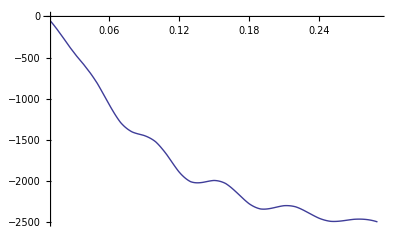

```mathematica
Plot[ P13wSymmaw1[k] , { k , .01 , .29}]
```

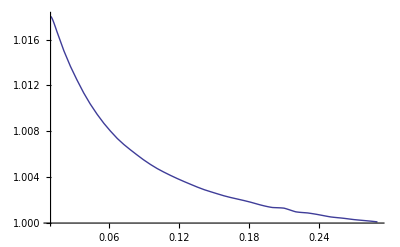

```mathematica
Plot[  P13ΛCDM[k]/P13wSymmaw1[k], { k , .01 , .29}]
```

#### P22

```mathematica
P22expandeda=(δ2sola[k,a](δ2sola[kpr,a]/.{k11-> k12,k21-> k22,a1-> a2}))/.δsubsa//Expand;
```

Let us define these k-dependent coefficients:

```mathematica
Clear[Coeff1b,Coeff2b,Coeff3b,Coeff4b,Coeff5b,Coeff6b]
```

```mathematica
Coeff1b=α[k,k21,k11] α[kpr,k22,k12] δ1k[k11] δ1k[k12] δ1k[k21] δ1k[k22];
Coeff2b=α[kpr,k22,k12] β[k,k11,k21] δ1k[k11] δ1k[k12] δ1k[k21] δ1k[k22];
Coeff3b=α[k,k21,k11] β[kpr,k12,k22] δ1k[k11] δ1k[k12] δ1k[k21] δ1k[k22];
Coeff4b=β[k,k11,k21] β[kpr,k12,k22] δ1k[k11] δ1k[k12] δ1k[k21] δ1k[k22];
```

These are the time-dependent factors in front, to be integrated in (∫_0)^a0 ⅆa2 (∫_0)^a0 ⅆa1

```mathematica
int1ba=Coefficient[P22expandeda,Coeff1b]/.Greensubsa//FullSimplify;
int2ba=Coefficient[P22expandeda,Coeff2b]/.Greensubsa//FullSimplify;
int3ba=Coefficient[P22expandeda,Coeff3b]/.Greensubsa//FullSimplify;
int4ba=Coefficient[P22expandeda,Coeff4b]/.Greensubsa//FullSimplify;
```

Check that I included everything: ok.

```mathematica
P22factorizeda=(int1ba Coeff1b+int2ba Coeff2b+int3ba Coeff3b+int4ba Coeff4b);
```

```mathematica
CheckTotala=(P22expandeda/.Greensubsa)-P22factorizeda//FullSimplify
```

0

```mathematica
int1Nba = NIntegrate[(int1ba/.TimeSubsa/.aini->ain)/.a->a0 , {a2 , alow, a0} , { a1, alow , a0}];
int2Nba = NIntegrate[(int2ba/.TimeSubsa/.aini->ain)/.a->a0 , {a2 , alow, a0} , { a1, alow , a0}];
int3Nba = NIntegrate[(int3ba/.TimeSubsa/.aini->ain)/.a->a0 , {a2 , alow, a0} , { a1, alow , a0}];
int4Nba = NIntegrate[(int4ba/.TimeSubsa/.aini->ain)/.a->a0 , {a2 , alow, a0} , { a1, alow , a0}];
```

Ok, now I can clearly do the time integrals. For the k - integrals, I first need to do the contractions, which amount to substituing things like δ1k[k11] δ1k[k2] -> δD[k11 + k2] P11[k2]. Here there is only one cotraction because the α and β are symmetric.

Notice that I first do the constraction and then I kill the δ - function.

```mathematica
P22Coeff1=2(((Coeff1b //.{δ1k[k11]δ1k[k12]-> P11[(k11.k11)^(1/2)] δD[k11+k12],δ1k[k21] δ1k[k22]-> P11[(k21.k21)^(1/2)]δD[k21+k22]}))/.{δD[k11+k12]-> 1,k12-> -k11}/.{δD[k21+k22]-> 1,k22-> -k21})//FullSimplify;
P22Coeff2=2(((Coeff2b //.{δ1k[k11]δ1k[k12]-> P11[(k11.k11)^(1/2)] δD[k11+k12],δ1k[k21] δ1k[k22]-> P11[(k21.k21)^(1/2)]δD[k21+k22]}))/.{δD[k11+k12]-> 1,k12-> -k11}/.{δD[k21+k22]-> 1,k22-> -k21})//FullSimplify;
P22Coeff3=2(((Coeff3b //.{δ1k[k11]δ1k[k12]-> P11[(k11.k11)^(1/2)] δD[k11+k12],δ1k[k21] δ1k[k22]-> P11[(k21.k21)^(1/2)]δD[k21+k22]}))/.{δD[k11+k12]-> 1,k12-> -k11}/.{δD[k21+k22]-> 1,k22-> -k21})//FullSimplify;
P22Coeff4=2(((Coeff4b //.{δ1k[k11]δ1k[k12]-> P11[(k11.k11)^(1/2)] δD[k11+k12],δ1k[k21] δ1k[k22]-> P11[(k21.k21)^(1/2)]δD[k21+k22]}))/.{δD[k11+k12]-> 1,k12-> -k11}/.{δD[k21+k22]-> 1,k22-> -k21})//FullSimplify;
```

Now I need to impose momentum conservation in the vertex. When I constract the δ functions, I need to be careful on the replacements of the k’s, as I do not want to replace in the wrong addendum (which might have a different δ function). The trick to do this safely is to chose to solve for the δ-functions in terms of the common variable of integration, so we call substitution only for the variables that are un-common in the sums.

```mathematica
P22Coeff1Simpl=( (P22Coeff1/.{α[a_,b_,c_]-> αfn[b,c]δD[b+c-a],β[a_,b_,c_]-> βfn[b,c]δD[b+c-a] })/.{δD[-k+k11+k21] -> 1})/.{k21->k-k11}/.k11->kint//FullSimplify;
P22Coeff2Simpl=( (P22Coeff2/.{α[a_,b_,c_]-> αfn[b,c]δD[b+c-a],β[a_,b_,c_]-> βfn[b,c]δD[b+c-a] })/.{δD[-k+k11+k21] -> 1})/.{k21->k-k11}/.k11->kint//FullSimplify;
P22Coeff3Simpl=( (P22Coeff3/.{α[a_,b_,c_]-> αfn[b,c]δD[b+c-a],β[a_,b_,c_]-> βfn[b,c]δD[b+c-a] })/.{δD[-k+k11+k21] -> 1})/.{k21->k-k11}/.k11->kint//FullSimplify;
P22Coeff4Simpl=( (P22Coeff4/.{α[a_,b_,c_]-> αfn[b,c]δD[b+c-a],β[a_,b_,c_]-> βfn[b,c]δD[b+c-a] })/.{δD[-k+k11+k21] -> 1})/.{k21->k-k11}/.k11->kint//FullSimplify;
```

We are done. Each of the above integrals must be integrated by ∫ⅆ^3 kint P22Coeff4Simpl. 
 Then, each of them, must be multiplied by the separately computed  (∫_0)^a0 ⅆa2 (∫_0)^a0 ⅆa1 int1b. Add them up, and we are done.

```mathematica
αβSymmsubs = { αfn[x_,y_] -> αs[x,y] , βfn[x_,y_] -> βs[x,y]};
```

```mathematica
P22Integrand1Final[k_]=Simplify[((kint^2(2π))/(2π)^3((Coefficient[ P22Coeff1Simpl/.αβSymmsubs, δD[-k+-kpr]]/.kpr->-k)/.vecSubs1)/.P11->P11adiaSubs), {k>0, kint>0}];
P22Integrand2Final[k_]=Simplify[((kint^2(2π))/(2π)^3((Coefficient[ P22Coeff2Simpl/.αβSymmsubs, δD[-k+-kpr]]/.kpr->-k)/.vecSubs1)/.P11->P11adiaSubs), {k>0, kint>0}];
P22Integrand3Final[k_]=Simplify[((kint^2(2π))/(2π)^3((Coefficient[ P22Coeff3Simpl/.αβSymmsubs, δD[-k+-kpr]]/.kpr->-k)/.vecSubs1)/.P11->P11adiaSubs), {k>0, kint>0}];
P22Integrand4Final[k_]=Simplify[((kint^2(2π))/(2π)^3((Coefficient[ P22Coeff4Simpl/.αβSymmsubs, δD[-k+-kpr]]/.kpr->-k)/.vecSubs1)/.P11->P11adiaSubs), {k>0, kint>0}];
```

```mathematica
P22FinalTaba1 = Monitor[ Table[ {k ,  NIntegrate[ P22Integrand1Final[k] , { x,-1,1} , {kint, kir , 10}] ,   NIntegrate[ P22Integrand2Final[k] , { x,-1,1} , {kint, kir , 10}],   NIntegrate[ P22Integrand3Final[k] , { x,-1,1} , {kint, kir , 10}],  NIntegrate[ P22Integrand4Final[k] , { x,-1,1} , {kint, kir , 10}] } , { k , looptab2}] , k ];
```

```mathematica
P22FinalTabaw1 = Table[ { P22FinalTaba1[[i]][[1]] , int1Nba P22FinalTaba1[[i]][[2]] + int2Nba P22FinalTaba1[[i]][[3]] + int3Nba P22FinalTaba1[[i]][[4]] + int4Nba P22FinalTaba1[[i]][[5]] } ,  { i, 1, Length[P22FinalTaba1]}] ;
```

```mathematica
P22waw1= Interpolation[P22FinalTabaw1];
```

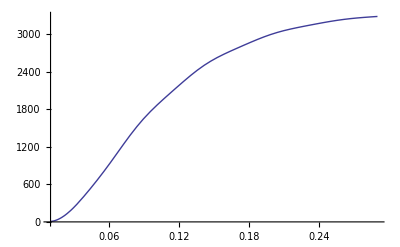

```mathematica
Plot[ P22waw1[k] , { k , .01 , .29}]
```

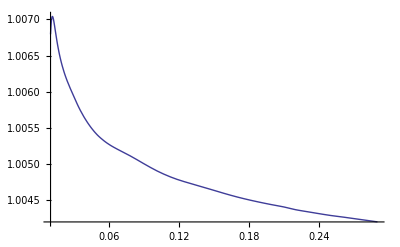

```mathematica
Plot[ P22waw1[k]/P22ΛCDM[k] , { k , .01 , .29}]
```

#### Ptotal

```mathematica
P1loopTotTabaw1 = Table[ { P22FinalTabaw1[[i]][[1]] , P22FinalTabaw1[[i]][[2]] + P13FinalTabSymmaw1[[i]][[2]]} , { i , 1 , Length[P22FinalTabaw1]}]
```

{{0.01,-49.3256},{0.02,-165.909},{0.03,-208.712},{0.04,-170.964},{0.05,-143.014},{0.06,-149.132},{0.07,-112.724},{0.08,27.3501},{0.09,210.658},{0.1,324.557},{0.11,329.736},{0.12,294.4},{0.13,334.623},{0.14,467.784},{0.15,608.213},{0.16,665.648},{0.17,633.503},{0.18,587.148},{0.19,599.854},{0.2,678.19},{0.21,760.649},{0.22,789.189},{0.23,760.81},{0.24,723.402},{0.25,718.647},{0.26,752.745},{0.27,792.746},{0.28,806.762},{0.29,789.868}}

```mathematica
P1loopwaw1 = Interpolation[P1loopTotTabaw1];
```

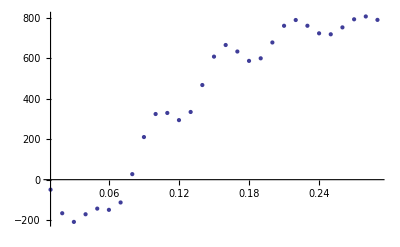

```mathematica
ListPlot[ P1loopTotTabaw1, PlotRange->All]
```

```mathematica
PTotTaba1w1 = Table[ { P22FinalTabaw1[[i]][[1]] ,((Dadiawa[1]/Dadiawa[ain])^2 P11adiaSubs[ P22FinalTabaw1[[i]][[1]] ] +  P22FinalTabaw1[[i]][[2]] + P13FinalTabSymmaw1[[i]][[2]])} , { i , 1 , Length[P22FinalTabaw1]}];
```

```mathematica
PTotwa1w1 = Interpolation[PTotTaba1w1, InterpolationOrder->6];
```

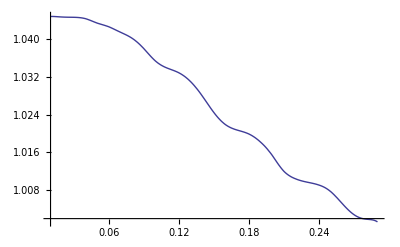

```mathematica
Plot[ PTotwa[k]/ PTotwa1w1[k] , { k , 0.01 , .29}]
```

```mathematica
PTotwaEFT[k_,csw_] = PTotwa[k] - 2 k^2 cs1(1 + (1+-0.9)csw) Pmz0wn1[k];
```

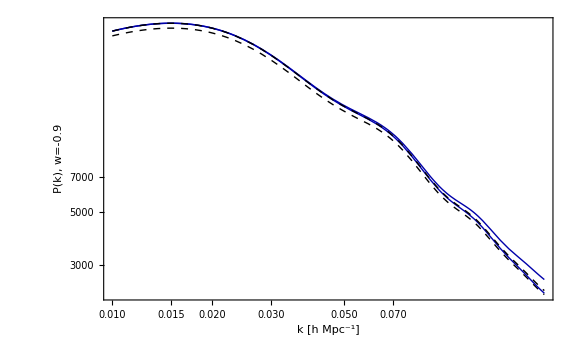

```mathematica
LogLogPlot[ {PTotwa[k], PTotΛ[k,cs1], PTotwaEFT[k,1], PTotwaEFT[k,-1]} , { k , .01 , .2}, PlotStyle->{{Darker[Blue], Thick} , {Black,Dashed}}, Frame->True,FrameLabel->{"k [h Mpc^-1]", "P(k), w=-0.9"},ImageSize->Large,BaseStyle->{FontSize->18}, PlotLegend->{Style["P_(w = -0.9)", 18],Style["P_ΛCDM",18]},LegendShadow->None,LegendPosition->{-.6,-.3}, LegendSize->.5]
```

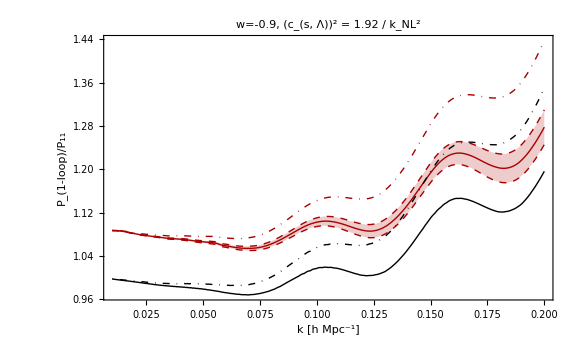

```mathematica
Plot[ {PTotwaEFT[k,0]/((Dadiawa[1]/Dadiawa[ain])^2 P11adiaSubs[k]), PTotΛ[k,cs1]/Pmz0wn1[k],PTotΛ[k,0]/Pmz0wn1[k],PTotwaEFT[k,2]/((Dadiawa[1]/Dadiawa[ain])^2 P11adiaSubs[k]),PTotwaEFT[k,-2]/((Dadiawa[1]/Dadiawa[ain])^2 P11adiaSubs[k]),PTotwa[k]/((Dadiawa[1]/Dadiawa[ain])^2 P11adiaSubs[k])} , { k , .01 , .2}, PlotStyle->{{Darker[Red], Thick}, {Black} , {Black,DotDashed},{Darker[Red], Thick,Dashed},{Darker[Red], Thick,Dashed},{Darker[Red], DotDashed}}, Frame->True,FrameLabel->{"k [h Mpc^-1]", "P_(1-loop)/P_11"},ImageSize->Large,BaseStyle->{FontSize->18}, PlotLegend->{Style["P_(w = -0.9), (c_(s, Λ))^2", 14],Style["P_ΛCDM, (c_(s, Λ))^2",14],Style["P_ΛCDM, SPT",14],Style["P_(w = -0.9), (c_(s, Λ))^2(1+2(1+w)) ",14],Style["P_(w = -0.9), (c_(s, Λ))^2(1-2(1+w)) ",14],Style["P_(w = -0.9), SPT",14]},LegendShadow->None,LegendPosition->{.8,-.4}, LegendSize->{2.5,1}, Filling->{1->{{4}, {Opacity[.2,Darker[Red]]}}, 1->{{5}, {Opacity[.2,Darker[Red]]}}}, PlotLabel->"w=-0.9, (c_(s, Λ))^2 = 1.92 / k_NL^2"]
```

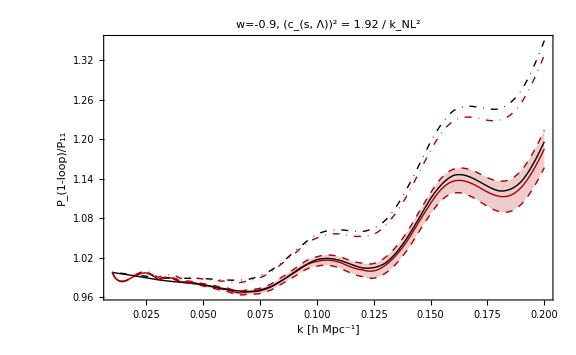

-Graphics-

Legend::badsize: The LegendSize option must be a number or a pair of numbers greater than zero, or it must be Automatic. Using the default value instead.

```mathematica
Plot[ {((Dadiawa[1]/Dadiawa[ain])^2 P11adiaSubs[k])/ Pmz0wn1[k]} , { k , .01 , .2}, PlotStyle->{{Black, Thick} , {Black,Dashed}}, Frame->True,FrameLabel->{"k [h Mpc^-1]", "P_(w = -0.9)(k)/P_ΛCDM(k)"},ImageSize->Large,BaseStyle->{FontSize->20}, PlotLabel->"Linear", PlotRange->{1.075,1.08}]
```

-Graphics-

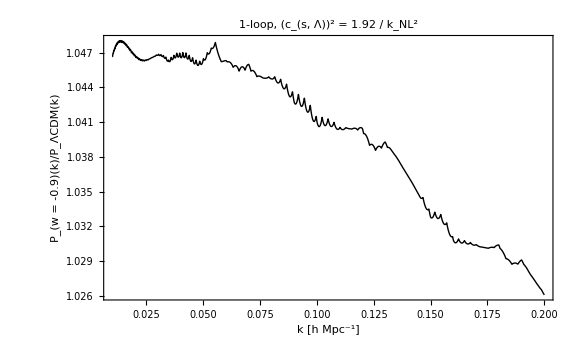

```mathematica
Plot[ {PTotwaEFT[k,0]/ PTotΛ[k,cs1]} , { k , .01 , .2}, PlotStyle->{{Black, Thick} , {Black,Dashed}}, Frame->True,FrameLabel->{"k [h Mpc^-1]", "P_(w = -0.9)(k)/P_ΛCDM(k)"},ImageSize->Large,BaseStyle->{FontSize->20}, PlotLabel->"1-loop, (c_(s, Λ))^2 = 1.92 / k_NL^2"]
```

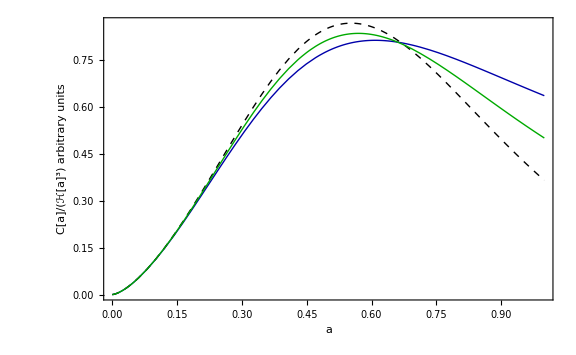

```mathematica
Plot[ {1/(2 10^-6)(ℋ0 √(Subscript[Ω, m]/a+Subscript[Ω, Λ] a^2 a^(-3(1+w))))^-3 C1[a]/.paramSubs/.w->-.9,1/(2 10^-6)C1[a] (ℋ0 √(Subscript[Ω, m]/a+Subscript[Ω, Λ] a^2 a^(-3(1+w))))^-3/.paramSubs/.w->-1.1,(ℋ0 √(Subscript[Ω, m]/a+Subscript[Ω, Λ] a^2 a^(-3(1+w))))^-3 1/(2 10^-6)C1[a]/.paramSubs/.w->-1} , { a , 0, 1},PlotStyle->{{Darker[Blue], Thick} , {Black,Dashed},{Darker[Green]}}, Frame->True,FrameLabel->{"a", "C[a]/ℋ[a]^3 arbitrary units"},ImageSize->Large,BaseStyle->{FontSize->20},PlotLegend->{Style["w = -0.9", 16],Style["w = - 1",16], Style["w = -1.1", 16]},LegendShadow->None,LegendPosition->{0,-.3}, LegendSize->.45]
```